Here we build the data base to run the models and to make the analysis of LoS

```mathematica
SetDirectory["/home/lina/Documents/datos_INS"]
```

/home/lina/Documents/datos_INS

## Data

## Data total without demographics

### Functions

#### Other functions

```mathematica
Clear[toDataObject]
```

```mathematica
toDataObject["NotFound"]:=""(*se pone 10 para que la resta con el control de -10 e identificar esto como la barra de los  casos sin fecha. IGUAL NO IMPORTA PORQUE EL HISTOGRAMA NO GRAFICA LOS STRINGS*)
toDataObject[date_]:=DateObject[date]
```

#### With output: date

```mathematica
(* LA SALIDA EN FORMA DE DateObject ES IMPORTANTE PARA HACER LAS RESTAS RESPECTIVAS DE FECHAS*)
```

```mathematica
Clear[adHospital,fHospToCR,fHospToF,fHospToUCI,adUCI,fUCIToCR,fUCIToF,fUCIToH,feFallecido,feRecuperado]
```

```mathematica
adHospital[caso_]:=FirstCase[caso,{_,x_}/;StringMatchQ[x,"hospital"]] [[1]]//toDataObject(* To indentify the admission to Hospital*)
```

```mathematica
fHospToCR[caso_]:=(FirstCase[Partition[caso,2,1],{{_,x_},{_,y_}}/;StringMatchQ[x,"hospital"]&&(StringMatchQ[y,"casa"]||StringMatchQ[y,"recuperado"])]/.Missing["NotFound"]->{{},{"NotFound"}}) [[2,1]]//toDataObject(* To indentify the discharge from Hospital and goes to casa or recuperation*)
```

```mathematica
fHospToF[caso_]:=(FirstCase[Partition[caso,2,1],{{_,x_},{_,y_}}/;StringMatchQ[x,"hospital"]&&StringMatchQ[y,"fallecido"]]/.Missing["NotFound"]->{{},{"NotFound"}}) [[2,1]]//toDataObject (* To indentify the discharge from Hospital and do dead*)
```

```mathematica
fHospToUCI[caso_]:=(FirstCase[Partition[caso,2,1],{{_,x_},{_,y_}}/;StringMatchQ[x,"hospital"]&&StringMatchQ[y,"hospital UCI"]] /.Missing["NotFound"]->{{},{"NotFound"}}) [[2,1]]//toDataObject(* To indentify the discharge from Hospital and goes to UCI *)
```

```mathematica
adUCI[caso_]:=FirstCase[caso,{_,x_}/;StringMatchQ[x,"hospital UCI"]] [[1]]//toDataObject(* To indentify the admission to UCI*)
```

```mathematica
fUCIToCR[caso_]:=(FirstCase[Partition[caso,2,1],{{_,x_},{_,y_}}/;StringMatchQ[x,"hospital UCI"]&&(StringMatchQ[y,"casa"]||StringMatchQ[y,"recuperado"])] /.Missing["NotFound"]->{{},{"NotFound"}}) [[2,1]]//toDataObject(* To indentify the discharge from UCI and goes to casa or recuperation*)
```

```mathematica
fUCIToF[caso_]:=(FirstCase[Partition[caso,2,1],{{_,x_},{_,y_}}/;StringMatchQ[x,"hospital UCI"]&&StringMatchQ[y,"fallecido"]]/.Missing["NotFound"]->{{},{"NotFound"}}) [[2,1]]//toDataObject(* To indentify the discharge from UCI and do dead*)
```

```mathematica
fUCIToH[caso_]:=(FirstCase[Partition[caso,2,1],{{_,x_},{_,y_}}/;StringMatchQ[x,"hospital UCI"]&&StringMatchQ[y,"hospital"]]/.Missing["NotFound"]->{{},{"NotFound"}}) [[2,1]]//toDataObject(* To indentify the discharge from UCI and goes to hospital*)
```

```mathematica
(*NOTA:  Para identificar que esto esta bien podriamos tomar 10 casos aleatorios y revisar cada uno para saber si cohinciden las fechas*)
```

```mathematica
(* ESTAS SON MEJORES FUNCIONES PARA IDENTIFICAR EL OUTCOME PORQUE NO LE DAN LUGAR A ERRORES*)
```

```mathematica
feFallecido[caso_]:=(FirstCase[Partition[caso,2,1],{{_,y_},{_,x_}}/;(StringMatchQ[y,"hospital"]||StringMatchQ[y,"hospital UCI"])&&StringMatchQ[x,"fallecido"]]/.Missing["NotFound"]->{{},{"NotFound"}}) [[2,1]]//toDataObject(* To indentify fecha fallecido*)
```

```mathematica
feRecuperado[caso_]:=(FirstCase[Partition[caso,2,1],{{_,y_},{_,x_}}/;(StringMatchQ[y,"hospital"]||StringMatchQ[y,"hospital UCI"])&&(StringMatchQ[x,"casa"]||StringMatchQ[x,"recuperado"])]/.Missing["NotFound"]->{{},{"NotFound"}}) [[2,1]]//toDataObject(* To indentify fecha recuperacion *)
```

```mathematica
estFallecido[caso_]:=(FirstCase[Partition[caso,2,1],{{_,y_},{_,x_}}/;(StringMatchQ[y,"hospital"]||StringMatchQ[y,"hospital UCI"])&&StringMatchQ[x,"fallecido"]]/.Missing["NotFound"]->{{},{"","Missing"}})[[2,2]](* To indentify Outcome: fallecido*)
```

```mathematica
estRecuperado[caso_]:=(FirstCase[Partition[caso,2,1],{{_,y_},{_,x_}}/;(StringMatchQ[y,"hospital"]||StringMatchQ[y,"hospital UCI"])&&(StringMatchQ[x,"casa"]||StringMatchQ[x,"recuperado"])]/.Missing["NotFound"]->{{},{"","Missing"}})[[2,2]](* To indentify Outcome: recuperacion *)
```

```mathematica
(* VIEJAS FUNCIONES PARA IDENTIFICAR EL OUTCOME: base de datos  entre la 1 a la 5 se hicieron con estas FUNCIONES: 
feFallecido[caso_]:=FirstCase[caso,{y_,x_}/;StringMatchQ[x,___~~"allecido"]][[1]]//toDataObject(* To indentify fecha fallecido*)
feRecuperado[caso_]:=FirstCase[caso,{y_,x_}/;StringMatchQ[x,___~~"cuperado"~~___]][[1]]//toDataObject (* To indentify fecha recuperacion *)
estFallecido[caso_]:=(FirstCase[caso,{y_,x_}/;StringMatchQ[x,___~~"allecido"]]/.Missing["NotFound"]->{{},"Missing"})[[2]](* To indentify Outcome: fallecido*)
estRecuperado[caso_]:=(FirstCase[caso,{y_,x_}/;StringMatchQ[x,___~~"cuperado"~~___]]/.Missing["NotFound"]->{{},"Missing"})[[2]](* To indentify Outcome: recuperacion *)*)
```

### DataBase

```mathematica
(*masterM15-2020HUCIDefOutComplete2.m - Aqui estan los 44 132 casos de marzo a octubre 2020 *)
```

```mathematica
masterMfechas=Import["/home/lina/Documents/datos_INS/masterM15-2020HUCIDefOutComplete2.m"];
```

```mathematica
(***************Estas se analizan de forma independiente y luego se introducen a la base de datos *)
```

```mathematica
(* Aunque se renombraron masterMfechas0-4. En las secciones DataBase1-5 donse se analizan los datos 2021 solo se incluyen las matrices de los grupos G3-5. Por eso se hace una neva sección DataBase-6 para incluir todos los casos 2020-2021 con ingreso H/ICU y outcome definido dentro de los grupos G1-G5*)
```

```mathematica
masterMfechas1=Import["/home/lina/Documents/datos_INS/casesOutcomefechas_G1.m"];
```

```mathematica
masterMfechas2=Import["/home/lina/Documents/datos_INS/casesOutcomefechas_G2.m"];
```

```mathematica
masterMfechas3=Import["/home/lina/Documents/datos_INS/casesOutcomefechas_G3.m"];
```

```mathematica
masterMfechas4=Import["/home/lina/Documents/datos_INS/casesOutcomefechas_G4.m"];
```

```mathematica
masterMfechas5=Import["/home/lina/Documents/datos_INS/casesOutcomefechas_G5.m"];
```

```mathematica
Length/@{masterMfechas1[[1]],masterMfechas2[[1]],masterMfechas3[[1]],masterMfechas4[[1]],masterMfechas5[[1]]}(* número de fechas analizadas por caso *)
```

{510,510,224,224,100}

```mathematica
masterMfechas=Join[masterMfechas1,masterMfechas2,masterMfechas3,masterMfechas4,masterMfechas5];
```

```mathematica
masterMfechas//Length (* Numero de hospitalizados (H/ICU) en colombia desde marzo2020  a agosto2021 *)
```

245375

```mathematica
masterMfechas[[1]]//Short
```

{{fecha,2},{2020-03-15,hospital},{2020-03-16,hospital},{2020-03-17,hospital},{2020-03-18,hospital},«500»,{2021-08-13,casa},{2021-08-14,casa},{2021-08-15,casa},{2021-08-16,casa},{2021-08-17,casa}}

```mathematica
(*******************************************************************************)
```

```mathematica
Export["/home/lina/Documents/datos_INS/masterM2020_2021.m",masterMfechas]
```

/home/lina/Documents/datos_INS/masterM2020_2021.m

```mathematica
(* Esta es la primera solo con G3-G5: "/home/lina/Documents/datos_INS/masterM2021.m" - 
en masterM se hacia un paso adicional de Transponer para tener la primera columna de las fechas y las demas columnas de cada caso. Pero esto no es necesario para aplicar la funciones. Las funciones se aplicaban as: DATAD=adHospital[masterM[[All,{1,#}]]]&/@Range[Sequence@@range]; ahora se aplican diferente (ver abajo)

Esta es la segunda con G1-G5: "/home/lina/Documents/datos_INS/masterM2020-2021.m" - 15/03/2020 - 17/08/2020 *)
```

```mathematica
masterM=Import["/home/lina/Documents/UnCover/datos_INS/masterM2021.m"];
```

```mathematica
masterM[[1]]//Length
```

33765

```mathematica
masterM=Import["/home/lina/Documents/UnCover/datos_INS/masterM2020_2021.m"];
```

```mathematica
masterM[[1]]//Length;
```

```mathematica
%
```

```mathematica
masterM=masterMfechas;
```

```mathematica
casesHICUDefOut=StringDrop[#,4]&/@masterM[[1,2;;]](*Esto es para Eliminar la palabra caso de casoX*);
```

```mathematica
casesHICUDefOut=masterM[[1,2;;]](*cuando no se nombre como casoX*);
```

```mathematica
masterM[[1]]//Short
```

{{fecha,2},{2020-03-15,hospital},{2020-03-16,hospital},{2020-03-17,hospital},{2020-03-18,hospital},«500»,{2021-08-13,casa},{2021-08-14,casa},{2021-08-15,casa},{2021-08-16,casa},{2021-08-17,casa}}

```mathematica
masterM[[All,1,2]]//Short
```

{2,7,12,13,14,16,19,33,57,61,64,68,69,81,86,95,«245344»,4864779,4864799,4864890,4864993,4865137,4865286,4865330,4865377,4865472,4866625,4867893,4867901,4867998,4868224,4870035}

```mathematica
masterM[[All,1]]//Short
```

{{fecha,2},{fecha,7},{fecha,12},{fecha,13},{fecha,14},{fecha,16},{fecha,19},«245362»,{fecha,4866625},{fecha,4867893},{fecha,4867901},{fecha,4867998},{fecha,4868224},{fecha,4870035}}

```mathematica
range={1,masterM[[All,1]]//Length}
```

{1,245375}

```mathematica
DATAD=adHospital[masterM[[#]]]&/@Range[Sequence@@range];(*Date of admission*)
```

```mathematica
fHospToCRd=fHospToCR[masterM[[#]]]&/@Range[Sequence@@range];
```

```mathematica
fHospToFd=fHospToF[masterM[[#]]]&/@Range[Sequence@@range];
```

```mathematica
fHospTpUCId=fHospToUCI[masterM[[#]]]&/@Range[Sequence@@range];
```

```mathematica
DATADI=adUCI[masterM[[#]]]&/@Range[Sequence@@range];
```

```mathematica
fUCIToCRd=fUCIToCR[masterM[[#]]]&/@Range[Sequence@@range];
```

```mathematica
fUCIToFd=fUCIToF[masterM[[#]]]&/@Range[Sequence@@range];
```

```mathematica
fUCIToHd=fUCIToH[masterM[[#]]]&/@Range[Sequence@@range];
```

```mathematica
DATAD//Length
```

75361

## Data total demographics

### General

```mathematica
(* 
 "dataBase_Colombia1.csv" casos 2 al 3000      de masterM   pero en el OPAL son 1 al 2999
"dataBase_Colombia2.csv" casos 3001 al 7000   de masterM   pero en el OPAL son 3000 al 6999
"dataBase_Colombia3.csv" casos 7001 al 12000  de masterM   pero en el OPAL son 7000 al 11999
"dataBase_Colombia4.csv" casos 12001 al 17000 de masterM   pero en el OPAL son 12000 al 16999
"dataBase_Colombia5.csv" casos 17001 al 22000 de masterM   pero en el OPAL son 17000 al 21999
"dataBase_Colombia6.csv" casos 22001 al 27000 de masterM   pero en el OPAL son 22000 al 26999
"dataBase_Colombia7.csv" casos 27001 al 32000 de masterM   pero en el OPAL son 27000 al 31999
"dataBase_Colombia8.csv" casos 32001 al 37000 de masterM   pero en el OPAL son 32000 al 36999
"dataBase_Colombia9.csv" casos 37001 al 44132 de masterM   pero en el OPAL son 37000 al 44131*)
```

```mathematica
data1=Import["/home/lina/Documents/datos_INS/dataBase_Colombia1.csv"];
data2=Import["/home/lina/Documents/datos_INS/dataBase_Colombia2.csv"];
data3=Import["/home/lina/Documents/datos_INS/dataBase_Colombia3.csv"];
data4=Import["/home/lina/Documents/datos_INS/dataBase_Colombia4.csv"];
data5=Import["/home/lina/Documents/datos_INS/dataBase_Colombia5.csv"];
data6=Import["/home/lina/Documents/datos_INS/dataBase_Colombia6.csv"];
data7=Import["/home/lina/Documents/datos_INS/dataBase_Colombia7.csv"];
data8=Import["/home/lina/Documents/datos_INS/dataBase_Colombia8.csv"];
data9=Import["/home/lina/Documents/datos_INS/dataBase_Colombia9.csv"];
```

```mathematica
(***************Estas se analizan de forma independiente y luego se introducen a la base de datos *)
```

```mathematica
data10=Import["/home/lina/Documents/datos_INS/dataBase_ColombiaG3.csv"];
data11=Import["/home/lina/Documents/datos_INS/dataBase_ColombiaG4.csv"];
data12=Import["/home/lina/Documents/datos_INS/dataBase_ColombiaG5.csv"];
```

```mathematica
(**********************)
```

```mathematica
data[[1]]//PositionIndex
```

<|ID→{1},DMRAGEYR→{2},DMRGENDR→{3},DMRRETH1→{4},DATSO→{5},DATAD→{6},DATADI→{7},DATDSI→{8},DATDS→{9},DATLGT→{10},DATLGTI→{11},DSXHO→{12},DSXIC→{13},DSXOS→{14},DATOS→{15}|>

```mathematica
data1[[1;;5]]//Grid
```

ID | DMRAGEYR | DMRGENDR | DMRRETH1 | DATSO | DATAD | DATADI | DATDSI | DATDS | DATLGT | DATLGTI | DSXHO | DSXIC | DSXOS | DATOS
1 | 34 | M | 2 | 4/3/2020  | 15/03/2020 | Missing | Missing | 23/03/2020 | 8 | Missing | Yes | No | Recovered | 23/03/2020
2 | 85 | F | 3 | 2/3/2020  | 15/03/2020 | Missing | Missing | 23/03/2020 | 8 | Missing | Yes | No | Recovered | 23/03/2020
3 | 74 | F | 3 | 6/3/2020  | 15/03/2020 | Missing | Missing | 25/03/2020 | 10 | Missing | Yes | No | Recovered | 12/04/2020
4 | 68 | F | 3 | 6/3/2020  | 15/03/2020 | Missing | Missing | 25/03/2020 | 10 | Missing | Yes | No | Recovered | 12/04/2020

```mathematica
data4[[1;;5]]//Grid
```

ID | DMRAGEYR | DMRGENDR | DMRRETH1 | DATSO | DATAD | DATADI | DATDSI | DATDS | DATLGT | DATLGTI | DSXHO | DSXIC | DSXOS | DATOS
12000 | 61 | F | 3 | 23/6/2020  | 02/07/2020 | Missing | Missing | 05/09/2020 | 65 | Missing | Yes | No | Recovered | 05/09/2020
12001 | 68 | M | 3 | 23/6/2020  | 02/07/2020 | Missing | Missing | 10/08/2020 | 39 | Missing | Yes | No | Recovered | 10/08/2020
12002 | 62 | M | 3 | 12/6/2020  | 02/07/2020 | Missing | Missing | 10/08/2020 | 39 | Missing | Yes | No | Recovered | 10/08/2020
12003 | 71 | M | 3 | 12/6/2020  | 02/07/2020 | Missing | Missing | 02/09/2020 | 62 | Missing | Yes | No | Recovered | 02/09/2020

```mathematica
data6[[1;;5]]//Grid
```

ID | DMRAGEYR | DMRGENDR | DMRRETH1 | DATSO | DATAD | DATADI | DATDSI | DATDS | DATLGT | DATLGTI | DSXHO | DSXIC | DSXOS | DATOS
22000 | 67 | M | 5 | 15/7/2020  | 23/07/2020 | Missing | Missing | 10/08/2020 | 18 | Missing | Yes | No | Recovered | 15/08/2020
22001 | 77 | M | 3 | 15/7/2020  | 23/07/2020 | Missing | Missing | 05/09/2020 | 44 | Missing | Yes | No | Recovered | 05/09/2020
22002 | 73 | F | 3 | 15/7/2020  | 23/07/2020 | Missing | Missing | 24/07/2020 | 1 | Missing | Yes | No | Deceased | 24/07/2020
22003 | 66 | M | 3 | 15/7/2020  | 07/08/2020 | Missing | Missing | 05/09/2020 | 29 | Missing | Yes | No | Recovered | 05/09/2020

```mathematica
data[[2;;]]//Length
```

2999

```mathematica
Range[2,3000]//Length
```

2999

```mathematica
dataDemo=Join[data1[[2;;,;;4]],data2[[2;;,;;4]],data3[[2;;,;;4]],data4[[2;;,;;4]],data5[[2;;,;;4]],data6[[2;;,;;4]],data7[[2;;,;;4]],data8[[2;;,;;4]],data9[[2;;,;;4]]];
```

```mathematica
dataDemo=Join[data10[[2;;,;;4]],data11[[2;;,;;4]],data12[[2;;,;;4]]];
```

```mathematica
dataDemo//Length
```

75361

```mathematica
dataDemo[[1]]
```

{1,79,M,3}

```mathematica
dataDemo[[-1]]
```

{10996,85,M,Missing}

### Database 2020

```mathematica
dataBase12020={{"ID","Age","Gender","Ethnicity","AdHospital","RecoveryH","DeceasedH","transferredICU","AdICU","RecoveryICU","DeceasedICU","transferredH"},Sequence@@Transpose[{dataDemo[[All,1]],dataDemo[[All,2]],dataDemo[[All,3]],dataDemo[[All,4]],DATAD,fHospToCRd,fHospToFd,fHospTpUCId,DATADI,fUCIToCRd,fUCIToFd,fUCIToHd}]};
```

```mathematica
dataBase12020[[1]]//PositionIndex
```

<|ID→{1},Age→{2},Gender→{3},Ethnicity→{4},AdHospital→{5},RecoveryH→{6},DeceasedH→{7},transferredICU→{8},AdICU→{9},RecoveryICU→{10},DeceasedICU→{11},transferredH→{12}|>

```mathematica
dataBase12020[[2]]
```

{1,34,M,2,Sun 15 Mar 2020,Mon 23 Mar 2020,,,,,,}

```mathematica
dataBase12020[[12000+1]]
```

{12000,61,F,3,Thu 2 Jul 2020,Sat 5 Sep 2020,,,,,,}

```mathematica
dataBase12020[[22000+1]]
```

{22000,67,M,5,DateObject[{2020, 7, 23}, "Day", "Gregorian", -5.],DateObject[{2020, 8, 10}, "Day", "Gregorian", -5.],,,,,,}

```mathematica
Export["dataBase12020.csv",dataBase12020](* Esta base tiene todas las variables necesarias (en el formato indicado) para obtener las co-variables del analisis para 2020 *)
```

dataBase12020.csv

```mathematica
dataBase12020=Import["/home/lina/Documents/datos_INS/dataBase12020.csv"];
```

```mathematica
dataBase12020temporal=Import["/home/lina/Documents/datos_INS/dataBase12020.csv"];
```

```mathematica
dataBase12020=dataBase12020temporal//ToExpression//ReplaceAll[#,Null->""]&;
```

```mathematica
dataBase12020[[1;;6]]//Grid
```

ID | Age | Gender | Ethnicity | AdHospital | RecoveryH | DeceasedH | transferredICU | AdICU | RecoveryICU | DeceasedICU | transferredH
1 | 34 | M | 2 | Sun 15 Mar 2020 | Mon 23 Mar 2020 |  |  |  |  |  | 
2 | 85 | F | 3 | Sun 15 Mar 2020 | Mon 23 Mar 2020 |  |  |  |  |  | 
3 | 74 | F | 3 | Sun 15 Mar 2020 | Wed 25 Mar 2020 |  |  |  |  |  | 
4 | 68 | F | 3 | Sun 15 Mar 2020 | Wed 25 Mar 2020 |  |  |  |  |  | 
5 | 48 | M | 2 | Sun 15 Mar 2020 | Wed 18 Mar 2020 |  |  |  |  |  |

```mathematica
{1,34,"M",2,"DateObject[{2020, 3, 15}, \"Day\", \"Gregorian\", -5.]","DateObject[{2020, 3, 23}, \"Day\", \"Gregorian\", -5.]","","","","","",""} //ToExpression
```

{1,34,M,2,Sun 15 Mar 2020,Mon 23 Mar 2020,Null,Null,Null,Null,Null,Null}

### Database 2021

```mathematica
dataBase12021={{"ID","Age","Gender","Ethnicity","AdHospital","RecoveryH","DeceasedH","transferredICU","AdICU","RecoveryICU","DeceasedICU","transferredH"},Sequence@@Transpose[{dataDemo[[All,1]],dataDemo[[All,2]],dataDemo[[All,3]],dataDemo[[All,4]],DATAD,fHospToCRd,fHospToFd,fHospTpUCId,DATADI,fUCIToCRd,fUCIToFd,fUCIToHd}]};
```

```mathematica
dataBase12021[[1]]//PositionIndex
```

<|ID→{1},Age→{2},Gender→{3},Ethnicity→{4},AdHospital→{5},RecoveryH→{6},DeceasedH→{7},transferredICU→{8},AdICU→{9},RecoveryICU→{10},DeceasedICU→{11},transferredH→{12}|>

```mathematica
dataBase12021[[2]]
```

{1,29,M,3,,,,,Sun 14 Feb 2021,Fri 14 May 2021,,}

```mathematica
dataBase12021[[12000+1]]
```

{12000,76,M,3,Mon 15 Mar 2021,Thu 1 Apr 2021,,Tue 23 Mar 2021,Fri 5 Mar 2021,,,Mon 15 Mar 2021}

```mathematica
dataBase12021[[22000+1]]
```

{22000,50,F,3,Sat 3 Apr 2021,,Sun 4 Apr 2021,,,,,}

```mathematica
dataBase12021[[2;;,1]]=Range[44132,44131+(dataBase[[2;;,1]]//Length)];
```

```mathematica
Export["dataBase12021.m",dataBase12021](* Esta base tiene todas las variables necesarias (en el formato indicado) para obtener las co-variables del analisis para 2020 *)
```

dataBase12021.m

```mathematica
dataBase12021=Import["dataBase12021.m"];
```

```mathematica
(***************)
```

```mathematica
dataBase12021[[1;;6]]//Grid
```

ID | Age | Gender | Ethnicity | AdHospital | RecoveryH | DeceasedH | transferredICU | AdICU | RecoveryICU | DeceasedICU | transferredH
44132 | 29 | M | 3 |  |  |  |  | Sun 14 Feb 2021 | Fri 14 May 2021 |  | 
44133 | 30 | M | 3 |  |  |  |  | Sun 24 Jan 2021 | Sun 31 Jan 2021 |  | 
44134 | 32 | M | 3 | Sat 30 Jan 2021 | Thu 4 Feb 2021 |  |  |  |  |  | 
44135 | 37 | F | 3 |  |  |  |  | Sat 30 Jan 2021 | Tue 2 Feb 2021 |  | 
44136 | 39 | F | 3 | Sat 30 Jan 2021 | Fri 12 Mar 2021 |  |  |  |  |  |

```mathematica
(*****************************)
```

```mathematica
dataBase=dataBase12021;
```

### Database 2020-2021

```mathematica
dataBase20202021={{"ID","AdHospital","RecoveryH","DeceasedH","transferredICU","AdICU","RecoveryICU","DeceasedICU","transferredH"},Sequence@@Transpose[{masterM[[All,1,2]],DATAD,fHospToCRd,fHospToFd,fHospTpUCId,DATADI,fUCIToCRd,fUCIToFd,fUCIToHd}]};
```

```mathematica
dataBase20202021[[1;;3]]//Grid
```

ID | AdHospital | RecoveryH | DeceasedH | transferredICU | AdICU | RecoveryICU | DeceasedICU | transferredH
2 | Sun 15 Mar 2020 | Mon 23 Mar 2020 |  |  |  |  |  | 
7 | Sun 15 Mar 2020 | Mon 23 Mar 2020 |  |  |  |  |  |

```mathematica
masterM[[1,-1]](*Last dataINS analyzed*)
```

{2021-08-17,casa}

```mathematica
dataINS=Import["/home/lina/Documents/UnCover/datos_INS/2021-08-17.csv"];
```

```mathematica
dataINS[[1]]//PositionIndex
```

<|fecha_hoy_casos→{1},Caso→{2},Fecha Not→{3},Departamento→{4},Departamento_nom→{5},Ciudad_municipio→{6},Ciudad_municipio_nom→{7},Edad→{8},unidad_medida→{9},Sexo→{10},Fuente_tipo_contagio→{11},Ubicacion→{12},Estado→{13},Pais_viajo_1_cod→{14},Pais_viajo_1_nom→{15},Recuperado→{16},Fecha_inicio_sintomas→{17},Fecha_muerte→{18},Fecha_diagnostico→{19},Fecha_recuperado→{20},Tipo_recuperacion→{21},per_etn_→{22},nom_grupo_→{23}|>

```mathematica
posicionesHUCIoutcome=ToExpression[masterM[[All,1,2]]]+1;(* Lo que es la ID en los Grupos G1-G5 son realmente las posiciones de los casos +1 en la base de datos INS*)
```

```mathematica
(******************************************************cual es la prueba que los identifica como casos COVID-19*)
```

```mathematica
dataINS[[All,11]]//Tally
```

{{Fuente_tipo_contagio,1},{Importado,3100},{Relacionado,713405},{Comunitaria,979872},{En estudio,3177715},{Importado ,1},{En estudio ,76}}

```mathematica
dataINS[[All,21]]//Tally
```

{{Tipo_recuperacion,1},{PCR,582587},{Tiempo,4110742},{,175399},{PCR ,5429},{Tiempo ,12}}

```mathematica
(****************************************************************************************************************)
```

```mathematica
dataINSHUCIoutcome=dataINS[[posicionesHUCIoutcome,{4,5,6,7,8,9,10,22,23,17,19,16,18,20}]];
```

```mathematica
Length/@{Range[1,masterM[[All,1]]//Length],posicionesHUCIoutcome,dataINSHUCIoutcome,DATAD,fHospToCRd,fHospToFd,fHospTpUCId,DATADI,fUCIToCRd,fUCIToFd,fUCIToHd}
```

{245375,245375,245375,245375,245375,245375,245375,245375,245375,245375,245375}

```mathematica
dataBase20202021=Flatten/@{{"ID","posINS","DeparmentC","DeparmentN","MunicipioC","MunicipioN","Age","AgeUnity","Gender","EthnicityC","EthnicityN","SymptomOnset","DateDiagnosis","outcomeINS","DateDeceased","DateRecovery","AdHospital","RecoveryH","DeceasedH","transferredICU","AdICU","RecoveryICU","DeceasedICU","transferredH"},Sequence@@Transpose[{Range[1,masterM[[All,1]]//Length],posicionesHUCIoutcome,dataINSHUCIoutcome,DATAD,fHospToCRd,fHospToFd,fHospTpUCId,DATADI,fUCIToCRd,fUCIToFd,fUCIToHd}]};
```

```mathematica
dataBase20202021[[1;;2]]//Grid
```

ID | posINS | DeparmentC | DeparmentN | MunicipioC | MunicipioN | Age | AgeUnity | Gender | EthnicityC | EthnicityN | SymptomOnset | DateDiagnosis | outcomeINS | DateDeceased | DateRecovery | AdHospital | RecoveryH | DeceasedH | transferredICU | AdICU | RecoveryICU | DeceasedICU | transferredH
1 | 3 | 76 | VALLE | 76111 | BUGA | 34 | 1 | M | 5 |  | 4/3/2020 0:00:00 | 9/3/2020 0:00:00 | Recuperado |  | 19/3/2020 0:00:00 | Sun 15 Mar 2020 | Mon 23 Mar 2020 |  |  |  |  |  |

```mathematica
Export["/home/lina/Documents/datos_INS/dataBase20202021.m",dataBase20202021];
```

```mathematica
dataBase20202021[[1]]//PositionIndex
```

<|ID→{1},posINS→{2},DeparmentC→{3},DeparmentN→{4},MunicipioC→{5},MunicipioN→{6},Age→{7},AgeUnity→{8},Gender→{9},EthnicityC→{10},EthnicityN→{11},SymptomOnset→{12},DateDiagnosis→{13},outcomeINS→{14},DateDeceased→{15},DateRecovery→{16},AdHospital→{17},RecoveryH→{18},DeceasedH→{19},transferredICU→{20},AdICU→{21},RecoveryICU→{22},DeceasedICU→{23},transferredH→{24}|>

```mathematica
(*Reviwing the match between INS and G1-G5 data*)
```

```mathematica
(**************************caso a*)
```

```mathematica
Select[dataBase20202021,#[[2]]==2075281+1&]
```

{{175455,2075282,8001,BARRANQUILLA,8001,BARRANQUILLA,73,1,F,6,,6/1/2021 0:00:00,28/1/2021 0:00:00,Recuperado,,2/2/2021 0:00:00,,,,,Fri 29 Jan 2021,Thu 4 Feb 2021,,}}

```mathematica
caso1=Import["/home/lina/Documents/datos_INS/2021-01-29.csv"];
```

```mathematica
caso1[[2075281+1]]
```

{29/1/2021 0:00:00,2075321,7/1/2021 0:00:00,8001,BARRANQUILLA,8001,BARRANQUILLA,73,1,F,En estudio,Hospital UCI,Grave,,,Activo,6/1/2021 0:00:00,,28/1/2021 0:00:00,,,,}

```mathematica
caso2=Import["/home/lina/Documents/datos_INS/2021-02-04.csv"];
```

```mathematica
caso2[[2075281+1]]
```

{29/1/2021 0:00:00,2075321,7/1/2021 0:00:00,8001,BARRANQUILLA,8001,BARRANQUILLA,73,1,F,En estudio,Casa,Leve,,,Activo,6/1/2021 0:00:00,,28/1/2021 0:00:00,,,,}

```mathematica
(**************************caso b*)
```

```mathematica
Select[dataBase20202021,#[[2]]==1974507+1&]
```

{{170954,1974508,63,QUINDIO,63001,ARMENIA,81,1,M,6,,13/1/2021 0:00:00,21/1/2021 0:00:00,Fallecido,24/1/2021 0:00:00,,Fri 22 Jan 2021,,Sun 24 Jan 2021,,,,,}}

```mathematica
caso=Import["/home/lina/Documents/datos_INS/2021-01-22.csv"];
```

```mathematica
caso[[1974507+1]]
```

{22/1/2021 0:00:00,19274547,18/1/2021 0:00:00,63,QUINDIO,63001,ARMENIA,81,1,M,En estudio,Hospital,Moderado,,,Activo,13/1/2021 0:00:00,,21/1/2021 0:00:00,,,,}

```mathematica
caso2=Import["/home/lina/Documents/datos_INS/2021-01-23.csv"];
```

```mathematica
caso2[[1974507+1]]
```

{22/1/2021 0:00:00,1974547,18/1/2021 0:00:00,63,QUINDIO,63001,ARMENIA,81,1,M,En estudio,Hospital,Moderado,,,Activo,13/1/2021 0:00:00,,21/1/2021 0:00:00,,,,}

```mathematica
caso3=Import["/home/lina/Documents/datos_INS/2021-01-24.csv"];
```

```mathematica
caso3[[1974507+1]]
```

{22/1/2021 0:00:00,1974547,18/1/2021 0:00:00,63,QUINDIO,63001,ARMENIA,81,1,M,En estudio,Fallecido,Fallecido,,,Fallecido,13/1/2021 0:00:00,24/1/2021 0:00:00,21/1/2021 0:00:00,,,,}

```mathematica
(**************************caso c*)
```

```mathematica
Select[dataBase20202021,#[[2]]==3046547+1&]
```

{{216401,3046548,8001,BARRANQUILLA,8001,BARRANQUILLA,35,1,F,6,,6/5/2021 0:00:00,11/5/2021 0:00:00,Fallecido,18/6/2021 0:00:00,,,,,,Mon 17 May 2021,,Sat 19 Jun 2021,}}

```mathematica
caso=Import["/home/lina/Documents/datos_INS/2021-05-16.csv"];
```

```mathematica
caso[[3046547+1]]
```

{12/5/2021 0:00:00,3046587,7/5/2021 0:00:00,8001,BARRANQUILLA,8001,BARRANQUILLA,35,1,F,En estudio,Casa,Leve,,,Activo,6/5/2021 0:00:00,,11/5/2021 0:00:00,,,6,}

```mathematica
caso2=Import["/home/lina/Documents/datos_INS/2021-05-17.csv"];
```

```mathematica
caso2[[3046547+1]]
```

{12/5/2021 0:00:00,3046587,7/5/2021 0:00:00,8001,BARRANQUILLA,8001,BARRANQUILLA,35,1,F,En estudio,Hospital UCI,Grave,,,Activo,6/5/2021 0:00:00,,11/5/2021 0:00:00,,,6,}

```mathematica
caso3=Import["/home/lina/Documents/datos_INS/2021-06-18.csv"];
```

```mathematica
caso3[[3046547+1]]
```

{12/5/2021 0:00:00,3046587,7/5/2021 0:00:00,8001,BARRANQUILLA,8001,BARRANQUILLA,35,1,F,En estudio,Hospital UCI,Grave,,,Activo,6/5/2021 0:00:00,,11/5/2021 0:00:00,,,6,}

```mathematica
caso4=Import["/home/lina/Documents/datos_INS/2021-06-19.csv"];
```

```mathematica
caso4[[3046547+1]]
```

{12/5/2021 0:00:00,3046587,7/5/2021 0:00:00,8001,BARRANQUILLA,8001,BARRANQUILLA,35,1,F,En estudio,Fallecido,Fallecido,,,Fallecido,6/5/2021 0:00:00,18/6/2021 0:00:00,11/5/2021 0:00:00,,,6,}

```mathematica
(**************************caso d*)
```

```mathematica
Select[dataBase20202021,#[[2]]==2965006+1&]
```

{{213106,2965007,68,SANTANDER,68001,BUCARAMANGA,89,1,M,6,,26/4/2021 0:00:00,4/5/2021 0:00:00,Fallecido,5/5/2021 0:00:00,,Fri 7 May 2021,,Sat 8 May 2021,,,,,}}

```mathematica
caso=Import["/home/lina/Documents/datos_INS/2021-05-07.csv"];
```

```mathematica
caso[[2965006+1]]
```

{7/5/2021 0:00:00,2965046,4/5/2021 0:00:00,68,SANTANDER,68001,BUCARAMANGA,89,1,M,En estudio,Hospital,Moderado,,,Activo,26/4/2021 0:00:00,,4/5/2021 0:00:00,,,,}

```mathematica
caso2=Import["/home/lina/Documents/datos_INS/2021-05-08.csv"];
```

```mathematica
caso2[[2965006+1]]
```

{7/5/2021 0:00:00,2965046,4/5/2021 0:00:00,68,SANTANDER,68001,BUCARAMANGA,89,1,M,En estudio,Fallecido,Fallecido,,,Fallecido,26/4/2021 0:00:00,5/5/2021 0:00:00,4/5/2021 0:00:00,,,,}

```mathematica
(**************************caso e*)
```

```mathematica
Select[dataBase20202021,#[[2]]==4074598+1&]
```

{{236662,4074599,11,BOGOTA,11001,BOGOTA,49,1,M,6,,17/6/2021 0:00:00,23/6/2021 0:00:00,Recuperado,,14/7/2021 0:00:00,,,,,Sat 26 Jun 2021,Tue 13 Jul 2021,,}}

```mathematica
caso[[1]]
```

{fecha_hoy_casos,Caso,Fecha Not,Departamento,Departamento_nom,Ciudad_municipio,Ciudad_municipio_nom,Edad,unidad_medida,Sexo,Fuente_tipo_contagio,Ubicacion,Estado,Pais_viajo_1_cod,Pais_viajo_1_nom,Recuperado,Fecha_inicio_sintomas,Fecha_muerte,Fecha_diagnostico,Fecha_recuperado,Tipo_recuperacion,per_etn_,nom_grupo_}

```mathematica
caso=Import["/home/lina/Documents/datos_INS/2021-06-26.csv"];
```

```mathematica
caso[[4074598+1]]
```

{25/6/2021 0:00:00,4074638,21/6/2021 0:00:00,11,BOGOTA,11001,BOGOTA,49,1,M,En estudio,Hospital UCI,Grave,,,Activo,17/6/2021 0:00:00,,23/6/2021 0:00:00,,,,}

```mathematica
caso2=Import["/home/lina/Documents/datos_INS/2021-07-13.csv"];
```

```mathematica
caso2[[4074598+1]]
```

{25/6/2021 0:00:00,4074638,21/6/2021 0:00:00,11,BOGOTA,11001,BOGOTA,49,1,M,En estudio,Casa,Leve,,,Activo,17/6/2021 0:00:00,,23/6/2021 0:00:00,,,6,}

```mathematica
(**************************caso f*)
```

```mathematica
Select[dataBase20202021,#[[2]]==4166162+1&]
```

{{237489,4166163,11,BOGOTA,11001,BOGOTA,63,1,M,6,,21/6/2021 0:00:00,26/6/2021 0:00:00,Recuperado,,12/7/2021 0:00:00,Sat 10 Jul 2021,Sun 11 Jul 2021,,,Wed 30 Jun 2021,,,Sat 10 Jul 2021}}

```mathematica
caso=Import["/home/lina/Documents/datos_INS/2021-07-09.csv"];
```

```mathematica
caso[[4166162+1]]
```

{28/6/2021 0:00:00,4166202,25/6/2021 0:00:00,11,BOGOTA,11001,BOGOTA,63,1,M,En estudio,Hospital UCI,Grave,,,Activo,21/6/2021 0:00:00,,26/6/2021 0:00:00,,,6,}

```mathematica
caso1=Import["/home/lina/Documents/datos_INS/2021-06-29.csv"];
```

```mathematica
caso1[[4166162+1]]
```

{28/6/2021 0:00:00,4166202,25/6/2021 0:00:00,11,BOGOTA,11001,BOGOTA,63,1,M,En estudio,Casa,Leve,,,Activo,,,26/6/2021 0:00:00,,,,}

```mathematica
caso2=Import["/home/lina/Documents/datos_INS/2021-07-11.csv"];
```

```mathematica
caso2[[4166162+1]]
```

{28/6/2021 0:00:00,4166202,25/6/2021 0:00:00,11,BOGOTA,11001,BOGOTA,63,1,M,En estudio,Casa,Leve,,,Activo,21/6/2021 0:00:00,,26/6/2021 0:00:00,,,6,}

```mathematica
caso2=Import["/home/lina/Documents/datos_INS/2021-07-10.csv"];
```

```mathematica
caso2[[4166162+1]]
```

{28/6/2021 0:00:00,4166202,25/6/2021 0:00:00,11,BOGOTA,11001,BOGOTA,63,1,M,En estudio,Hospital,Moderado,,,Activo,21/6/2021 0:00:00,,26/6/2021 0:00:00,,,6,}

## First set of dataBases

## Co-variables

### Times to outcomes

```mathematica
(*H:Hospital, UCI, R:Recovery, D:Deceased, T: Transferred*)
```

```mathematica
tiempoHR=QuantityMagnitude[dataBase[[2;;,6]]-dataBase[[2;;,5]]]/.QuantityMagnitude[""-DateObject[___]]->"NA";
```

```mathematica
tiempoHD=QuantityMagnitude[dataBase[[2;;,7]]-dataBase[[2;;,5]]]/.QuantityMagnitude[""-DateObject[___]]->"NA";
```

```mathematica
tiempoHT=QuantityMagnitude[dataBase[[2;;,8]]-dataBase[[2;;,5]]]/.QuantityMagnitude[""-DateObject[___]]->"NA";
```

```mathematica
tiempoUCIR=QuantityMagnitude[dataBase[[2;;,10]]-dataBase[[2;;,9]]]/.QuantityMagnitude[""-DateObject[___]]->"NA";
```

```mathematica
tiempoUCID=QuantityMagnitude[dataBase[[2;;,11]]-dataBase[[2;;,9]]]/.QuantityMagnitude[""-DateObject[___]]->"NA";
```

```mathematica
tiempoUCIT=QuantityMagnitude[dataBase[[2;;,12]]-dataBase[[2;;,9]]]/.QuantityMagnitude[""-DateObject[___]]->"NA";
```

```mathematica
(tiempoHR//DeleteDuplicates)
```

{0,5,41,54,1,13,6,36,59,NA,42,16,93,3,2,30,51,56,14,20,52,24,4,12,9,48,67,84,40,62,28,58,10,34,11,57,127,129,120,7,63,73,94,25,86,110,98,96,91,95,126,128,8,106,107,71,50,64,68,85,70,47,102,101,103,104,27,99,100,61,108,122,18,97,89,19,31,26,21,69,44,130,45,29,77,33,125,49,15,75,46,17,32,37,55,72,53,105,88,23,80,43,92,90,39,76,22,65,82,112,38,124,74,35,137,139,123,83,113,81,78,66,117,111,136,138,116,135,79,121,119,109,134,87,114,133,132,118,115,131,149,60,142,141,140,152,150,159,148,158,157,156,155,154,153,146,145,151,147,144,143}

```mathematica
(tiempoHD//DeleteDuplicates)
```

{0,NA,9,2,1,10,7,6,23,26,19,4,3,16,5,12,21,8,15,22,13,57,29,11,25,20,38,18,34,17,67,30,54,55,28,14,52,56,42,53,24,35,27,37,51,111,41,68,31,44,39,87,60,139,32,62,59,114,117,71,109,70,79,43,36,58,45,47,48,119,72,78,33,66,97,93,49,50,74,40,64,75,76,46,65,73,61}

```mathematica
(tiempoHT//DeleteDuplicates)
```

{0,NA,16,14,1,4,2,6,19,21,13,15,3,22,17,20,11,10,8,5,32,18,27,12,9,29,40,25,7,30,45,24,26,23,156,153,142,31,34,33,51,70,81,49,52,28,41,97,37,46,38,59,43,61,67,60,64,53,62,44,56,48,55,54,39,36}

```mathematica
(tiempoUCIR//DeleteDuplicates)
```

{89,7,0,3,9,2,25,15,NA,42,12,10,41,23,21,61,56,11,45,55,4,24,36,70,133,143,152,129,88,145,17,5,74,95,76,63,72,137,1,28,14,151,135,26,47,6,19,46,37,90,22,77,52,78,8,81,75,79,66,49,62,130,50,31,141,96,150,127,85,109,57,43,20,30,13,32,58,110,16,73,39,48,124,126,27,103,98,122,140,51,71,33,92,80,149,118,54,148,94,34,67,99,142,134,18,104,147,84,53,29,87,93,136,91,40,69,97,38,108,146,138,44,131,105,154,35,64,144,132,65,139,155,115,117,101,114,100,68,121,116,158,60,106,157,156,113,153,119,128,86,111,123,112,120,125,83,107,59,82,102}

```mathematica
(tiempoUCID//DeleteDuplicates)
```

{NA,0,4,22,15,3,2,13,24,5,1,12,8,10,23,6,16,7,20,19,64,9,47,25,18,31,49,11,37,17,14,44,77,21,30,26,52,39,27,71,53,32,100,48,35,34,45,29,43,33,38,90,28,67,41,40,134,72,80,36,42,54,46,97,83,92,74,55,88,69,57,58,50,70,76,95,56,63,61,65,68,60,81,75,51}

```mathematica
(tiempoUCIT//DeleteDuplicates)
```

{NA,0,24,41,18,9,26,30,13,14,22,31,29,27,5,34,33,1,15,21,32,20,19,25,12,42,2,28,11,39,4,36,23,16,8,10,17,6,3,47,55,7,38,54,53,57,40,46,35,59,115,114,99,111,102,100,108,82,110,83,109,43,104,101,107,112,98,84,103,105,50,88,61,73,96,92,80,86,72,93,90,85,76,91,106,78,95,75,81,89,97,62,77,94,79,52,56,87,58,74,63,67,65,64,66,49,68,60,70,71,45,51,37}

### Outcomes

```mathematica
(* Recovered/no: 1/0, Deceased/no: 1/0 *)
```

```mathematica
{dataBase[[1,10]],dataBase[[1,6]]}
```

{RecoveryICU,RecoveryH}

```mathematica
recovered=Transpose[{dataBase[[2;;,6]],dataBase[[2;;,10]]}]/.{{"",DateObject[___]}->1,{DateObject[___],""}->1,{"",""}->0};
```

```mathematica
recovered=Transpose[{dataBase[[2;;,6]],dataBase[[2;;,10]]}]/.{{"",DateObject[___]}->1,{DateObject[___],""}->1,{DateObject[___],DateObject[___]}->1,{"",""}->0};
```

```mathematica
recovered//DeleteDuplicates
```

{1,0}

```mathematica
(*************************************************************************)
```

```mathematica
deceased=Transpose[{dataBase[[2;;,7]],dataBase[[2;;,11]]}]/.{{"",DateObject[___]}->1,{DateObject[___],""}->1,{"",""}->0};
```

```mathematica
deceased//DeleteDuplicates
```

{0,1}

```mathematica
(*************************************************************************)
```

```mathematica
Transpose[{recovered,deceased}]/.{{1,0}->R,{0,1}->M,{1,1}->RD,{0,0}->NRD};
```

```mathematica
%//Tally
```

{{R,20808},{M,12944},{RD,9},{NRD,3}}

```mathematica
(* Revisar los RD u NRD para saber si hay algo malo, pero los podemos omitir en un primer analisis*)
```

```mathematica
RD=Transpose[{recovered,deceased}]/.{{1,0}->{1,0},{0,1}->{0,1},{1,1}->{"NA","NA"},{0,0}->{"NA","NA"}};
```

```mathematica
recovered1=RD[[All,1]];
```

```mathematica
deceased1=RD[[All,2]];
```

```mathematica
deceased1//Length
```

75361

```mathematica
recovered1//Length
```

75361

### Age groups

```mathematica
(* OMS 1-Primera Infancia: 0-5, 2-Infancia: 6-11, 3-Adolescencia: 12-18, 4-Juventud: 19-26, 5-Adultez:27-59, 6-Persona mayor: >60*)
```

```mathematica
omsAge=Which[0<#≤5,1,5<#≤11,2,11<#≤18,3,18<#≤26,4,26<#≤59,5,59<#,6]&/@dataBase[[2;;,2]];
```

```mathematica
(* artículo 1: -50, 2: 50-64, 3: 65-74, 4: +75 *)
```

```mathematica
verkaAge=Which[0<#<50,1,50≤#≤64,2,64<#≤74,3,#≥75,4]&/@dataBase[[2;;,2]];
```

### Week of admission 2020

```mathematica
(*Weeks from march to october 2020 *)
```

```mathematica
admission=Transpose[{dataBase12020[[2;;All,5]],dataBase12020[[2;;All,9]]}]/.{({x_,y_}/;MatchQ[x,DateObject[___]]&&MatchQ[y,""])->x,({x_,y_}/;MatchQ[x,DateObject[___]]&&MatchQ[y,DateObject[___]])->Min[x,y],({x_,y_}/;MatchQ[y,DateObject[___]]&&MatchQ[x,""])->y};
```

```mathematica
weeks=Flatten@Table[Thread[Partition[DateRange[DateObject[{2020,03,2}],DateObject[{2020,10,11}]],7][[i]]->i],{i,32}];
```

```mathematica
weekAd=admission/.weeks;
```

```mathematica
weekAd[[1;;2]]
```

{2,2}

```mathematica
weekAd//Length
```

44131

```mathematica
weeks2=weeks[[All,1]];
```

```mathematica
months=Flatten[Thread[#]&/@Thread[{weeks2[[1;;30]],weeks2[[31;;60]],weeks2[[61;;91]],weeks2[[92;;121]],weeks2[[122;;152]],weeks2[[153;;183]],weeks2[[184;;213]],weeks2[[214;;-1]]}->Range[1,8]]];
```

```mathematica
months[[All,2]]//DeleteDuplicates
```

{1,2,3,4,5,6,7,8}

```mathematica
monthAd=admission/.months;
```

### Week of admission 2021

```mathematica
(*Weeks from january to august 2021 *)
```

```mathematica
dataBase[[1]]
```

{ID,Age,Gender,Ethnicity,AdHospital,RecoveryH,DeceasedH,transferredICU,AdICU,RecoveryICU,DeceasedICU,transferredH}

```mathematica
admission=Transpose[{dataBase[[2;;All,5]],dataBase[[2;;All,9]]}]/.{({x_,y_}/;MatchQ[x,DateObject[___]]&&MatchQ[y,""])->x,({x_,y_}/;MatchQ[x,DateObject[___]]&&MatchQ[y,DateObject[___]])->Min[x,y],({x_,y_}/;MatchQ[y,DateObject[___]]&&MatchQ[x,""])->y};
```

```mathematica
admission//DeleteDuplicates//Sort
```

{Wed 20 Jan 2021,Thu 21 Jan 2021,Fri 22 Jan 2021,Sat 23 Jan 2021,Sun 24 Jan 2021,Mon 25 Jan 2021,Tue 26 Jan 2021,Wed 27 Jan 2021,Thu 28 Jan 2021,Fri 29 Jan 2021,Sat 30 Jan 2021,Sun 31 Jan 2021,Mon 1 Feb 2021,Tue 2 Feb 2021,Wed 3 Feb 2021,Thu 4 Feb 2021,Fri 5 Feb 2021,Sat 6 Feb 2021,Sun 7 Feb 2021,Mon 8 Feb 2021,Tue 9 Feb 2021,Wed 10 Feb 2021,Thu 11 Feb 2021,Fri 12 Feb 2021,Sat 13 Feb 2021,Sun 14 Feb 2021,Mon 15 Feb 2021,Tue 16 Feb 2021,Wed 17 Feb 2021,Thu 18 Feb 2021,Fri 19 Feb 2021,Sat 20 Feb 2021,Sun 21 Feb 2021,Mon 22 Feb 2021,Tue 23 Feb 2021,Wed 24 Feb 2021,Thu 25 Feb 2021,Fri 26 Feb 2021,Sat 27 Feb 2021,Sun 28 Feb 2021,Mon 1 Mar 2021,Tue 2 Mar 2021,Wed 3 Mar 2021,Thu 4 Mar 2021,Fri 5 Mar 2021,Sat 6 Mar 2021,Sun 7 Mar 2021,Mon 8 Mar 2021,Tue 9 Mar 2021,Wed 10 Mar 2021,Thu 11 Mar 2021,Fri 12 Mar 2021,Sat 13 Mar 2021,Sun 14 Mar 2021,Mon 15 Mar 2021,Tue 16 Mar 2021,Wed 17 Mar 2021,Thu 18 Mar 2021,Fri 19 Mar 2021,Sat 20 Mar 2021,Sun 21 Mar 2021,Mon 22 Mar 2021,Tue 23 Mar 2021,Wed 24 Mar 2021,Thu 25 Mar 2021,Fri 26 Mar 2021,Sat 27 Mar 2021,Sun 28 Mar 2021,Mon 29 Mar 2021,Tue 30 Mar 2021,Wed 31 Mar 2021,Thu 1 Apr 2021,Fri 2 Apr 2021,Sat 3 Apr 2021,Sun 4 Apr 2021,Mon 5 Apr 2021,Tue 6 Apr 2021,Wed 7 Apr 2021,Thu 8 Apr 2021,Fri 9 Apr 2021,Sat 10 Apr 2021,Sun 11 Apr 2021,Mon 12 Apr 2021,Tue 13 Apr 2021,Wed 14 Apr 2021,Thu 15 Apr 2021,Fri 16 Apr 2021,Sat 17 Apr 2021,Sun 18 Apr 2021,Mon 19 Apr 2021,Tue 20 Apr 2021,Wed 21 Apr 2021,Thu 22 Apr 2021,Fri 23 Apr 2021,Sat 24 Apr 2021,Sun 25 Apr 2021,Mon 26 Apr 2021,Tue 27 Apr 2021,Wed 28 Apr 2021,Thu 29 Apr 2021,Fri 30 Apr 2021,Sat 1 May 2021,Sun 2 May 2021,Mon 3 May 2021,Tue 4 May 2021,Wed 5 May 2021,Thu 6 May 2021,Fri 7 May 2021,Sat 8 May 2021,Sun 9 May 2021,Mon 10 May 2021,Tue 11 May 2021,Wed 12 May 2021,Thu 13 May 2021,Fri 14 May 2021,Sat 15 May 2021,Sun 16 May 2021,Mon 17 May 2021,Tue 18 May 2021,Wed 19 May 2021,Thu 20 May 2021,Fri 21 May 2021,Sat 22 May 2021,Sun 23 May 2021,Mon 24 May 2021,Tue 25 May 2021,Wed 26 May 2021,Thu 27 May 2021,Fri 28 May 2021,Sat 29 May 2021,Mon 31 May 2021,Tue 1 Jun 2021,Wed 2 Jun 2021,Thu 3 Jun 2021,Fri 4 Jun 2021,Sat 5 Jun 2021,Sun 6 Jun 2021,Mon 7 Jun 2021,Tue 8 Jun 2021,Wed 9 Jun 2021,Thu 10 Jun 2021,Fri 11 Jun 2021,Sat 12 Jun 2021,Sun 13 Jun 2021,Mon 14 Jun 2021,Tue 15 Jun 2021,Wed 16 Jun 2021,Thu 17 Jun 2021,Fri 18 Jun 2021,Sat 19 Jun 2021,Sun 20 Jun 2021,Mon 21 Jun 2021,Tue 22 Jun 2021,Wed 23 Jun 2021,Thu 24 Jun 2021,Fri 25 Jun 2021,Sat 26 Jun 2021,Sun 27 Jun 2021,Mon 28 Jun 2021,Tue 29 Jun 2021,Wed 30 Jun 2021,Thu 1 Jul 2021,Sat 3 Jul 2021,Sun 4 Jul 2021,Wed 7 Jul 2021,Thu 8 Jul 2021,Sun 11 Jul 2021,Mon 12 Jul 2021,Tue 13 Jul 2021,Wed 14 Jul 2021,Fri 16 Jul 2021,Sat 17 Jul 2021,Mon 26 Jul 2021,Fri 30 Jul 2021,Sun 1 Aug 2021}

```mathematica
(***********************************marzo 2020 es 1 mes y agosto 2021 es la ultima***********************)
```

```mathematica
mesesPandemia=DateRange[DateObject[{2020,03}],DateObject[{2021,8}]]
```

{Mar 2020,Apr 2020,May 2020,Jun 2020,Jul 2020,Aug 2020,Sep 2020,Oct 2020,Nov 2020,Dec 2020,Jan 2021,Feb 2021,Mar 2021,Apr 2021,May 2021,Jun 2021,Jul 2021,Aug 2021}

```mathematica
DateObject[DateObject[{2020,7,16},"Day","Gregorian",-5.],"Month"]
```

Jul 2020

```mathematica
months=Thread[mesesPandemia->Range[1,Length[mesesPandemia]]];
```

```mathematica
months[[All,2]]//DeleteDuplicates
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18}

```mathematica
monthAd=Map[DateObject[#,"Month"]&,admission]/.months;
```

```mathematica
monthAd//DeleteDuplicates
```

{12,11,13,14,16,15,17,18}

## DataBase for analysis

### DataBase 1

```mathematica
dataBaseAnlysis1={{"ID","AgeYears","AgeGroupOMS","AgeGroupVerka","Gender","weekAdmission","timeHR","timeHD","timeHT","timeUCIR","timeUCID","timeUCIT","OutcomeD","OutcomeR"},Sequence@@Transpose[{dataBase12020[[2;;,1]],dataBase12020[[2;;,2]],omsAge,verkaAge,dataBase12020[[2;;,3]],weekAd,tiempoHR,tiempoHD,tiempoHT,tiempoUCIR,tiempoUCID,tiempoUCIT,recovered1,deceased1}]};
```

```mathematica
dataBaseAnlysis1[[1;;20]]//Grid
```

ID | AgeYears | AgeGroupOMS | AgeGroupVerka | Gender | weekAdmission | timeHR | timeHD | timeHT | timeUCIR | timeUCID | timeUCIT | OutcomeD | OutcomeR
1 | 34 | 5 | 1 | M | 2 | 8 | NA | NA | 0 | 0 | 0 | 1 | 0
2 | 85 | 6 | 4 | F | 2 | 8 | NA | NA | 0 | 0 | 0 | 1 | 0
3 | 74 | 6 | 3 | F | 2 | 10 | NA | NA | 0 | 0 | 0 | 1 | 0
4 | 68 | 6 | 3 | F | 2 | 10 | NA | NA | 0 | 0 | 0 | 1 | 0
5 | 48 | 5 | 1 | M | 2 | 3 | NA | NA | 0 | 0 | 0 | 1 | 0
6 | 61 | 6 | 2 | F | 3 | 11 | NA | NA | 0 | 0 | 0 | 1 | 0
7 | 54 | 5 | 2 | F | 2 | 3 | NA | NA | 0 | 0 | 0 | 1 | 0
8 | 59 | 5 | 2 | M | 5 | 11 | NA | NA | 0 | 0 | 0 | 1 | 0
9 | 37 | 5 | 1 | M | 3 | NA | NA | 10 | 3 | NA | NA | 1 | 0
10 | 31 | 5 | 1 | M | 7 | 4 | NA | NA | 0 | 0 | 0 | 1 | 0
11 | 72 | 6 | 3 | M | 3 | NA | NA | 8 | 17 | NA | NA | 1 | 0
12 | 22 | 4 | 1 | F | 3 | 1 | NA | NA | 0 | 0 | 0 | 1 | 0
13 | 49 | 5 | 1 | F | 4 | 6 | NA | NA | 0 | 0 | 0 | 1 | 0
14 | 29 | 5 | 1 | M | 3 | 7 | NA | NA | 0 | 0 | 0 | 1 | 0
15 | 69 | 6 | 3 | M | 3 | 7 | NA | 30 | 23 | NA | 21 | 1 | 0
16 | 57 | 5 | 2 | F | 4 | NA | NA | 1 | 6 | NA | NA | 1 | 0
17 | 51 | 5 | 2 | M | 3 | NA | NA | 6 | 6 | NA | NA | 1 | 0
18 | 65 | 6 | 3 | M | 4 | 0 | 0 | 0 | NA | 11 | NA | 0 | 1
19 | 53 | 5 | 2 | F | 4 | NA | NA | 1 | NA | 12 | NA | 0 | 1

```mathematica
SetDirectory["/home/lina/Documents/datos_INS"]
```

/home/lina/Documents/datos_INS

```mathematica
Export["dataBaseAnlysis1.csv",dataBaseAnlysis1]
```

dataBaseAnlysis1.csv

```mathematica
Import
```

### DataBase 2

```mathematica
SetDirectory["/home/lina/Documents/datos_INS"];
```

```mathematica
dataBaseAnlysis1=Import["/home/lina/Documents/datos_INS/dataBaseAnlysis1.csv"];
```

```mathematica
dataBaseAnlysis1[[1]]//PositionIndex
```

<|ID→{1},AgeYears→{2},AgeGroupOMS→{3},AgeGroupVerka→{4},Gender→{5},weekAdmission→{6},timeHR→{7},timeHD→{8},timeHT→{9},timeUCIR→{10},timeUCID→{11},timeUCIT→{12},OutcomeD→{13},OutcomeR→{14}|>

```mathematica
dataBaseAnlysis1[[2;;,{7,8,9}]]//DeleteDuplicates
```

{{8,NA,NA},{10,NA,NA},{3,NA,NA},{11,NA,NA},{NA,NA,10},{4,NA,NA},{NA,NA,8},{1,NA,NA},{6,NA,NA},{7,NA,NA},{7,NA,30},{NA,NA,1},{NA,NA,6},{0,0,0},{NA,3,NA},{9,NA,NA},{18,NA,NA},{NA,NA,5},{NA,1,NA},{24,NA,1},{2,NA,NA},{NA,4,NA},{28,NA,1},{NA,2,NA},{14,NA,NA},{15,NA,NA},{17,NA,NA},{NA,NA,3},{NA,15,9},{15,NA,3},{5,NA,NA},{23,NA,NA},{NA,NA,7},{19,NA,NA},{22,NA,4},{161,NA,NA},{12,NA,NA},{22,NA,1},{35,NA,14},{NA,5,NA},{24,NA,NA},{NA,13,NA},{19,NA,2},{42,NA,NA},{NA,NA,9},{83,NA,NA},{28,NA,5},{34,NA,NA},{29,NA,NA},{NA,6,1},{13,NA,NA},{22,NA,NA},{26,NA,NA},{3,NA,16},{NA,9,NA},{20,NA,NA},{12,NA,2},{30,NA,NA},{2,NA,14},{81,NA,NA},{59,NA,3},{50,NA,NA},{NA,NA,13},{NA,8,NA},{27,NA,NA},{62,NA,8},{36,NA,NA},{79,NA,NA},{33,NA,5},{18,NA,7},{NA,15,NA},{NA,11,NA},{28,NA,NA},{16,NA,NA},{NA,6,NA},{47,NA,4},{50,NA,6},{77,NA,NA},{NA,NA,16},{25,NA,NA},{21,NA,NA},{NA,33,NA},{78,NA,15},{12,NA,1},{19,NA,4},{76,NA,8},{33,NA,NA},{NA,NA,15},{135,NA,NA},{75,NA,14},{NA,20,NA},{NA,21,NA},{NA,7,NA},{NA,NA,14},{40,NA,NA},{89,NA,NA},{NA,12,NA},{NA,NA,2},{58,NA,7},{14,NA,6},{148,NA,NA},{42,NA,4},{NA,NA,4},{NA,NA,11},{NA,10,NA},{111,NA,NA},{61,NA,NA},{138,NA,3},{72,NA,NA},{44,NA,4},{72,NA,10},{71,NA,NA},{97,NA,NA},{127,NA,NA},{35,NA,2},{70,NA,NA},{69,NA,NA},{41,NA,NA},{103,NA,NA},{140,NA,NA},{141,NA,NA},{102,NA,NA},{NA,18,3},{38,NA,NA},{63,NA,NA},{NA,NA,36},{NA,14,NA},{137,NA,NA},{35,NA,NA},{109,NA,NA},{121,NA,NA},{122,NA,NA},{98,NA,NA},{85,NA,NA},{76,NA,22},{124,NA,NA},{45,NA,NA},{32,NA,NA},{99,NA,NA},{NA,NA,104},{115,NA,NA},{65,NA,NA},{119,NA,NA},{87,NA,NA},{45,17,NA},{15,NA,1},{22,NA,17},{62,NA,5},{22,17,NA},{6,12,NA},{17,27,NA},{124,NA,3},{85,17,NA},{124,NA,17},{48,NA,NA},{19,17,NA},{34,17,NA},{124,17,NA},{26,17,NA},{17,87,NA},{120,17,NA},{17,21,NA},{17,NA,22},{NA,NA,28},{81,NA,1},{23,17,NA},{15,NA,8},{17,20,NA},{32,17,NA},{3,NA,27},{NA,16,2},{48,10,NA},{18,16,NA},{24,16,NA},{NA,16,20},{20,NA,16},{NA,53,5},{26,16,NA},{20,16,NA},{16,19,NA},{16,33,NA},{53,NA,NA},{16,NA,21},{86,NA,NA},{22,16,NA},{NA,NA,21},{113,NA,NA},{20,15,NA},{47,NA,NA},{42,14,NA},{52,NA,NA},{84,NA,NA},{116,NA,14},{51,NA,13},{120,NA,NA},{23,13,NA},{120,13,NA},{13,NA,18},{18,13,NA},{59,NA,NA},{18,NA,13},{80,NA,NA},{NA,51,NA},{80,NA,12},{116,NA,NA},{NA,24,NA},{12,32,17},{NA,NA,99},{12,NA,99},{82,NA,17},{50,12,NA},{17,12,NA},{11,31,NA},{11,15,NA},{NA,NA,NA},{49,NA,NA},{14,NA,9},{11,18,NA},{11,23,NA},{10,41,NA},{49,11,NA},{11,NA,35},{11,NA,16},{3,NA,5},{38,10,NA},{10,NA,14},{10,NA,15},{38,2,NA},{9,40,NA},{47,9,NA},{9,16,NA},{102,NA,7},{9,61,NA},{15,9,NA},{9,NA,14},{96,NA,14},{2,9,NA},{46,8,5},{40,2,NA},{3,12,NA},{12,NA,8},{54,NA,12},{NA,NA,12},{8,NA,32},{17,8,NA},{46,NA,8},{39,3,NA},{46,NA,NA},{46,8,NA},{76,NA,NA},{8,14,NA},{88,NA,12},{8,NA,13},{8,17,NA},{7,12,NA},{37,NA,3},{NA,3,1},{7,NA,31},{45,7,NA},{37,NA,NA},{43,NA,NA},{12,7,NA},{7,NA,18},{87,NA,30},{44,NA,NA},{6,13,NA},{6,8,NA},{6,NA,31},{6,11,NA},{12,6,NA},{5,NA,7},{5,8,NA},{43,NA,5},{19,5,NA},{NA,NA,19},{5,NA,10},{NA,18,NA},{4,19,NA},{8,NA,4},{6,4,NA},{7,NA,2},{4,12,NA},{4,NA,9},{3,22,NA},{3,8,NA},{31,NA,NA},{3,NA,28},{39,NA,NA},{3,NA,9},{3,NA,8},{3,NA,20},{14,NA,3},{2,NA,15},{2,NA,6},{2,14,NA},{40,NA,2},{2,NA,7},{2,7,NA},{40,2,7},{2,24,NA},{2,NA,8},{2,NA,13},{66,NA,NA},{NA,35,NA},{1,21,NA},{1,3,NA},{1,11,NA},{1,6,NA},{NA,25,NA},{1,NA,5},{1,NA,11},{1,13,NA},{1,NA,6},{1,NA,12},{11,NA,5},{1,12,NA},{37,NA,12},{106,NA,NA},{100,NA,NA},{NA,NA,24},{NA,27,NA},{NA,17,NA},{12,NA,3},{37,NA,4},{NA,22,NA},{10,NA,3},{NA,NA,23},{36,NA,3},{66,NA,3},{104,NA,NA},{NA,28,NA},{78,NA,22},{NA,NA,84},{66,NA,21},{77,NA,10},{77,NA,7},{34,NA,7},{76,NA,5},{NA,NA,20},{76,NA,48},{33,NA,3},{65,NA,6},{62,NA,NA},{32,NA,5},{92,NA,NA},{75,NA,5},{75,NA,11},{81,NA,5},{74,NA,NA},{73,NA,NA},{15,NA,4},{91,NA,NA},{80,NA,10},{NA,NA,17},{60,NA,NA},{90,NA,NA},{73,NA,7},{62,NA,10},{30,NA,3},{NA,48,NA},{67,NA,2},{59,NA,2},{72,NA,6},{29,NA,2},{72,NA,17},{72,NA,4},{29,NA,3},{29,56,NA},{55,NA,NA},{NA,16,NA},{57,NA,NA},{5,NA,1},{71,NA,8},{71,NA,1},{71,NA,11},{NA,12,5},{20,NA,7},{27,NA,2},{51,NA,NA},{70,NA,6},{88,NA,NA},{56,NA,NA},{82,NA,NA},{58,NA,NA},{58,NA,3},{69,NA,3},{95,NA,NA},{69,NA,14},{NA,26,NA},{68,NA,NA},{NA,43,NA},{94,NA,NA},{68,NA,13},{NA,23,NA},{88,NA,2},{25,NA,3},{54,NA,NA},{93,NA,NA},{67,NA,5},{NA,44,NA},{67,NA,NA},{75,NA,NA},{67,NA,1},{NA,NA,45},{NA,14,4},{66,NA,11},{49,NA,7},{66,NA,4},{78,NA,NA},{64,NA,NA},{65,NA,10},{NA,NA,44},{71,NA,5},{NA,NA,71},{104,NA,5},{52,NA,3},{91,NA,12},{106,NA,10},{NA,36,NA},{NA,24,3},{NA,NA,43},{NA,18,2},{NA,64,NA},{64,NA,4},{NA,NA,72},{NA,NA,69},{NA,NA,40},{NA,30,NA},{NA,39,NA},{NA,49,NA},{68,NA,39},{60,NA,8},{72,NA,69},{NA,31,NA},{NA,58,8},{104,NA,69},{NA,NA,39},{NA,NA,37},{103,NA,29},{NA,NA,65},{NA,29,NA},{NA,NA,38},{31,NA,7},{NA,46,NA},{NA,19,NA},{57,NA,29},{NA,NA,35},{NA,NA,29},{NA,NA,54},{NA,34,NA},{99,NA,34},{NA,37,NA},{NA,NA,34},{NA,NA,61},{NA,NA,32},{NA,NA,59},{NA,45,NA},{NA,NA,50},{NA,47,NA},{65,NA,50},{NA,NA,56},{97,NA,54},{NA,NA,30},{NA,NA,31},{63,NA,30},{100,NA,60},{77,93,NA},{96,NA,2},{51,NA,12},{NA,38,NA},{50,NA,29},{94,NA,52},{NA,NA,18},{NA,NA,55},{61,NA,28},{NA,NA,26},{87,NA,50},{NA,32,NA},{59,NA,26},{NA,NA,25},{91,NA,56},{NA,70,NA},{NA,NA,48},{72,NA,24},{58,NA,25},{90,NA,48},{NA,NA,52},{NA,NA,49},{90,NA,24},{NA,NA,51},{92,NA,51},{NA,50,NA},{NA,NA,46},{NA,40,NA},{56,NA,21},{88,NA,45},{NA,56,NA},{NA,52,NA},{55,NA,21},{NA,NA,22},{71,NA,24},{93,NA,44},{42,NA,19},{42,NA,20},{81,NA,21},{42,NA,21},{NA,41,NA},{33,NA,19},{NA,NA,42},{75,NA,23},{40,NA,19},{NA,43,18},{79,NA,19},{52,NA,17},{39,NA,18},{65,81,NA},{93,NA,18},{NA,NA,41},{65,NA,48},{65,NA,17},{90,NA,17},{38,NA,15},{37,NA,15},{63,NA,15},{37,NA,16},{21,NA,1},{NA,54,NA},{88,NA,38},{NA,NA,33},{36,NA,14},{74,NA,1},{54,NA,33},{61,NA,1},{NA,60,NA},{35,NA,13},{NA,53,NA},{76,NA,24},{75,NA,24},{48,66,NA},{73,NA,40},{60,NA,43},{34,NA,12},{73,NA,36},{34,NA,1},{45,NA,35},{85,NA,35},{56,NA,5},{59,NA,30},{48,NA,28},{60,NA,30},{44,NA,11},{NA,55,NA},{58,NA,29},{44,NA,10},{31,NA,11},{86,NA,34},{32,NA,10},{32,NA,11},{31,NA,10},{47,NA,18},{31,NA,9},{NA,57,NA},{43,NA,8},{47,NA,19},{43,NA,37},{31,NA,8},{30,NA,9},{NA,NA,27},{55,NA,27},{30,NA,8},{55,NA,1},{28,NA,8},{55,NA,6},{82,NA,8},{4,NA,1},{61,NA,24},{55,75,NA},{54,NA,25},{NA,10,2},{54,NA,6},{48,NA,1},{53,NA,24},{53,77,NA},{NA,48,24},{39,NA,4},{27,NA,6},{29,NA,9},{38,NA,23},{73,NA,35},{51,NA,31},{51,NA,3},{42,NA,12},{51,NA,22},{50,NA,21},{36,NA,30},{49,NA,64},{49,65,NA},{32,NA,8},{41,NA,20},{35,NA,20},{49,69,NA},{48,NA,19},{34,NA,19},{34,NA,28},{68,NA,30},{33,NA,18},{47,NA,30},{32,NA,17},{15,NA,12},{17,36,NA},{40,NA,12},{38,NA,26},{46,NA,17},{31,NA,28},{45,NA,2},{31,NA,16},{58,NA,28},{66,NA,28},{44,58,NA},{44,NA,15},{42,NA,3},{42,NA,15},{62,NA,15},{44,NA,27},{50,NA,12},{29,NA,14},{43,NA,14},{43,62,NA},{42,NA,14},{NA,42,NA},{56,NA,23},{61,NA,14},{43,NA,23},{28,NA,25},{28,NA,13},{42,61,NA},{41,NA,22},{27,NA,12},{40,NA,24},{41,57,NA},{41,NA,12},{27,NA,24},{54,NA,21},{57,NA,11},{26,NA,11},{39,52,NA},{25,NA,22},{25,NA,10},{52,NA,22},{52,NA,19},{38,62,NA},{24,NA,21},{38,49,NA},{55,NA,37},{19,NA,3},{59,NA,18},{37,NA,20},{23,NA,20},{50,NA,20},{36,NA,17},{37,NA,17},{37,59,NA},{22,NA,19},{49,NA,19},{22,NA,16},{26,41,NA},{35,NA,48},{21,NA,18},{NA,21,15},{34,NA,14},{20,NA,14},{20,NA,17},{34,NA,17},{19,NA,16},{33,NA,16},{NA,19,16},{20,NA,3},{18,NA,15},{NA,58,NA},{17,NA,14},{NA,28,14},{NA,48,14},{17,NA,11},{16,NA,13},{37,NA,13},{15,NA,9},{14,NA,11},{46,NA,26},{53,NA,11},{42,NA,8},{41,NA,11},{13,NA,10},{NA,16,1},{6,15,NA},{38,NA,32},{NA,28,7},{39,NA,24},{37,NA,6},{12,NA,9},{25,NA,9},{43,NA,9},{26,NA,16},{11,NA,8},{24,NA,8},{38,NA,7},{10,NA,4},{9,NA,6},{48,NA,6},{23,NA,3},{36,NA,6},{51,NA,6},{44,NA,22},{NA,39,5},{30,NA,21},{21,NA,5},{39,NA,21},{8,NA,5},{NA,22,7},{34,NA,4},{25,NA,7},{38,NA,19},{31,NA,3},{36,NA,18},{36,NA,24},{47,NA,10},{33,NA,10},{23,NA,10},{21,NA,16},{35,NA,9},{NA,23,9},{35,NA,15},{28,NA,14},{34,NA,15},{23,NA,7},{NA,14,7},{NA,21,7},{33,NA,15},{32,NA,6},{23,NA,13},{15,NA,6},{19,38,NA},{40,NA,13},{14,NA,5},{13,NA,5},{27,NA,5},{31,NA,5},{NA,18,13},{NA,7,2},{NA,6,2},{15,NA,5},{NA,18,5},{NA,13,5},{26,NA,21},{39,NA,11},{NA,11,4},{30,NA,11},{NA,9,2},{35,NA,18},{10,NA,7},{16,NA,2},{NA,7,3},{38,NA,6},{27,NA,11},{NA,27,8},{35,NA,8},{NA,23,21},{33,NA,8},{26,NA,7},{12,NA,4},{21,NA,2},{24,NA,6},{11,NA,2},{10,NA,1},{27,NA,10},{24,NA,5},{9,NA,4},{27,NA,13},{26,NA,3},{21,NA,8},{29,NA,7},{28,NA,10},{24,NA,7},{NA,10,3},{19,NA,1},{13,NA,1},{9,NA,2},{18,NA,8},{NA,12,4},{9,NA,3},{22,NA,7},{NA,17,10},{19,NA,8},{16,NA,6},{NA,16,7},{18,NA,5},{16,NA,1},{NA,16,4},{6,NA,2},{14,NA,2},{11,NA,4},{8,NA,1}}

```mathematica
Position[dataBaseAnlysis1[[2;;,{7,8,9}]],{x_,y_,z_}/;x>0&&z>0](* gente que tiene fecha en recuperado y transferido from H *)
```

{{15},{30},{39},{51},{94},{100},{105},{124},{132},{150},{172},{187},{196},{219},{257},{272},{285},{302},{306},{374},{379},{400},{404},{443},{474},{508},{525},{552},{602},{610},{636},{640},{670},{760},{906},{967},{981},{982},{1065},{1074},{1076},{1210},{1219},{1220},{1222},{1241},{1291},{1325},{1347},{1400},{1407},{1422},{1424},{1429},{1546},{1567},{1613},{1637},{1667},{1695},{1700},{1703},{1765},{1798},{1818},{1827},{1842},{1882},{1904},{1906},{1935},{1995},{2009},{2012},{2022},{2024},{2049},{2071},{2075},{2089},{2097},{2119},{2136},{2145},{2154},{2158},{2179},{2187},{2239},{2286},{2311},{2385},{2460},{2497},{2509},{2514},{2516},{2539},{2574},{2599},{2635},{2684},{2728},{2739},{2748},{2751},{2780},{2785},{2801},{2817},{2836},{2850},{2856},{2916},{2924},{2948},{2962},{2965},{2978},{3007},{3125},{3134},{3141},{3203},{3260},{3266},{3336},{3368},{3399},{3429},{3435},{3436},{3462},{3501},{3506},{3507},{3593},{3609},{3612},{3621},{3703},{3722},{3855},{3858},{3863},{3889},{3904},{3918},{3958},{4036},{4042},{4088},{4138},{4147},{4152},{4167},{4211},{4243},{4276},{4293},{4370},{4371},{4438},{4590},{4600},{4625},{4661},{4753},{4899},{4900},{4957},{5014},{5031},{5059},{5090},{5092},{5098},{5226},{5404},{5764},{5819},{5820},{5881},{5904},{5984},{6147},{6537},{7017},{7737},{7881},{8064},{8114},{8233},{8313},{8418},{8498},{8801},{8985},{9299},{9343},{9600},{9647},{9648},{9975},{10164},{10475},{10588},{10753},{11033},{11068},{11071},{11096},{11118},{11136},{11142},{11159},{11425},{11676},{11716},{11840},{11879},{11893},{11909},{12043},{12106},{12204},{12216},{12223},{12529},{12586},{12763},{12774},{12776},{12787},{12868},{12876},{13040},{13042},{13047},{13135},{13273},{13309},{13335},{13355},{13357},{13419},{13497},{13521},{13616},{13720},{13744},{13817},{13850},{13865},{13866},{13910},{13920},{14073},{14151},{14159},{14182},{14254},{14259},{14409},{14504},{14731},{14797},{14812},{14877},{14909},{14924},{14961},{15043},{15056},{15061},{15085},{15092},{15105},{15135},{15219},{15238},{15245},{15261},{15332},{15362},{15478},{15570},{15588},{15636},{15695},{15817},{15834},{15846},{15879},{16150},{16153},{16200},{16288},{16340},{16431},{16462},{16484},{16685},{16709},{16751},{16760},{16788},{16886},{16985},{16996},{17044},{17048},{17270},{17453},{17476},{17665},{18001},{18185},{18187},{18395},{18430},{18433},{18645},{19134},{19175},{19289},{19487},{19544},{19724},{19732},{19733},{19914},{20050},{20110},{20342},{20383},{20436},{20734},{20771},{20818},{20840},{20860},{20867},{20948},{21148},{21283},{21336},{21357},{21619},{21638},{21792},{22011},{22179},{22271},{22273},{22366},{22465},{22597},{22656},{22658},{22695},{22901},{22926},{22937},{22971},{23084},{23165},{23213},{23389},{23498},{23571},{23689},{23779},{23825},{23848},{24135},{24141},{24167},{24244},{24353},{24402},{24552},{24593},{24659},{24909},{24943},{24973},{25013},{25032},{25106},{25170},{25260},{25506},{25541},{25698},{25872},{25875},{26011},{26055},{26224},{26232},{26475},{26730},{26773},{26829},{26839},{26986},{26996},{27013},{27062},{27100},{27251},{27392},{27456},{27457},{27461},{27591},{27683},{27843},{27901},{27948},{28101},{28782},{28811},{28850},{28940},{29009},{29011},{29142},{29274},{29429},{29443},{29652},{29733},{29754},{29927},{30006},{30058},{30132},{30215},{30312},{30531},{30758},{30778},{30788},{30961},{31224},{31275},{31283},{31379},{31402},{31493},{31516},{31611},{31628},{31712},{31731},{31779},{31931},{32007},{32081},{32280},{32305},{32320},{32325},{32339},{32426},{32562},{32688},{32703},{32756},{32957},{33196},{33349},{33549},{33572},{33744},{33753},{33774},{33803},{33916},{34030},{34119},{34131},{34198},{34448},{34665},{34754},{34804},{34835},{35029},{35108},{35110},{35135},{35288},{35436},{35664},{35676},{35886},{35942},{35985},{36017},{36092},{36288},{36482},{36514},{36576},{36700},{36765},{36766},{36795},{36798},{36882},{36889},{36895},{36941},{36971},{37001},{37024},{37055},{37066},{37075},{37099},{37239},{37316},{37394},{37489},{37662},{37835},{37915},{38118},{38187},{38212},{38400},{38619},{38770},{38844},{38997},{39077},{39109},{39181},{39236},{39302},{39385},{39451},{39452},{39507},{39543},{39549},{39590},{39659},{39787},{39794},{39954},{40010},{40140},{40242},{40283},{40331},{40459},{40461},{40463},{40488},{41028},{41216},{41268},{41281},{41296},{41324},{41333},{41533},{41562},{41624},{41717},{41836},{42126},{42147},{42428},{42488},{42492},{42496},{42662},{42784},{42793},{43236}}

```mathematica
dataBaseAnlysis1[[2;;,{1,7,8,9}]][[30]]
```

{30,24,NA,1}

```mathematica
dataBase12020[[{1,16,31,31612,42429,39078,40332,42663,30059,35136,42127,43237,21358,11910,4371}]]//Grid (* PARA ESTOS CASOS SE PONE EL TIEMPO AL EVENTO T*)
```

ID | Age | Gender | Ethnicity | AdHospital | RecoveryH | DeceasedH | transferredICU | AdICU | RecoveryICU | DeceasedICU | transferredH
15 | 69 | M | 3 | Wed 18 Mar 2020 | Wed 25 Mar 2020 |  | Fri 17 Apr 2020 | Thu 26 Mar 2020 | Sat 18 Apr 2020 |  | Thu 16 Apr 2020
30 | 41 | M | 3 | Wed 25 Mar 2020 | Sat 18 Apr 2020 |  | Thu 26 Mar 2020 | Thu 26 Mar 2020 | Wed 8 Apr 2020 |  | 
31611 | 88 | M | 3 | Sat 8 Aug 2020 | Sat 22 Aug 2020 |  | Wed 19 Aug 2020 | Wed 19 Aug 2020 |  |  | Fri 21 Aug 2020
42428 | 30 | M | 3 | Mon 14 Sep 2020 | Sat 26 Sep 2020 |  | Thu 17 Sep 2020 | Thu 17 Sep 2020 |  |  | Sun 20 Sep 2020
39077 | 68 | F | 3 | Fri 28 Aug 2020 | Sat 12 Sep 2020 |  | Sat 5 Sep 2020 | Sat 5 Sep 2020 |  |  | Sun 6 Sep 2020
40331 | 73 | F | 3 | Wed 2 Sep 2020 | Sat 26 Sep 2020 |  | Wed 9 Sep 2020 | Wed 9 Sep 2020 |  |  | Sun 20 Sep 2020
42662 | 40 | M | 3 | Wed 16 Sep 2020 | Wed 30 Sep 2020 |  | Fri 18 Sep 2020 | Fri 18 Sep 2020 |  |  | Sat 26 Sep 2020
30058 | 83 | M | 3 | Tue 4 Aug 2020 | Sat 22 Aug 2020 |  | Wed 19 Aug 2020 | Wed 19 Aug 2020 |  |  | Fri 21 Aug 2020
35135 | 32 | M | 3 | Mon 17 Aug 2020 | Wed 9 Sep 2020 |  | Thu 27 Aug 2020 | Thu 27 Aug 2020 |  |  | Fri 4 Sep 2020
42126 | 63 | F | 3 | Sat 12 Sep 2020 | Wed 30 Sep 2020 |  | Thu 17 Sep 2020 | Thu 17 Sep 2020 |  |  | Sat 26 Sep 2020
43236 | 85 | M | 3 | Sun 20 Sep 2020 | Mon 28 Sep 2020 |  | Mon 21 Sep 2020 | Mon 21 Sep 2020 |  |  | Fri 25 Sep 2020
21357 | 41 | M | 3 | Wed 22 Jul 2020 | Sat 22 Aug 2020 |  | Fri 7 Aug 2020 | Fri 7 Aug 2020 |  |  | Fri 21 Aug 2020
11909 | 57 | M | 3 | Thu 2 Jul 2020 | Mon 10 Aug 2020 |  | Mon 20 Jul 2020 | Mon 20 Jul 2020 |  |  | Fri 7 Aug 2020
4370 | 50 | F | 3 | Tue 2 Jun 2020 | Thu 30 Jul 2020 |  | Fri 5 Jun 2020 | Fri 5 Jun 2020 | Sun 28 Jun 2020 |  | Fri 12 Jun 2020

```mathematica
newOldID=Transpose[{dataBase12020[[2;;,1]],casesHICUDefOut}]
```

{{1,2},{2,7},{3,12},{4,13},{5,14},{6,16},{7,19},{8,33},{9,57},{10,64},{11,68},{12,69},{13,81},{14,86},{15,95},{16,108},{17,133},{18,152},{19,153},{20,157},{21,163},{22,168},{23,176},{24,184},{25,185},{26,187},{27,188},{28,200},{29,202},{30,207},{31,208},{32,216},44067,{44100,833001},{44101,833016},{44102,833041},{44103,833064},{44104,833147},{44105,833251},{44106,833315},{44107,833364},{44108,833478},{44109,833561},{44110,833670},{44111,833744},{44112,836173},{44113,836217},{44114,836454},{44115,836751},{44116,837044},{44117,837055},{44118,837060},{44119,837408},{44120,837431},{44121,837565},{44122,837749},{44123,837798},{44124,837934},{44125,837952},{44126,838090},{44127,838442},{44128,838443},{44129,838512},{44130,840131},{44131,841235}}
 |  |  |  |

```mathematica
newOldID[[15]](* el caso 15 es la posicion 95+1 en una base original del INS*)
```

{15,95}

```mathematica
(*  LA REVISIÓN DE ESTE CASO MUESTRA UNA VEZ MÁS QUE EL ANÁLISIS QUE SE HIZO DE LOS HISTÓRICOS ESTÁ MUY BUENO *)
```

```mathematica
case1=Import["/home/lina/Documents/datos_INS/2020-03-17.xlsx"];
```

```mathematica
case1[[1,{1,96}]]//Grid
```

ID de caso | Fecha de diagnóstico  | Ciudad de ubicación | Atención | 0 a 9 | 10 a 19 | 20 a 29 | 30 a 39 | 40 a 49 | 50 a 59 | 60 a 69 | 70 a 79 | 80 a 89 | 90 o más | Femenino | Masculino | Importado | Asociado
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
case2=Import["/home/lina/Documents/datos_INS/2020-03-18.xlsx"];
```

```mathematica
case2[[1,{1,96}]]//Grid
```

ID de caso | Fecha de diagnóstico  | Ciudad de ubicación | Atención | Edad | Sexo | Tipo | País de procedencia
95. | Wed 18 Mar 2020 00:00:00GMT-5 | Bogotá | hospital | 60 a 69 | M | Importado | Turquía

```mathematica
case3=Import["/home/lina/Documents/datos_INS/2020-03-24.xlsx"];
```

```mathematica
case3[[1,{1,96}]]//Grid
```

ID de caso | Fecha de diagnóstico | Ciudad de ubicación | Departamento | Atención | Edad | Sexo | Tipo* | País de procedencia
95. | Wed 18 Mar 2020 00:00:00GMT-5 | Bogotá | Bogotá | hospital | 60 a 69 | M | Importado | Turquía

```mathematica
case4=Import["/home/lina/Documents/datos_INS/2020-03-25.xlsx"];
```

```mathematica
case4[[1,{1,96}]]//Grid
```

ID de caso | Fecha de diagnóstico | Ciudad de ubicación | Departamento | Atención | Edad | Sexo | Tipo* | País de procedencia
95. | Wed 18 Mar 2020 00:00:00GMT-5 | Bogotá | Bogotá | casa | 60 a 69 | M | Importado | Turquía

```mathematica
case5=Import["/home/lina/Documents/datos_INS/2020-03-26.xlsx"];
```

```mathematica
case5[[1,{1,96}]]//Grid
```

ID de caso | Fecha de diagnóstico | Ciudad de ubicación | Departamento | Atención | Edad | Sexo | Tipo* | País de procedencia
95. | Wed 18 Mar 2020 00:00:00GMT-5 | Bogotá | Bogotá | Hospital UCI | 60 a 69 | M | Importado | Turquía

```mathematica
case6=Import["/home/lina/Documents/datos_INS/2020-04-15.xlsx"];
```

```mathematica
case6[[1,{1,96}]]//Grid
```

Caso | Fecha Not | Departamento | Ciudad | Edad | Sexo | Tipo | Ubicación | Estado | Pais de procedencia | Fecha de inicio de síntomas | Fecha de muerte | Fecha de diagnóstico | Fecha recuperado
95. | Wed 18 Mar 2020 00:00:00GMT-5 | Bogota | Bogota | 69. | M | Importado | Hospital UCI  | Moderado | Turquia | Mon 16 Mar 2020 00:00:00GMT-5 |   -   - | Wed 18 Mar 2020 00:00:00GMT-5 | Tue 30 Nov -2 00:00:00GMT-5

```mathematica
case7=Import["/home/lina/Documents/datos_INS/2020-04-16.xlsx"];
```

```mathematica
case7[[1,{1,96}]]//Grid
```

Caso |  | Ciudad | Departamento | Ubicación | Edad | Sexo | Tipo | Pais de procedencia | Fecha de inicio de síntomas | Fecha Not | Fecha de muerte | Fecha de diagnóstico | Fecha recuperado
95. |  | BOGOTA | BOGOTÁ D.C. | Recuperado (Hospital) | 69. | M | Importado | TURQUIA | Mon 16 Mar 2020 00:00:00GMT-5 |  |   -   - | Wed 18 Mar 2020 00:00:00GMT-5 | Sat 28 Mar 2020 23:59:44GMT-5

```mathematica
case8=Import["/home/lina/Documents/datos_INS/2020-04-17.xlsx"];
```

```mathematica
case8[[1,{1,96}]]//Grid
```

Caso | Fecha de diagnóstico | Ciudad | Departamento | Ubicación | Edad | Sexo | Tipo | Pais de procedencia | Fecha de muerte | Fecha recuperado | Fecha de inicio de síntomas | Fecha Not
95. | Wed 18 Mar 2020 00:00:00GMT-5 | Bogota | Bogotá D.C. | Hospital UCI  | 69. | M | Importado | Turquia |  |  | Mon 16 Mar 2020 00:00:00GMT-5 |

```mathematica
case9=Import["/home/lina/Documents/datos_INS/2020-04-18.xlsx"];
```

```mathematica
case9[[1,{1,96}]]//Grid
```

Caso | Fecha Not | Departamento | Ciudad | Edad | Sexo | Tipo | Ubicación | Estado | Pais de procedencia | Fecha de inicio de síntomas | Fecha de muerte | Fecha recuperado | Fecha de diagnóstico
95. | Wed 18 Mar 2020 00:00:00GMT-5 | Bogota | Bogota | 69. | M | Importado | Recuperado | Moderado | Turquia | Mon 16 Mar 2020 00:00:00GMT-5 |   -   - | Sat 28 Mar 2020 23:59:44GMT-5 | Wed 18 Mar 2020 00:00:00GMT-5

```mathematica
Position[dataBaseAnlysis1[[2;;,{7,8,9}]],{x_,y_,z_}/;x>0&&y>0](* gente que tiene fecha en recuperado y muerto from H *)
```

{{964},{1010},{1017},{1044},{1047},{1049},{1053},{1073},{1081},{1129},{1139},{1141},{1146},{1155},{1160},{1181},{1185},{1198},{1199},{1230},{1242},{1260},{1285},{1313},{1314},{1373},{1381},{1388},{1403},{1404},{1416},{1418},{1432},{1487},{1515},{1593},{1599},{1623},{1695},{1712},{1719},{1726},{1731},{1780},{1784},{1787},{1794},{1851},{1862},{1871},{1908},{1919},{1921},{1922},{1958},{1980},{2042},{2049},{2053},{2057},{2103},{2124},{2127},{2134},{2160},{2172},{2193},{2205},{2214},{2237},{2293},{2307},{2337},{2346},{2400},{2411},{2449},{2465},{2564},{2582},{2612},{2658},{2662},{2795},{2832},{2834},{2836},{2837},{2893},{2896},{2898},{2900},{2911},{2939},{2993},{4101},{8130},{8254},{11954},{13836},{16449},{17111},{19220},{19590},{20777},{21936},{22683},{23702},{23911},{25001},{25862},{25910},{27217},{27751},{32012},{36602},{40176}}

```mathematica
dataBase12020[[{1,965,2135,2899,32013,23703,25863,25911,27752,32013}]]//Grid  (* PARA ESTOS CASOS SE PONE EL TIEMPO AL EVENTO D *)
```

ID | Age | Gender | Ethnicity | AdHospital | RecoveryH | DeceasedH | transferredICU | AdICU | RecoveryICU | DeceasedICU | transferredH
964 | 14 | F | 3 | Mon 4 May 2020 | Thu 18 Jun 2020 | Thu 21 May 2020 |  |  |  |  | 
2134 | 68 | F | 3 | Wed 13 May 2020 | Thu 21 May 2020 | Wed 27 May 2020 |  |  |  |  | 
2898 | 60 | M | 3 | Wed 20 May 2020 | Thu 21 May 2020 | Sun 31 May 2020 |  |  |  |  | 
32012 | 69 | M | 3 | Sun 9 Aug 2020 | Sat 15 Aug 2020 | Mon 24 Aug 2020 |  |  |  |  | 
23702 | 64 | F | 3 | Sat 25 Jul 2020 | Sat 5 Sep 2020 | Thu 24 Sep 2020 |  |  |  |  | 
25862 | 75 | M | 3 | Wed 29 Jul 2020 | Sat 5 Sep 2020 | Tue 29 Sep 2020 |  |  |  |  | 
25910 | 51 | F | 5 | Wed 29 Jul 2020 | Sat 5 Sep 2020 | Wed 16 Sep 2020 |  |  |  |  | 
27751 | 74 | M | 3 | Mon 10 Aug 2020 | Sat 5 Sep 2020 | Sun 20 Sep 2020 |  |  |  |  | 
32012 | 69 | M | 3 | Sun 9 Aug 2020 | Sat 15 Aug 2020 | Mon 24 Aug 2020 |  |  |  |  |

```mathematica
Position[dataBaseAnlysis1[[2;;,{7,8,9}]],{x_,y_,z_}/;y>0&&z>0](* gente que tiene fecha en  muerto y transferido from H *)
```

{{50},{160},{792},{1358},{1391},{1401},{1695},{2049},{2180},{2836},{4202},{4898},{5126},{5165},{5880},{11824},{12696},{16805},{17127},{27954},{29721},{30437},{30446},{31932},{32133},{33970},{34416},{35461},{36205},{36216},{36921},{36988},{37008},{37062},{37083},{37091},{37322},{37457},{37496},{37513},{38044},{38395},{38459},{40398},{40834},{41605},{41940},{42332}}

```mathematica
dataBase12020[[{1,51,2837,34417,40399}]]//Grid  (* ESTOS CASOS PUEDEN SER CONFUSOS Y SE ELIMINARAN COMO NAs EN LAS COLUMNAS DE INGRESO Y OUTCOME H*)
```

ID | Age | Gender | Ethnicity | AdHospital | RecoveryH | DeceasedH | transferredICU | AdICU | RecoveryICU | DeceasedICU | transferredH
50 | 83 | F | 3 | Mon 23 Mar 2020 |  | Tue 7 Apr 2020 | Wed 1 Apr 2020 | Wed 1 Apr 2020 |  |  | Thu 2 Apr 2020
2836 | 41 | M | 3 | Tue 19 May 2020 | Sun 28 Jun 2020 | Thu 21 May 2020 | Tue 26 May 2020 | Tue 26 May 2020 |  |  | Fri 5 Jun 2020
34416 | 74 | M | 3 | Sat 15 Aug 2020 |  | Sun 6 Sep 2020 | Sat 22 Aug 2020 | Sat 22 Aug 2020 |  |  | Fri 4 Sep 2020
40398 | 81 | M | 3 | Sun 6 Sep 2020 |  | Wed 16 Sep 2020 | Wed 9 Sep 2020 | Sat 5 Sep 2020 |  |  | Sun 6 Sep 2020

```mathematica
Count[dataBaseAnlysis1[[2;;,{7,8,9}]],{"NA","NA","NA"}](* los que no ingresaron al H también SE ELIMINARAN COMO NAs EN LAS COLUMNAS DE INGRESO Y OUTCOME H *)
```

9

```mathematica
Position[dataBaseAnlysis1[[2;;,{7,8,9}]],{0,0,0}][[;;20]](* los que no ingresaron al H también SE ELIMINARAN COMO NAs EN LAS COLUMNAS DE INGRESO Y OUTCOME H *)
```

{{18},{25},{44},{52},{54},{68},{81},{86},{88},{89},{95},{112},{120},{129},{135},{140},{142},{161},{182},{189}}

```mathematica
dataBase12020[[{1,19,45,55,69,121,130,143,162,190}]]//Grid
```

ID | Age | Gender | Ethnicity | AdHospital | RecoveryH | DeceasedH | transferredICU | AdICU | RecoveryICU | DeceasedICU | transferredH
18 | 65 | M | 3 |  |  |  |  | Thu 26 Mar 2020 |  | Mon 6 Apr 2020 | 
44 | 61 | M | 3 |  |  |  |  | Wed 1 Apr 2020 |  | Mon 6 Apr 2020 | 
54 | 38 | F | 3 |  |  |  |  | Thu 26 Mar 2020 | Thu 23 Apr 2020 |  | 
68 | 62 | M | 3 |  |  |  |  | Thu 26 Mar 2020 | Thu 23 Apr 2020 | Fri 12 Jun 2020 | 
120 | 61 | F | 3 |  |  |  |  | Mon 6 Apr 2020 | Thu 16 Apr 2020 |  | 
129 | 77 | M | 3 |  |  |  |  | Thu 2 Apr 2020 |  | Sat 4 Apr 2020 | 
142 | 49 | M | 3 |  |  |  |  | Sat 4 Apr 2020 |  | Sun 12 Apr 2020 | 
161 | 72 | M | 3 |  |  |  |  | Wed 1 Apr 2020 |  | Sat 4 Apr 2020 | 
189 | 59 | M | 5 |  |  |  |  | Thu 2 Apr 2020 |  | Sun 12 Apr 2020 |

```mathematica
timeHOutcomeRDT=dataBaseAnlysis1[[2;;,{7,8,9}]]/.{{x_,y_,z_}/;x>0&&z>0->z,{x_,y_,z_}/;x>0&&y>0->y,{x_,y_,z_}/;y>0&&z>0->"NA",{"NA","NA","NA"}->"NA",{0,0,0}->"NA",{x_,"NA","NA"}->x,{"NA",x_,"NA"}->x,{"NA","NA",x_}->x}
```

{8,8,10,10,3,11,3,11,10,4,8,1,6,7,30,1,6,NA,1,3,9,18,6,5,NA,1,1,10,11,1,6,2,6,4,7,4,7,3,1,3,2,18,14,NA,15,17,18,6,3,NA,3,NA,5,NA,18,6,23,5,14,7,8,3,8,7,7,3,7,NA,7,1,4,6,1,8,11,8,3,8,2,19,NA,2,2,1,9,NA,17,NA,NA,1,11,14,15,4,NA,1,161,3,12,1,6,1,5,1,14,14,12,1,9,5,3,NA,9,2,24,1,8,11,8,NA,15,7,13,2,42,12,1,8,NA,3,1,1,6,15,NA,14,5,1,11,NA,2,NA,8,8,9,9,17,83,1,5,2,2,1,2,34,6,29,4,5,NA,NA,3,2,18,13,5,22,26,3,3,14,16,9,8,15,5,22,2,18,5,6,NA,8,8,11,20,2,30,NA,43753,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,3,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,2,1,2,3,1,2,2,2,3,1,1,1,1,1,1,1,2,1,1,3,1,1,NA,NA,1,1,1,1,1,1,2,NA,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,NA,1}
 |  |  |  |

```mathematica
timeHOutcomeRDT//Length
```

44131

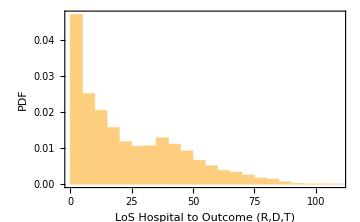

```mathematica
Histogram[timeHOutcomeRDT,Automatic,"PDF",FrameLabel->{"LoS Hospital to Outcome (R,D,T)","PDF"},Frame->True,ImageSize->Medium]
```

```mathematica
outcomes=dataBaseAnlysis1[[2;;,{7,8,9}]]/.{{x_,y_,z_}/;x>0&&z>0->"T",{x_,y_,z_}/;x>0&&y>0->"D",{x_,y_,z_}/;y>0&&z>0->"NA",{"NA","NA","NA"}->"NA",{0,0,0}->"NA",{x_,"NA","NA"}->"R",{"NA",x_,"NA"}->"D",{"NA","NA",x_}->"T"}
```

{R,R,R,R,R,R,R,R,T,R,T,R,R,R,T,T,T,NA,T,D,R,R,T,T,NA,T,D,R,R,T,R,R,R,D,R,R,R,R,T,R,D,R,R,NA,R,R,R,T,T,NA,T,NA,R,NA,R,R,R,R,R,R,T,R,R,T,R,R,R,NA,R,R,R,R,T,R,R,R,R,R,D,R,NA,R,R,T,R,NA,R,NA,NA,D,R,R,R,T,NA,R,R,T,R,T,R,R,R,T,T,R,R,T,R,43913,R,R,R,R,R,D,R,R,R,R,R,R,R,R,R,R,R,R,D,R,R,R,R,R,D,D,D,D,D,D,D,D,R,D,D,D,D,R,D,D,D,D,D,D,D,D,D,D,D,D,D,NA,NA,D,D,D,D,D,D,D,NA,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,R,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,NA,D}
 |  |  |  |

```mathematica
outcomeHR=outcomes/.{"R"->1,"D"->0,"T"->0};
```

```mathematica
outcomeHD=outcomes/.{"R"->0,"D"->1,"T"->0};
```

```mathematica
outcomeHT=outcomes/.{"R"->0,"D"->0,"T"->1};
```

```mathematica
(**********************************************************************************************************)
```

```mathematica
Position[dataBaseAnlysis1[[2;;,{10,11,12}]],{x_,y_,z_}/;x>0&&z>0](* gente que tiene fecha en recuperado y transferido from H *)
```

{{15},{23},{39},{76},{100},{102},{104},{107},{124},{131},{132},{150},{239},{300},{325},{345},{390},{438},{506},{572},{604},{1019},{1065},{1077},{1109},{1208},{1291},{1357},{1401},{1408},{1499},{1547},{1568},{1636},{1765},{1876},{1910},{1935},{1995},{2012},{2089},{2145},{2191},{2211},{2231},{2270},{2300},{2514},{2516},{2536},{2539},{2655},{2671},{2702},{2717},{2748},{2766},{2802},{2850},{2892},{2924},{2948},{3148},{3266},{3277},{3336},{3368},{3399},{3429},{3436},{3462},{3463},{3507},{3609},{3611},{3612},{3621},{3634},{3722},{3779},{3855},{3858},{3889},{3904},{3918},{3995},{4036},{4042},{4048},{4057},{4152},{4167},{4190},{4263},{4276},{4293},{4370},{4371},{4422},{4438},{4539},{4590},{4661},{4751},{4753},{4815},{4910},{4923},{4957},{5020},{5023},{5068},{5373},{5503},{5505},{5534},{5547},{5590},{5984},{6147},{6560},{6897},{7017},{7315},{8017},{8126},{8233},{8313},{9600},{10189},{10420},{10691},{10728},{11033},{11071},{11406},{11451},{11732},{12815},{12865},{12867},{13227},{13356},{13360},{13534},{13632},{13670},{13718},{13720},{13867},{13994},{14182},{14530},{14711},{14793},{14811},{14984},{15022},{15042},{15334},{15463},{15465},{15769},{15930},{16028},{16048},{16159},{16194},{16214},{16288},{16788},{16871},{16924},{16945},{17048},{17244},{17276},{17331},{17352},{17412},{17476},{18029},{18049},{18260},{18395},{18400},{18498},{18796},{23363},{23387},{23420},{25144},{28940},{29075},{31757},{33684},{33965},{35879},{36369},{36718},{36811},{36846},{36882},{36894},{37257},{37407},{37489},{37834},{38492},{38535},{38804},{39053},{39067},{39543},{41004},{41221}}

```mathematica
dataBase12020[[{1,16,24,103,1548,2703,3635,3856,4752,4816,8234,15466,17413,36370,38536}]]//Grid (* PARA ESTOS CASOS SE PONE EL TIEMPO AL EVENTO que ocurrió mas rápido*)
```

ID | Age | Gender | Ethnicity | AdHospital | RecoveryH | DeceasedH | transferredICU | AdICU | RecoveryICU | DeceasedICU | transferredH
15 | 69 | M | 3 | Wed 18 Mar 2020 | Wed 25 Mar 2020 |  | Fri 17 Apr 2020 | Thu 26 Mar 2020 | Sat 18 Apr 2020 |  | Thu 16 Apr 2020
23 | 26 | F | 3 | Thu 26 Mar 2020 |  |  | Wed 1 Apr 2020 | Wed 1 Apr 2020 | Fri 10 Apr 2020 |  | Thu 2 Apr 2020
102 | 62 | M | 3 | Wed 22 Apr 2020 | Thu 23 Apr 2020 |  |  | Sun 29 Mar 2020 | Sat 18 Apr 2020 |  | Wed 22 Apr 2020
1547 | 23 | M | 3 | Thu 21 May 2020 |  |  | Fri 22 May 2020 | Thu 7 May 2020 | Wed 27 May 2020 |  | Thu 21 May 2020
2702 | 0.75 | M | 3 | Thu 21 May 2020 |  |  | Fri 22 May 2020 | Mon 18 May 2020 | Mon 25 May 2020 |  | Thu 21 May 2020
3634 | 47 | M | 5 | Sun 19 Jul 2020 | Thu 30 Jul 2020 |  |  | Thu 28 May 2020 | Sun 28 Jun 2020 |  | Sun 19 Jul 2020
3855 | 45 | M | 2 | Fri 29 May 2020 | Mon 10 Aug 2020 |  | Fri 5 Jun 2020 | Fri 5 Jun 2020 | Sun 28 Jun 2020 |  | Fri 7 Aug 2020
4751 | 43 | M | 2 | Fri 7 Aug 2020 | Mon 10 Aug 2020 |  |  | Thu 4 Jun 2020 | Sun 28 Jun 2020 |  | Fri 7 Aug 2020
4815 | 63 | F | 3 | Fri 7 Aug 2020 | Mon 10 Aug 2020 |  |  | Fri 5 Jun 2020 | Sun 28 Jun 2020 |  | Fri 7 Aug 2020
8233 | 48 | F | 3 | Sat 20 Jun 2020 | Thu 24 Sep 2020 |  | Mon 22 Jun 2020 | Mon 22 Jun 2020 | Sat 5 Sep 2020 |  | Fri 26 Jun 2020
15465 | 58 | F | 3 | Fri 10 Jul 2020 |  |  | Mon 20 Jul 2020 | Mon 20 Jul 2020 | Fri 4 Sep 2020 |  | Fri 7 Aug 2020
17412 | 31 | M | 3 | Tue 14 Jul 2020 |  |  | Sun 19 Jul 2020 | Sun 19 Jul 2020 | Fri 4 Sep 2020 |  | Fri 7 Aug 2020
36369 | 69 | M | 3 | Fri 21 Aug 2020 |  |  | Thu 27 Aug 2020 | Thu 27 Aug 2020 | Wed 9 Sep 2020 |  | Sat 29 Aug 2020
38535 | 35 | F | 3 | Thu 27 Aug 2020 |  |  | Tue 1 Sep 2020 | Tue 1 Sep 2020 | Thu 17 Sep 2020 |  | Wed 2 Sep 2020

```mathematica
Position[dataBaseAnlysis1[[2;;,{10,11,12}]],{x_,y_,z_}/;x>0&&y>0](* gente que tiene fecha en recuperado y muerto from H *)
```

{{68},{108},{154},{361},{1029},{1033},{1078},{1262},{1306},{1362},{1474},{1536},{1597},{1609},{1688},{1755},{1859},{1884},{1888},{1910},{1965},{1969},{2120},{2266},{2317},{2374},{2568},{2575},{2655},{2711},{2854},{2930},{2962},{3271},{3994},{4254},{4270},{4571},{4715},{5078},{5941},{6742},{7091},{7799},{8368},{8822},{9136},{9199},{9685},{12362},{12742},{13269},{18215},{19159},{21367},{26539},{26843},{29920}}

```mathematica
dataBase12020[[{1,109,1263,2855,3272,3995,4716,5079,9686,19160,21368,29921}]]//Grid  (* PARA ESTOS CASOS SE PONE EL TIEMPO AL EVENTO D *)
```

ID | Age | Gender | Ethnicity | AdHospital | RecoveryH | DeceasedH | transferredICU | AdICU | RecoveryICU | DeceasedICU | transferredH
108 | 80 | M | 3 | Wed 1 Apr 2020 |  |  | Thu 2 Apr 2020 | Thu 2 Apr 2020 | Wed 15 Apr 2020 | Sat 25 Apr 2020 | 
1262 | 22 | M | 2 |  |  |  |  | Mon 4 May 2020 | Thu 21 May 2020 | Thu 4 Jun 2020 | 
2854 | 59 | M | 3 |  |  |  |  | Tue 19 May 2020 | Thu 21 May 2020 | Wed 27 May 2020 | 
3271 | 82 | M | 3 |  |  |  |  | Wed 27 May 2020 | Sun 28 Jun 2020 | Mon 13 Jul 2020 | 
3994 | 62 | M | 3 | Sat 30 May 2020 |  |  | Tue 2 Jun 2020 | Tue 2 Jun 2020 | Sun 28 Jun 2020 | Wed 1 Jul 2020 | 
4715 | 51 | M | 3 |  |  |  |  | Mon 8 Jun 2020 | Sun 28 Jun 2020 | Sun 12 Jul 2020 | 
5078 | 64 | M | 3 |  |  |  |  | Sat 6 Jun 2020 | Sun 28 Jun 2020 | Wed 29 Jul 2020 | 
9685 | 48 | M | 2 |  |  |  |  | Mon 20 Jul 2020 | Sat 5 Sep 2020 | Mon 7 Sep 2020 | 
19159 | 36 | F | 3 | Sat 18 Jul 2020 |  |  | Wed 19 Aug 2020 | Wed 19 Aug 2020 | Sat 5 Sep 2020 | Wed 23 Sep 2020 | 
21367 | 50 | M | 3 | Wed 22 Jul 2020 |  |  | Fri 7 Aug 2020 | Fri 7 Aug 2020 | Sat 5 Sep 2020 | Sun 27 Sep 2020 | 
29920 | 48 | M | 3 | Tue 4 Aug 2020 |  |  | Wed 19 Aug 2020 | Wed 19 Aug 2020 | Sat 5 Sep 2020 | Fri 18 Sep 2020 |

```mathematica
Position[dataBaseAnlysis1[[2;;,{10,11,12}]],{x_,y_,z_}/;y>0&&z>0](* gente que tiene fecha en  muerto y transferido from H *)
```

{{116},{814},{982},{1075},{1223},{1507},{1904},{1910},{2192},{2599},{2635},{2655},{2791},{4986},{5002},{5115},{8079},{10660},{12617},{14268},{17209},{27148},{27284},{31386},{36782},{36849},{36891},{36927},{36982},{37002},{37019},{37026},{37255},{37397},{37511},{37571},{37628},{37629},{37668},{37684},{37801},{37805},{38042},{38119},{38207},{38213},{38914},{38974},{39013},{39182},{39335},{39364},{39453},{39562},{39785},{40658},{40794},{41568}}

```mathematica
dataBase12020[[{1,1224,2193,4987,37630,37669,38208,39183,39563}]]//Grid (* ESTOS CASOS PUEDEN SER CONFUSOS Y SE ELIMINARAN COMO NAs EN LAS COLUMNAS DE INGRESO Y OUTCOME H*)
```

ID | Age | Gender | Ethnicity | AdHospital | RecoveryH | DeceasedH | transferredICU | AdICU | RecoveryICU | DeceasedICU | transferredH
1223 | 50 | F | 3 | Wed 27 May 2020 | Mon 1 Jun 2020 |  |  | Mon 4 May 2020 |  | Thu 21 May 2020 | Wed 27 May 2020
2192 | 80 | M | 2 | Thu 14 May 2020 |  |  | Tue 19 May 2020 | Tue 19 May 2020 |  | Fri 5 Jun 2020 | Thu 21 May 2020
4986 | 52 | M | 3 | Mon 8 Jun 2020 |  |  | Wed 10 Jun 2020 | Sat 6 Jun 2020 |  | Thu 11 Jun 2020 | Mon 8 Jun 2020
37629 | 84 | M | 3 | Tue 25 Aug 2020 |  |  | Fri 4 Sep 2020 | Fri 4 Sep 2020 |  | Tue 15 Sep 2020 | Sun 6 Sep 2020
37668 | 61 | F | 3 | Tue 25 Aug 2020 |  |  | Fri 4 Sep 2020 | Fri 4 Sep 2020 |  | Sun 13 Sep 2020 | Sun 6 Sep 2020
38207 | 69 | M | 3 | Wed 26 Aug 2020 |  |  | Tue 1 Sep 2020 | Tue 1 Sep 2020 |  | Fri 11 Sep 2020 | Wed 2 Sep 2020
39182 | 83 | M | 3 | Wed 2 Sep 2020 |  |  | Sun 6 Sep 2020 | Sat 29 Aug 2020 |  | Thu 17 Sep 2020 | Wed 2 Sep 2020
39562 | 63 | M | 3 | Wed 2 Sep 2020 |  |  | Thu 3 Sep 2020 | Tue 1 Sep 2020 |  | Sun 20 Sep 2020 | Wed 2 Sep 2020

```mathematica
Count[dataBaseAnlysis1[[2;;,{10,11,12}]],{"NA","NA","NA"}](* los que no ingresaron al H también SE ELIMINARAN COMO NAs EN LAS COLUMNAS DE INGRESO Y OUTCOME H *)
```

8

```mathematica
Position[dataBaseAnlysis1[[2;;,{10,11,12}]],{0,0,0}][[;;20]](* los que no ingresaron al H también SE ELIMINARAN COMO NAs EN LAS COLUMNAS DE INGRESO Y OUTCOME H *)
```

{{1},{2},{3},{4},{5},{6},{7},{8},{10},{12},{13},{14},{20},{22},{27},{28},{29},{31},{33},{34}}

```mathematica
dataBase12020[[{1,2,3,5,35}]]//Grid
```

ID | Age | Gender | Ethnicity | AdHospital | RecoveryH | DeceasedH | transferredICU | AdICU | RecoveryICU | DeceasedICU | transferredH
1 | 34 | M | 2 | Sun 15 Mar 2020 | Mon 23 Mar 2020 |  |  |  |  |  | 
2 | 85 | F | 3 | Sun 15 Mar 2020 | Mon 23 Mar 2020 |  |  |  |  |  | 
4 | 68 | F | 3 | Sun 15 Mar 2020 | Wed 25 Mar 2020 |  |  |  |  |  | 
34 | 59 | F | 3 | Sun 22 Mar 2020 |  | Thu 26 Mar 2020 |  |  |  |  |

```mathematica
timeICUOutcomeRDT=dataBaseAnlysis1[[2;;,{10,11,12}]]/.{{x_,y_,z_}/;x>0&&z>0->Min[z,x],{x_,y_,z_}/;x>0&&y>0->y,{x_,y_,z_}/;y>0&&z>0->"NA",{"NA","NA","NA"}->"NA",{0,0,0}->"NA",{x_,"NA","NA"}->x,{"NA",x_,"NA"}->x,{"NA","NA",x_}->x}
```

{NA,NA,NA,NA,NA,NA,NA,NA,3,NA,17,NA,NA,NA,21,6,6,11,12,NA,19,NA,1,11,3,17,NA,NA,NA,13,NA,21,NA,NA,NA,NA,NA,NA,17,6,NA,NA,NA,5,NA,NA,NA,11,21,1,7,17,NA,28,28,NA,NA,NA,NA,NA,22,NA,NA,7,NA,NA,21,78,NA,NA,NA,NA,2,NA,NA,22,NA,NA,NA,NA,13,NA,NA,1,NA,1,19,17,6,NA,NA,NA,NA,15,7,NA,NA,1,NA,43933,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,3,1,NA,NA,NA,NA,NA,NA,NA,1,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,1,NA}
 |  |  |  |

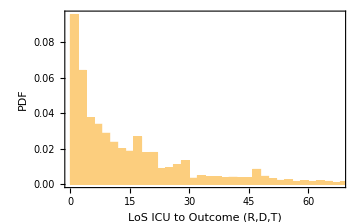

```mathematica
Histogram[timeICUOutcomeRDT,Automatic,"PDF",FrameLabel->{"LoS ICU to Outcome (R,D,T)","PDF"},Frame->True,ImageSize->Medium]
```

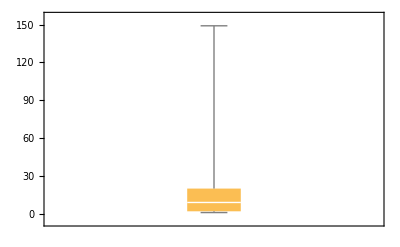

```mathematica
BoxWhiskerChart[timeICUOutcomeRDT]
```

```mathematica
outcomes2=dataBaseAnlysis1[[2;;,{10,11,12}]]/.{{x_,y_,z_}/;x>0&&z>0->"T",{x_,y_,z_}/;x>0&&y>0->"D",{x_,y_,z_}/;y>0&&z>0->"NA",{"NA","NA","NA"}->"NA",{0,0,0}->"NA",{x_,"NA","NA"}->"R",{"NA",x_,"NA"}->"D",{"NA","NA",x_}->"T"};
```

```mathematica
outcomeICUR=outcomes2/.{"R"->1,"D"->0,"T"->0};
```

```mathematica
outcomeICUD=outcomes2/.{"R"->0,"D"->1,"T"->0};
```

```mathematica
outcomeICUT=outcomes2/.{"R"->0,"D"->0,"T"->1};
```

```mathematica
(*******************************************************)
```

```mathematica
dataBaseAnlysis2={{"ID","AgeYears","AgeGroupOMS","AgeGroupVerka","Gender","weekAdmission","timeHOutcomeRDT","outcomeHR","outcomeHD","outcomeHT","timeICUOutcomeRDT","outcomeICUR","outcomeICUD","outcomeICUT"},Sequence@@Transpose[{dataBaseAnlysis1[[2;;,1]],dataBaseAnlysis1[[2;;,2]],omsAge,verkaAge,dataBase12020[[2;;,3]],weekAd,timeHOutcomeRDT,outcomeHR,outcomeHD,outcomeHT,timeICUOutcomeRDT,outcomeICUR,outcomeICUD,outcomeICUT}]};
```

```mathematica
SetDirectory["/home/lina/Documents/datos_INS"]
```

/home/lina/Documents/datos_INS

```mathematica
Export["dataBaseAnlysis2.csv",dataBaseAnlysis2]
```

dataBaseAnlysis2.csv

```mathematica
dataBaseAnlysis2=Import["dataBaseAnlysis2.csv"];
```

```mathematica
dataBaseAnlysis2[[1;;3]]
```

{{ID,AgeYears,AgeGroupOMS,AgeGroupVerka,Gender,weekAdmission,timeHOutcomeRDT,outcomeHR,outcomeHD,outcomeHT,timeICUOutcomeRDT,outcomeICUR,outcomeICUD,outcomeICUT},{1,34,5,1,M,2,8,1,0,0,NA,NA,NA,NA},{2,85,6,4,F,2,8,1,0,0,NA,NA,NA,NA}}

```mathematica
dataBaseAnlysis2[[1;;7]]//Grid
```

ID | AgeYears | AgeGroupOMS | AgeGroupVerka | Gender | weekAdmission | timeHOutcomeRDT | outcomeHR | outcomeHD | outcomeHT | timeICUOutcomeRDT | outcomeICUR | outcomeICUD | outcomeICUT
1 | 34 | 5 | 1 | M | 2 | 8 | 1 | 0 | 0 | NA | NA | NA | NA
2 | 85 | 6 | 4 | F | 2 | 8 | 1 | 0 | 0 | NA | NA | NA | NA
3 | 74 | 6 | 3 | F | 2 | 10 | 1 | 0 | 0 | NA | NA | NA | NA
4 | 68 | 6 | 3 | F | 2 | 10 | 1 | 0 | 0 | NA | NA | NA | NA
5 | 48 | 5 | 1 | M | 2 | 3 | 1 | 0 | 0 | NA | NA | NA | NA
6 | 61 | 6 | 2 | F | 3 | 11 | 1 | 0 | 0 | NA | NA | NA | NA

```mathematica
dataBaseAnlysis3=Flatten/@Transpose[{dataBaseAnlysis2[[All,1;;6]],{"monthAdmission",Sequence@@monthAd},dataBaseAnlysis2[[All,7;;-1]]}];
```

```mathematica
dataBaseAnlysis3[[1;;7]]//Grid
```

ID | AgeYears | AgeGroupOMS | AgeGroupVerka | Gender | weekAdmission | monthAdmission | timeHOutcomeRDT | outcomeHR | outcomeHD | outcomeHT | timeICUOutcomeRDT | outcomeICUR | outcomeICUD | outcomeICUT
1 | 34 | 5 | 1 | M | 2 | 1 | 8 | 1 | 0 | 0 | NA | NA | NA | NA
2 | 85 | 6 | 4 | F | 2 | 1 | 8 | 1 | 0 | 0 | NA | NA | NA | NA
3 | 74 | 6 | 3 | F | 2 | 1 | 10 | 1 | 0 | 0 | NA | NA | NA | NA
4 | 68 | 6 | 3 | F | 2 | 1 | 10 | 1 | 0 | 0 | NA | NA | NA | NA
5 | 48 | 5 | 1 | M | 2 | 1 | 3 | 1 | 0 | 0 | NA | NA | NA | NA
6 | 61 | 6 | 2 | F | 3 | 1 | 11 | 1 | 0 | 0 | NA | NA | NA | NA

```mathematica
Export["dataBaseAnlysis2.csv",dataBaseAnlysis3](*la exportaré como base de dato 2 para no llenarme de diferentes numeros por pequeños cambios como agregar una nueva columna*)
```

dataBaseAnlysis2.csv

### DataBase 3

```mathematica
(*Al igual que en la DataBase 2, aqui se organiza bien los tiempos al outcome*)
```

```mathematica
dataBaseAnlysis3=Import["/home/lina/Documents/datos_INS/dataBaseAnlysis3temporal.csv"];
```

```mathematica
dataBaseAnlysis3={{"ID","AgeYears","AgeGroupOMS","AgeGroupVerka","Gender","monthAdmission","timeHR","timeHD","timeHT","timeUCIR","timeUCID","timeUCIT","OutcomeD","OutcomeR"},Sequence@@Transpose[{Range[44132,44131+(dataBase[[2;;,1]]//Length)],dataBase[[2;;,2]],omsAge,verkaAge,dataBase[[2;;,3]],monthAd,tiempoHR,tiempoHD,tiempoHT,tiempoUCIR,tiempoUCID,tiempoUCIT,recovered1,deceased1}]};
```

```mathematica
dataBaseAnlysis3[[1;;20]]//Grid
```

ID | AgeYears | AgeGroupOMS | AgeGroupVerka | Gender | monthAdmission | timeHR | timeHD | timeHT | timeUCIR | timeUCID | timeUCIT | OutcomeD | OutcomeR
44132 | 29 | 5 | 1 | M | 12 | 0 | 0 | 0 | 89 | NA | NA | 1 | 0
44133 | 30 | 5 | 1 | M | 11 | 0 | 0 | 0 | 7 | NA | NA | 1 | 0
44134 | 32 | 5 | 1 | M | 11 | 5 | NA | NA | 0 | 0 | 0 | 1 | 0
44135 | 37 | 5 | 1 | F | 11 | 0 | 0 | 0 | 3 | NA | NA | 1 | 0
44136 | 39 | 5 | 1 | F | 11 | 41 | NA | NA | 0 | 0 | 0 | 1 | 0
44137 | 40 | 5 | 1 | F | 12 | 0 | 0 | 0 | 9 | NA | NA | 1 | 0
44138 | 41 | 5 | 1 | M | 11 | 0 | 0 | 0 | 2 | NA | NA | 1 | 0
44139 | 44 | 5 | 1 | F | 12 | 54 | NA | NA | 0 | 0 | 0 | 1 | 0
44140 | 45 | 5 | 1 | F | 12 | 1 | NA | NA | 0 | 0 | 0 | 1 | 0
44141 | 47 | 5 | 1 | M | 11 | 13 | NA | NA | 0 | 0 | 0 | 1 | 0
44142 | 48 | 5 | 1 | M | 11 | 6 | NA | NA | 0 | 0 | 0 | 1 | 0
44143 | 51 | 5 | 2 | F | 11 | 36 | NA | NA | 0 | 0 | 0 | 1 | 0
44144 | 51 | 5 | 2 | F | 12 | 59 | NA | NA | 0 | 0 | 0 | 1 | 0
44145 | 51 | 5 | 2 | F | 11 | NA | NA | 16 | 25 | NA | NA | 1 | 0
44146 | 51 | 5 | 2 | M | 11 | 0 | 0 | 0 | 15 | NA | NA | 1 | 0
44147 | 51 | 5 | 2 | M | 11 | 41 | NA | NA | 0 | 0 | 0 | 1 | 0
44148 | 51 | 5 | 2 | M | 11 | 42 | NA | NA | 0 | 0 | 0 | 1 | 0
44149 | 53 | 5 | 2 | F | 12 | 1 | NA | NA | 0 | 0 | 0 | 1 | 0
44150 | 53 | 5 | 2 | M | 11 | 16 | NA | NA | 0 | 0 | 0 | 1 | 0

```mathematica
dataBaseAnlysis3[[-1]]
```

{119492,10996,85,6,4,M,14,NA,1,NA,0,0,0,0,1}

```mathematica
Export["/home/lina/Documents/datos_INS/dataBaseAnlysis3temporal.csv",dataBaseAnlysis3]
```

/home/lina/Documents/datos_INS/dataBaseAnlysis3temporal.csv

```mathematica
dataBaseAnlysis3[[1]]//PositionIndex
```

<|ID→{1},AgeYears→{2},AgeGroupOMS→{3},AgeGroupVerka→{4},Gender→{5},monthAdmission→{6},timeHR→{7},timeHD→{8},timeHT→{9},timeUCIR→{10},timeUCID→{11},timeUCIT→{12},OutcomeD→{13},OutcomeR→{14}|>

```mathematica
dataBaseAnlysis3[[2;;,{7,8,9}]]//DeleteDuplicates
```

{{0,0,0},{5,NA,NA},{41,NA,NA},{54,NA,NA},{1,NA,NA},{13,NA,NA},{6,NA,NA},{36,NA,NA},{59,NA,NA},{NA,NA,16},{42,NA,NA},{16,NA,NA},{NA,NA,14},{93,NA,NA},{3,NA,NA},{2,NA,NA},{30,NA,NA},{51,NA,NA},{56,NA,NA},{14,NA,NA},{20,NA,NA},{52,NA,NA},{NA,NA,1},{24,NA,NA},{NA,9,NA},{4,NA,NA},{NA,2,NA},{12,NA,NA},{NA,NA,4},{9,NA,NA},{NA,1,NA},{NA,10,NA},{48,NA,NA},{NA,7,NA},{NA,6,NA},{67,NA,NA},{NA,23,NA},{84,NA,NA},{40,NA,NA},{62,NA,NA},{28,NA,NA},{NA,26,NA},{58,NA,NA},{28,NA,2},{10,NA,NA},{NA,19,NA},{34,NA,NA},{NA,NA,6},{NA,4,NA},{11,NA,NA},{57,NA,NA},{NA,NA,19},{127,NA,NA},{129,NA,NA},{120,NA,NA},{7,NA,NA},{63,NA,NA},{73,NA,NA},{94,NA,NA},{25,NA,NA},{86,NA,NA},{110,NA,NA},{11,NA,4},{98,NA,NA},{96,NA,NA},{91,NA,NA},{95,NA,NA},{NA,3,NA},{NA,16,NA},{126,NA,NA},{NA,5,NA},{NA,NA,21},{128,NA,NA},{8,NA,NA},{NA,12,NA},{NA,21,NA},{NA,8,NA},{NA,15,NA},{106,NA,NA},{107,NA,NA},{71,NA,NA},{50,NA,NA},{64,NA,NA},{68,NA,NA},{85,NA,NA},{70,NA,NA},{47,NA,NA},{102,NA,NA},{NA,22,NA},{101,NA,NA},{103,NA,NA},{104,NA,NA},{NA,13,NA},{27,NA,NA},{99,NA,13},{100,NA,NA},{61,NA,NA},{108,NA,NA},{122,NA,NA},{18,NA,NA},{NA,57,NA},{97,NA,NA},{NA,29,NA},{NA,NA,15},{NA,11,NA},{NA,NA,2},{89,NA,3},{19,NA,NA},{31,NA,NA},{26,NA,NA},{21,NA,NA},{NA,25,NA},{69,NA,NA},{44,NA,NA},{89,NA,NA},{130,NA,NA},{NA,20,NA},{57,NA,21},{45,NA,NA},{NA,38,NA},{29,NA,NA},{77,NA,NA},{33,NA,NA},{NA,18,NA},{NA,NA,22},{125,NA,NA},{NA,34,NA},{49,NA,NA},{15,NA,NA},{NA,17,NA},{NA,67,NA},{75,NA,NA},{46,NA,NA},{17,NA,NA},{32,NA,NA},{37,NA,NA},{50,NA,2},{NA,NA,13},{NA,NA,3},{61,NA,3},{11,NA,2},{NA,NA,17},{55,NA,NA},{72,NA,NA},{53,NA,NA},{105,NA,NA},{88,NA,NA},{23,NA,NA},{80,NA,NA},{NA,NA,20},{NA,30,NA},{43,NA,NA},{NA,54,NA},{99,NA,NA},{92,NA,NA},{90,NA,NA},{NA,55,NA},{34,NA,3},{24,NA,13},{39,NA,NA},{NA,28,NA},{76,NA,NA},{22,NA,NA},{NA,14,NA},{65,NA,NA},{18,NA,16},{NA,NA,11},{51,NA,10},{41,NA,1},{82,NA,NA},{16,NA,3},{112,NA,NA},{38,NA,NA},{12,NA,3},{28,NA,3},{124,NA,NA},{37,NA,13},{74,NA,NA},{35,NA,NA},{NA,52,NA},{137,NA,NA},{NA,NA,8},{NA,NA,5},{139,NA,NA},{123,NA,NA},{NA,NA,32},{83,NA,NA},{43,NA,2},{113,NA,NA},{NA,56,NA},{55,NA,1},{81,NA,NA},{78,NA,NA},{NA,NA,18},{5,21,NA},{66,NA,NA},{117,NA,NA},{NA,NA,27},{111,NA,NA},{NA,42,NA},{NA,53,18},{NA,NA,12},{136,NA,NA},{46,NA,18},{138,NA,NA},{116,NA,NA},{135,NA,NA},{79,NA,NA},{NA,24,NA},{50,NA,17},{NA,NA,10},{NA,35,NA},{NA,27,NA},{121,NA,NA},{119,NA,NA},{109,NA,NA},{NA,37,NA},{NA,51,NA},{134,NA,NA},{98,NA,12},{NA,NA,9},{NA,12,3},{44,NA,16},{NA,111,NA},{61,NA,10},{NA,NA,29},{87,NA,NA},{NA,NA,40},{124,NA,15},{114,NA,NA},{22,NA,8},{133,NA,NA},{19,NA,8},{NA,41,NA},{27,NA,11},{NA,NA,25},{9,NA,1},{27,NA,2},{49,NA,2},{123,NA,3},{123,NA,10},{12,NA,8},{123,NA,8},{21,NA,8},{NA,NA,7},{NA,68,10},{132,NA,NA},{NA,31,NA},{16,NA,14},{118,NA,NA},{115,NA,NA},{NA,NA,30},{131,NA,NA},{17,NA,13},{NA,NA,45},{149,NA,NA},{60,NA,NA},{14,NA,2},{27,NA,3},{8,NA,1},{142,NA,NA},{NA,NA,24},{141,NA,NA},{NA,NA,26},{23,NA,2},{43,NA,1},{47,NA,24},{67,NA,24},{35,NA,4},{20,NA,4},{140,NA,NA},{152,NA,NA},{27,NA,1},{84,NA,6},{108,NA,4},{53,NA,10},{150,NA,NA},{NA,44,NA},{159,NA,NA},{133,NA,8},{44,NA,2},{NA,NA,23},{64,NA,6},{148,NA,NA},{158,NA,NA},{30,NA,7},{7,NA,4},{47,NA,20},{47,NA,1},{15,NA,7},{78,NA,1},{157,NA,NA},{56,NA,2},{31,NA,6},{52,NA,1},{3,NA,1},{23,NA,6},{123,NA,12},{156,NA,NA},{NA,39,NA},{NA,NA,156},{21,NA,1},{10,NA,5},{21,NA,4},{155,NA,NA},{29,NA,17},{NA,87,NA},{18,NA,4},{10,NA,1},{NA,60,NA},{NA,139,NA},{154,NA,NA},{42,NA,5},{57,NA,16},{NA,32,NA},{153,NA,NA},{146,NA,NA},{38,NA,1},{25,NA,4},{NA,10,1},{64,NA,11},{NA,NA,153},{145,NA,NA},{22,NA,6},{NA,62,NA},{108,NA,5},{17,NA,4},{151,NA,NA},{23,NA,13},{NA,59,NA},{31,NA,13},{114,NA,7},{5,NA,1},{54,NA,3},{44,NA,4},{49,NA,12},{76,NA,3},{19,NA,7},{NA,114,NA},{42,NA,1},{4,NA,1},{147,NA,NA},{NA,117,NA},{20,NA,10},{21,NA,2},{NA,21,2},{16,NA,5},{19,NA,2},{NA,71,NA},{18,NA,8},{10,NA,6},{144,NA,NA},{NA,109,NA},{84,NA,3},{11,NA,1},{18,NA,7},{14,NA,6},{41,NA,7},{29,NA,3},{20,NA,3},{41,NA,3},{144,NA,16},{135,NA,7},{30,NA,3},{143,NA,NA},{7,NA,1},{32,NA,8},{16,NA,4},{39,NA,8},{61,NA,6},{14,NA,4},{NA,16,11},{NA,NA,142},{NA,17,8},{22,NA,2},{22,NA,1},{17,NA,8},{30,NA,2},{94,NA,11},{13,NA,2},{9,NA,2},{13,NA,6},{13,NA,1},{24,NA,6},{23,NA,8},{23,NA,12},{13,NA,5},{24,NA,4},{12,NA,7},{NA,70,NA},{NA,79,NA},{12,NA,5},{21,NA,3},{24,NA,1},{37,NA,7},{8,NA,4},{NA,43,NA},{NA,36,NA},{NA,11,3},{45,NA,8},{45,NA,7},{39,NA,11},{NA,31,4},{NA,58,NA},{124,NA,5},{24,NA,12},{25,NA,16},{NA,3,1},{NA,45,NA},{31,NA,9},{NA,47,NA},{NA,53,NA},{29,NA,12},{20,NA,11},{NA,48,NA},{NA,10,8},{109,NA,1},{37,NA,10},{40,NA,10},{26,NA,9},{22,NA,3},{11,NA,9},{78,NA,2},{31,NA,11},{6,NA,4},{NA,119,NA},{93,NA,6},{110,NA,2},{39,NA,5},{15,NA,1},{25,NA,9},{18,NA,9},{15,NA,6},{119,NA,9},{28,NA,8},{112,NA,5},{12,NA,2},{20,NA,5},{14,NA,9},{14,NA,1},{114,NA,3},{NA,72,NA},{27,NA,5},{25,NA,1},{6,NA,1},{55,NA,2},{34,NA,1},{8,NA,6},{NA,78,NA},{15,NA,5},{18,NA,6},{20,NA,6},{38,NA,3},{20,NA,8},{2,NA,6},{18,NA,5},{19,NA,6},{NA,33,NA},{NA,27,17},{16,NA,6},{44,NA,31},{10,NA,7},{NA,NA,34},{16,NA,7},{NA,66,NA},{7,NA,11},{14,NA,8},{4,NA,2},{13,NA,11},{8,NA,5},{1,NA,3},{112,NA,17},{NA,16,10},{NA,97,NA},{NA,NA,33},{NA,NA,51},{33,NA,9},{45,NA,9},{32,NA,9},{15,NA,9},{111,NA,10},{106,NA,3},{28,NA,5},{26,NA,4},{31,NA,1},{112,NA,8},{10,NA,8},{115,NA,10},{13,NA,8},{58,NA,1},{NA,5,1},{NA,68,NA},{111,NA,11},{NA,93,NA},{27,NA,9},{26,NA,11},{113,NA,10},{10,NA,2},{NA,4,2},{103,NA,3},{12,NA,9},{NA,NA,70},{82,NA,1},{108,NA,81},{111,NA,9},{111,NA,22},{NA,49,NA},{98,NA,15},{65,NA,9},{18,NA,1},{111,NA,49},{111,NA,12},{35,NA,8},{93,NA,9},{5,NA,2},{26,NA,2},{109,NA,9},{102,NA,6},{NA,50,NA},{109,NA,7},{36,NA,7},{109,NA,6},{105,NA,19},{20,NA,18},{85,NA,12},{105,NA,8},{NA,74,NA},{29,NA,8},{17,NA,2},{107,NA,45},{100,NA,9},{49,NA,5},{100,NA,2},{NA,40,NA},{107,NA,8},{20,NA,17},{20,NA,2},{46,NA,7},{63,NA,16},{106,NA,4},{23,NA,3},{107,NA,7},{86,NA,1},{93,NA,8},{100,NA,10},{NA,NA,52},{50,NA,28},{32,NA,2},{27,NA,12},{97,NA,1},{17,NA,6},{12,NA,4},{53,NA,5},{101,NA,9},{99,NA,8},{85,NA,1},{28,NA,14},{104,NA,17},{104,NA,4},{96,NA,5},{45,NA,14},{23,NA,14},{103,NA,13},{104,NA,13},{18,NA,13},{104,NA,41},{86,NA,9},{103,NA,16},{21,NA,13},{NA,15,1},{47,NA,2},{94,NA,5},{103,NA,15},{28,NA,1},{102,NA,12},{15,NA,8},{23,NA,11},{20,NA,12},{17,NA,12},{25,NA,12},{18,NA,12},{8,NA,2},{NA,25,12},{85,NA,6},{93,NA,3},{103,NA,11},{100,NA,11},{101,NA,11},{22,NA,14},{NA,64,NA},{100,NA,15},{19,NA,1},{84,NA,27},{103,NA,10},{NA,29,10},{102,NA,10},{101,NA,10},{85,NA,3},{99,NA,10},{97,NA,10},{15,NA,10},{7,NA,2},{30,NA,10},{103,NA,97},{NA,75,NA},{100,NA,37},{97,NA,4},{9,NA,7},{NA,NA,46},{NA,25,4},{68,NA,3},{100,NA,13},{13,NA,9},{88,NA,1},{84,NA,2},{45,NA,1},{81,NA,5},{100,NA,41},{17,NA,7},{28,NA,7},{87,NA,1},{66,NA,5},{98,NA,34},{97,NA,8},{96,NA,7},{NA,10,2},{NA,NA,38},{NA,13,1},{27,NA,6},{23,NA,5},{97,NA,6},{95,NA,6},{85,NA,2},{97,NA,7},{7,NA,3},{6,NA,2},{NA,9,3},{12,NA,1},{76,NA,1},{5,NA,3},{83,NA,10},{102,NA,7},{91,NA,2},{95,NA,2},{97,NA,5},{96,NA,6},{95,NA,38},{53,NA,2},{91,NA,27},{94,NA,8},{84,NA,1},{NA,NA,31},{38,NA,2},{NA,NA,59},{17,NA,3},{89,NA,4},{86,NA,2},{101,NA,6},{9,NA,18},{90,NA,8},{NA,15,3},{99,NA,6},{94,NA,6},{13,NA,4},{NA,76,NA},{95,NA,7},{98,NA,7},{92,NA,7},{86,NA,4},{89,NA,1},{81,NA,3},{32,NA,4},{25,NA,3},{18,NA,3},{NA,18,1},{92,NA,34},{90,NA,1},{86,NA,20},{85,NA,21},{8,NA,3},{81,NA,17},{93,NA,27},{12,NA,6},{58,NA,2},{28,NA,21},{NA,11,1},{NA,9,1},{81,NA,1},{83,NA,19},{NA,NA,28},{89,NA,21},{89,NA,26},{17,NA,1},{NA,30,1},{47,NA,28},{14,NA,7},{81,NA,16},{84,NA,16},{NA,23,17},{89,NA,7},{90,NA,6},{90,NA,25},{84,NA,18},{94,NA,24},{94,NA,7},{86,NA,6},{13,NA,3},{87,NA,22},{36,NA,1},{25,NA,11},{NA,28,9},{19,NA,10},{NA,23,6},{90,NA,20},{29,NA,1},{NA,NA,43},{65,NA,1},{90,NA,61},{46,NA,27},{27,NA,4},{21,NA,7},{96,NA,67},{50,NA,4},{89,NA,60},{10,NA,4},{NA,9,4},{9,NA,4},{2,NA,18},{75,NA,11},{NA,37,6},{88,NA,59},{19,NA,13},{NA,22,6},{9,NA,3},{17,NA,9},{23,NA,4},{93,NA,64},{21,NA,5},{24,NA,8},{26,NA,10},{NA,33,3},{24,NA,3},{NA,46,NA},{82,NA,53},{24,NA,10},{19,NA,5},{46,NA,5},{91,NA,62},{75,NA,16},{52,NA,5},{80,NA,51},{NA,NA,49},{92,NA,61},{74,NA,10},{40,NA,5},{NA,NA,44},{41,NA,6},{90,NA,59},{NA,11,4},{NA,21,9},{NA,18,3},{NA,65,NA},{47,NA,5},{53,NA,3},{57,NA,44},{50,NA,1},{65,NA,4},{40,NA,4},{31,NA,3},{NA,NA,56},{32,NA,7},{NA,6,3},{22,NA,5},{NA,NA,48},{86,NA,55},{68,NA,16},{NA,22,1},{85,NA,54},{30,NA,15},{74,NA,62},{31,NA,2},{48,NA,2},{1,18,NA},{43,NA,27},{62,NA,14},{52,NA,2},{49,NA,4},{24,NA,9},{28,NA,6},{39,NA,7},{NA,7,3},{15,NA,3},{62,NA,6},{NA,17,1},{67,NA,15},{47,NA,29},{42,NA,3},{49,NA,8},{35,NA,14},{46,NA,25},{78,NA,5},{NA,73,NA},{31,NA,4},{NA,24,4},{25,NA,7},{NA,NA,NA},{50,NA,3},{25,2,NA},{47,NA,3},{NA,18,8},{NA,NA,39},{20,NA,1},{67,NA,20},{32,NA,5},{16,NA,2},{66,NA,19},{40,NA,3},{38,NA,20},{37,NA,19},{59,NA,10},{36,NA,3},{32,NA,16},{38,NA,17},{39,NA,17},{33,NA,17},{36,NA,10},{66,NA,17},{NA,61,NA},{56,NA,16},{34,NA,16},{34,NA,15},{43,NA,14},{11,NA,5},{NA,NA,60},{55,NA,8},{53,NA,13},{57,NA,8},{41,NA,12},{54,NA,7},{51,NA,12},{40,NA,1},{37,NA,11},{26,NA,8},{39,NA,1},{48,NA,1},{56,NA,9},{42,NA,9},{36,NA,9},{NA,11,2},{56,NA,7},{44,NA,23},{52,NA,6},{50,NA,6},{43,NA,41},{NA,NA,36},{29,NA,2},{46,NA,2},{30,NA,1},{14,NA,5},{26,NA,5},{19,NA,3},{33,NA,2},{31,NA,12},{NA,7,2},{15,NA,2},{17,NA,5},{NA,22,20},{15,NA,4},{16,NA,1},{14,NA,3},{NA,5,2},{28,NA,19},{NA,8,2},{NA,13,5},{NA,4,1},{NA,16,2},{24,NA,2},{15,NA,12},{NA,13,7},{NA,7,5},{NA,7,1},{NA,19,8},{11,NA,7},{NA,10,7}}

```mathematica
Position[dataBaseAnlysis3[[2;;,{7,8,9}]],{x_,y_,z_}/;x>0&&z>0](* gente que tiene fecha en recuperado y transferido from H *)
```

{{97},{181},{327},{418},{472},{678},{698},{710},{1008},{1021},{1185},{1222},{1247},{1285},{1398},{1420},{1432},{1434},{1568},{1891},{2014},{2072},{2535},{2699},{2827},{3393},{3533},{3695},{3969},{4131},{4171},{4203},{4341},{4346},{4397},{4529},{4548},{4609},{4612},{4621},{4696},{5156},{5490},{5648},{5710},{6176},{6207},{6219},{6230},{6275},{6276},{6493},{6604},{6643},{6767},{7032},{7056},{7272},{7311},{7513},{7566},{7606},{7615},{7777},{7878},{7892},{7955},{8008},{8146},{8165},{8201},{8213},{8264},{8454},{8471},{8527},{8616},{8684},{8685},{8973},{9009},{9107},{9169},{9171},{9211},{9236},{9369},{9422},{9522},{9672},{9701},{9735},{9828},{9921},{10066},{10114},{10239},{10329},{10334},{10401},{10542},{10582},{10732},{10815},{10928},{10942},{10994},{11105},{11111},{11169},{11207},{11235},{11263},{11288},{11300},{11321},{11346},{11367},{11392},{11405},{11412},{11426},{11491},{11527},{11529},{11536},{11558},{11649},{11663},{11700},{11701},{11794},{11810},{11999},{12000},{12029},{12034},{12080},{12284},{12304},{12377},{12430},{12431},{12513},{12534},{12559},{12580},{12648},{12764},{12876},{13020},{13181},{13219},{13270},{13332},{13669},{13769},{13899},{14056},{14091},{14133},{14137},{14228},{14564},{14886},{14972},{15003},{15146},{15209},{15217},{15303},{15422},{15425},{15463},{15481},{15658},{15931},{16030},{16063},{16170},{16204},{16239},{16334},{16442},{16449},{16497},{16528},{16608},{16616},{16622},{16627},{16640},{16665},{16748},{16750},{17014},{17023},{17026},{17052},{17072},{17133},{17134},{17342},{17346},{17354},{17359},{17377},{17406},{17409},{17443},{17446},{17455},{17600},{17605},{17613},{17620},{17636},{17683},{17815},{17872},{18021},{18045},{18284},{18323},{18412},{18580},{18846},{18896},{18943},{19060},{19073},{19091},{19102},{19107},{19133},{19135},{19137},{19141},{19573},{19584},{19607},{19610},{19618},{19635},{19746},{19774},{19799},{19803},{19808},{19814},{19962},{19984},{20114},{20181},{20185},{20192},{20465},{20467},{20715},{21151},{21289},{21423},{21429},{21482},{21489},{21531},{21589},{21844},{21897},{22157},{22178},{22237},{22264},{22293},{22440},{22447},{22449},{22711},{22750},{22786},{22826},{22842},{22868},{22899},{22900},{22910},{22928},{22936},{23014},{23040},{23044},{23078},{23081},{23129},{23136},{23140},{23169},{23407},{23438},{23529},{23557},{23706},{23738},{23739},{23884},{23947},{23977},{24014},{24042},{24086},{24236},{24245},{24252},{24380},{24404},{24423},{24469},{24492},{24798},{24975},{25039},{25077},{25101},{25138},{25155},{25212},{25226},{25245},{25332},{25336},{25364},{25532},{25538},{25556},{25570},{25611},{25671},{25684},{26022},{26030},{26037},{26065},{26136},{26166},{26180},{26274},{26525},{26542},{26643},{26655},{26691},{26696},{26727},{26740},{26779},{26803},{26847},{26901},{26949},{26986},{27003},{27101},{27162},{27491},{27518},{27520},{27526},{27531},{27535},{27595},{27652},{27661},{27810},{27921},{27972},{28047},{28048},{28118},{28218},{28296},{28322},{28419},{28434},{28453},{28457},{28463},{28523},{28564},{28610},{28613},{28688},{28693},{28712},{28830},{28844},{29011},{29070},{29113},{29217},{29248},{29274},{29312},{29374},{29492},{29499},{29557},{29648},{29649},{29671},{29679},{29794},{30006},{30107},{30157},{30167},{30271},{30328},{30418},{30427},{30477},{30481},{30539},{30583},{30592},{30755},{30780},{31001},{31048},{31152},{31242},{31266},{31307},{31351},{31358},{31410},{31452},{31496},{31499},{31676},{31752},{31777},{31831},{31921},{31945},{32085},{32174},{32213},{32332},{32360},{32411},{32459},{32473},{32527},{32534},{32721},{32724},{32726},{32732},{32789},{32914},{32922},{32923},{33015},{33017},{33075},{33082},{33083},{33173},{33211},{33317},{33470},{33504},{33509},{33575},{33614},{33643},{33661},{33665},{33684},{33715},{33759},{33760},{33807},{33850},{33881},{33908},{33910},{33916},{33953},{34017},{34085},{34101},{34115},{34228},{34402},{34419},{34425},{34435},{34439},{34519},{34541},{34636},{34689},{34766},{34870},{34881},{35035},{35156},{35200},{35202},{35203},{35334},{35500},{35524},{35561},{35604},{35701},{35715},{35741},{35757},{35788},{36157},{36211},{36216},{36231},{36351},{36386},{36402},{36404},{36496},{36536},{36571},{36584},{36847},{37000},{37114},{37120},{37138},{37303},{37410},{37538},{37606},{37609},{37615},{37694},{37819},{37863},{37874},{37966},{38027},{38043},{38214},{38287},{38290},{38421},{38446},{38511},{38532},{38545},{38675},{38785},{38810},{39025},{39207},{39213},{39339},{39390},{39438},{39446},{39477},{39692},{39786},{39833},{39841},{39871},{40447},{40534},{40755},{40841},{41196},{41365},{41404},{41418},{41639},{41751},{41928},{42047},{42216},{42227},{42577},{42705},{43202},{43265},{43435},{43464},{43470},{43583},{43685},{43701},{43709},{43760},{43771},{43795},{43819},{43867},{43936},{44227},{44253},{44314},{44370},{44479},{44491},{44499},{44694},{44707},{44718},{44751},{44814},{44941},{44963},{44973},{44980},{44989},{45027},{45099},{45117},{45485},{45555},{45675},{45698},{45875},{46025},{46220},{46269},{46274},{46381},{46461},{46535},{46626},{46883},{47085},{47115},{47219},{47452},{47547},{47775},{48298},{48581},{48832},{48879},{48882},{48966},{49152},{49197},{49236},{49473},{49530},{49556},{49565},{49694},{49703},{50041},{50044},{50299},{50322},{50373},{50468},{50514},{50617},{50655},{50666},{50684},{50701},{50719},{50779},{50794},{51023},{51130},{51139},{51199},{51233},{51254},{51300},{51759},{52319},{52324},{52334},{52416},{52562},{52610},{52718},{52865},{53026},{53066},{53131},{53195},{53364},{53433},{53434},{53626},{53732},{53837},{53848},{53965},{53996},{54004},{54008},{54162},{54292},{54528},{54735},{54751},{54831},{54883},{54891},{55774},{55881},{55882},{56078},{56204},{56310},{56769},{56803},{56825},{56829},{56990},{57086},{57447},{57648},{57806},{57840},{58080},{58383},{58404},{58451},{58481},{58522},{58598},{58617},{58618},{58652},{58660},{58668},{58752},{58762},{58786},{58799},{58816},{58832},{58844},{59097},{59218},{59232},{59236},{59299},{59327},{59560},{59587},{59667},{59674},{59750},{59793},{59798},{59801},{59805},{59832},{59962},{60149},{60158},{60178},{60243},{60297},{60342},{60642},{60664},{60811},{60909},{61111},{61136},{61160},{61208},{61229},{61340},{61513},{61563},{61596},{61997},{62037},{62042},{62111},{62193},{62198},{62300},{62376},{62390},{62415},{62488},{62523},{62648},{62651},{62702},{62719},{62831},{62988},{62993},{63029},{63042},{63062},{63117},{63188},{63382},{63444},{63500},{64052},{64131},{64316},{64351},{64379},{64429},{64436},{64568},{64722},{64810},{64958},{65336},{65405},{65471},{65696},{65904},{66117},{66121},{66174},{66485},{66567},{66925},{66948},{67189},{67416},{67538},{67656},{67933},{68061},{68234},{68400},{68466},{68708},{68954},{69146},{69226},{69319},{69358},{69424},{69567},{69581},{69598},{69692},{70129},{70648},{70649},{70896},{71389},{71408},{71687},{71715},{71783},{72215},{72728},{72761},{73230},{73894},{73907},{74058},{74110},{74112},{74123},{74350},{74352},{74358},{74679},{74712},{75012}}

```mathematica
dataBaseAnlysis3[[2;;,{1,7,8,9}]][[30]]
```

{44161,0,0,0}

```mathematica
dataBase[[{1,72215+1,54162+1,49236+1,44989+1,33173+1,39841+1,33017+1,75012+1}]]//Grid (* PARA ESTOS CASOS SE PONE EL TIEMPO AL EVENTO T *)
```

ID | Age | Gender | Ethnicity | AdHospital | RecoveryH | DeceasedH | transferredICU | AdICU | RecoveryICU | DeceasedICU | transferredH
116346 | 74 | M | 3 | Thu 11 Mar 2021 | Sat 20 Mar 2021 |  | Mon 15 Mar 2021 | Mon 15 Mar 2021 |  |  | Thu 18 Mar 2021
98293 | 28 | M | 3 | Tue 22 Jun 2021 | Tue 20 Jul 2021 |  | Fri 25 Jun 2021 | Fri 4 Jun 2021 |  |  | Tue 22 Jun 2021
93367 | 61 | M | 3 | Mon 17 May 2021 | Sat 29 May 2021 |  | Sat 22 May 2021 | Sat 22 May 2021 |  |  | Sun 23 May 2021
89120 | 49 | M | 3 | Tue 11 May 2021 | Wed 30 Jun 2021 |  | Sat 15 May 2021 | Sat 15 May 2021 |  |  | Sat 29 May 2021
77304 | 48 | M | 3 | Wed 28 Apr 2021 | Sun 2 May 2021 |  | Thu 29 Apr 2021 | Tue 27 Apr 2021 |  |  | Wed 28 Apr 2021
83972 | 45 | M | 3 | Sun 9 May 2021 | Wed 26 May 2021 |  | Sat 22 May 2021 | Sat 22 May 2021 |  |  | Sun 23 May 2021
77148 | 54 | F | 3 | Thu 22 Apr 2021 | Wed 28 Jul 2021 |  | Thu 29 Apr 2021 | Thu 29 Apr 2021 |  |  | Tue 27 Jul 2021
119143 | 86 | F | 3 | Sun 28 Mar 2021 | Mon 5 Apr 2021 |  | Mon 29 Mar 2021 | Mon 29 Mar 2021 |  |  | Wed 31 Mar 2021

```mathematica
newOldID=Transpose[{dataBase12021[[2;;,1]],casesHICUDefOut}]
```

{{44132,1949724},{44133,1949769},{44134,1949828},{44135,1949936},{44136,1949994},{44137,1950025},{44138,1950063},{44139,1950140},{44140,1950169},{44141,1950217},{44142,1950239},{44143,1950282},{44144,1950285},{44145,1950289},{44146,1950290},{44147,1950291},{44148,1950294},{44149,1950329},{44150,1950337},{44151,1950366},{44152,1950397},{44153,1950403},{44154,1950412},{44155,1950413},75314,{119470,4860540},{119471,4860836},{119472,4860951},{119473,4860986},{119474,4861269},{119475,4861497},{119476,4861588},{119477,4863046},{119478,4864779},{119479,4864799},{119480,4864890},{119481,4864993},{119482,4865137},{119483,4865286},{119484,4865330},{119485,4865377},{119486,4865472},{119487,4866625},{119488,4867893},{119489,4867901},{119490,4867998},{119491,4868224},{119492,4870035}}
 |  |  |  |

```mathematica
(******************************************)
```

```mathematica
newOldID[[15]](* el caso 44146 es la posicion "1950290"+1 en una base original del INS*)
```

{44146,1950290}

```mathematica
{dataBase[[1]],Select[dataBase,#[[1]]==44146& ][[1]]}//Grid
```

ID | Age | Gender | Ethnicity | AdHospital | RecoveryH | DeceasedH | transferredICU | AdICU | RecoveryICU | DeceasedICU | transferredH
44146 | 51 | M | 3 |  |  |  |  | Sun 24 Jan 2021 | Mon 8 Feb 2021 |  |

```mathematica
case1=Import["/home/lina/Documents/datos_INS/2021-01-23.csv"];
```

```mathematica
case1[[1,{1,1950290+1}]]//Grid
```

```mathematica
case2=Import["/home/lina/Documents/datos_INS/2021-01-24.csv"];
```

```mathematica
case2[[{1,1950290+1}]]//Grid
```

fecha_hoy_casos | Caso | Fecha Not | Departamento | Departamento_nom | Ciudad_municipio | Ciudad_municipio_nom | Edad | unidad_medida | Sexo | Fuente_tipo_contagio | Ubicacion | Estado | Pais_viajo_1_cod | Pais_viajo_1_nom | Recuperado | Fecha_inicio_sintomas | Fecha_muerte | Fecha_diagnostico | Fecha_recuperado | Tipo_recuperacion | per_etn_ | nom_grupo_
20/1/2021 0:00:00 | 1950330 | 20/1/2021 0:00:00 | 11 | BOGOTA | 11001 | BOGOTA | 51 | 1 | M | En estudio | Hospital UCI | Grave |  |  | Recuperado | 7/1/2021 0:00:00 |  | 19/1/2021 0:00:00 | 24/1/2021 0:00:00 | Tiempo | 6 |

```mathematica
case3=Import["/home/lina/Documents/datos_INS/2021-02-07.csv"];
```

```mathematica
case3[[{1,1950290+1}]]//Grid
```

fecha_hoy_casos | Caso | Fecha Not | Departamento | Departamento_nom | Ciudad_municipio | Ciudad_municipio_nom | Edad | unidad_medida | Sexo | Fuente_tipo_contagio | Ubicacion | Estado | Pais_viajo_1_cod | Pais_viajo_1_nom | Recuperado | Fecha_inicio_sintomas | Fecha_muerte | Fecha_diagnostico | Fecha_recuperado | Tipo_recuperacion | per_etn_ | nom_grupo_
20/1/2021 0:00:00 | 1950330 | 20/1/2021 0:00:00 | 11 | BOGOTA | 11001 | BOGOTA | 51 | 1 | M | En estudio | Hospital UCI | Grave |  |  | Activo | 7/1/2021 0:00:00 |  | 19/1/2021 0:00:00 |  |  | 6 |

```mathematica
case4=Import["/home/lina/Documents/datos_INS/2021-02-08.csv"];
```

```mathematica
case4[[{1,1950290+1}]]//Grid
```

fecha_hoy_casos | Caso | Fecha Not | Departamento | Departamento_nom | Ciudad_municipio | Ciudad_municipio_nom | Edad | unidad_medida | Sexo | Fuente_tipo_contagio | Ubicacion | Estado | Pais_viajo_1_cod | Pais_viajo_1_nom | Recuperado | Fecha_inicio_sintomas | Fecha_muerte | Fecha_diagnostico | Fecha_recuperado | Tipo_recuperacion | per_etn_ | nom_grupo_
20/1/2021 0:00:00 | 1950330 | 20/1/2021 0:00:00 | 11 | BOGOTA | 11001 | BOGOTA | 51 | 1 | M | En estudio | Casa | Leve |  |  | Activo | 7/1/2021 0:00:00 |  | 19/1/2021 0:00:00 |  |  | 6 |

```mathematica
(****)
```

```mathematica
newOldID[[1005]](* el caso 44146 es la posicion "1950290"+1 en una base original del INS*)
```

{45136,1975270}

```mathematica
{dataBase[[1]],Select[dataBase,#[[1]]==45136& ][[1]]}//Grid
```

ID | Age | Gender | Ethnicity | AdHospital | RecoveryH | DeceasedH | transferredICU | AdICU | RecoveryICU | DeceasedICU | transferredH
45136 | 23 | M | 3 | Fri 22 Jan 2021 | Sun 9 May 2021 |  |  |  |  |  |

```mathematica
case5=Import["/home/lina/Documents/datos_INS/2021-01-22.csv"];
```

```mathematica
case5[[{1,1975270+1}]]//Grid
```

fecha_hoy_casos | Caso | Fecha Not | Departamento | Departamento_nom | Ciudad_municipio | Ciudad_municipio_nom | Edad | unidad_medida | Sexo | Fuente_tipo_contagio | Ubicacion | Estado | Pais_viajo_1_cod | Pais_viajo_1_nom | Recuperado | Fecha_inicio_sintomas | Fecha_muerte | Fecha_diagnostico | Fecha_recuperado | Tipo_recuperacion | per_etn_ | nom_grupo_
22/1/2021 0:00:00 | 19275310 | 18/1/2021 0:00:00 | 20 | CESAR | 20060 | BOSCONIA | 23 | 1 | M | En estudio | Hospital | Moderado |  |  | Activo | 12/1/2021 0:00:00 |  | 20/1/2021 0:00:00 |  |  |  |

```mathematica
case6=Import["/home/lina/Documents/datos_INS/2021-05-08.csv"];
```

```mathematica
case6[[{1,1975270+1}]]//Grid
```

fecha_hoy_casos | Caso | Fecha Not | Departamento | Departamento_nom | Ciudad_municipio | Ciudad_municipio_nom | Edad | unidad_medida | Sexo | Fuente_tipo_contagio | Ubicacion | Estado | Pais_viajo_1_cod | Pais_viajo_1_nom | Recuperado | Fecha_inicio_sintomas | Fecha_muerte | Fecha_diagnostico | Fecha_recuperado | Tipo_recuperacion | per_etn_ | nom_grupo_
22/1/2021 0:00:00 | 1975310 | 18/1/2021 0:00:00 | 20 | CESAR | 20060 | BOSCONIA | 23 | 1 | M | En estudio | Hospital | Moderado |  |  | Activo | 12/1/2021 0:00:00 |  | 20/1/2021 0:00:00 |  |  | 6 |

```mathematica
case7=Import["/home/lina/Documents/datos_INS/2021-05-09.csv"];
```

```mathematica
case7[[{1,1975270+1}]]//Grid
```

fecha_hoy_casos | Caso | Fecha Not | Departamento | Departamento_nom | Ciudad_municipio | Ciudad_municipio_nom | Edad | unidad_medida | Sexo | Fuente_tipo_contagio | Ubicacion | Estado | Pais_viajo_1_cod | Pais_viajo_1_nom | Recuperado | Fecha_inicio_sintomas | Fecha_muerte | Fecha_diagnostico | Fecha_recuperado | Tipo_recuperacion | per_etn_ | nom_grupo_
22/1/2021 0:00:00 | 1975310 | 18/1/2021 0:00:00 | 20 | CESAR | 20060 | BOSCONIA | 23 | 1 | M | En estudio | Casa  | Leve |  |  | Activo | 12/1/2021 0:00:00 |  | 20/1/2021 0:00:00 |  |  | 6 |

```mathematica
(****************************************************************************+++++)
```

```mathematica
Position[dataBaseAnlysis3[[2;;,{7,8,9}]],{x_,y_,z_}/;x>0&&y>0](* gente que tiene fecha en recuperado y muerto from H *)
```

{{2198},{51251},{56863}}

```mathematica
dataBase12021[[{1,2198+1,51251+1,56863+1}]]//Grid  (* PARA ESTOS CASOS SE PONE EL TIEMPO AL EVENTO D *)
```

ID | Age | Gender | Ethnicity | AdHospital | RecoveryH | DeceasedH | transferredICU | AdICU | RecoveryICU | DeceasedICU | transferredH
46329 | 36 | M | 3 | Sun 24 Jan 2021 | Fri 29 Jan 2021 | Sun 14 Feb 2021 |  |  |  |  | 
95382 | 56 | M | 3 | Mon 31 May 2021 | Tue 1 Jun 2021 | Fri 18 Jun 2021 |  |  |  |  | 
100994 | 74 | F | 3 | Wed 2 Jun 2021 | Sun 27 Jun 2021 | Fri 4 Jun 2021 |  |  |  |  |

```mathematica
(***********************************************************************************+)
```

```mathematica
Position[dataBaseAnlysis3[[2;;,{7,8,9}]],{x_,y_,z_}/;y>0&&z>0](* gente que tiene fecha en  muerto y transferido from H *)
```

{{2520},{3482},{4639},{9215},{10825},{11740},{11787},{13659},{13915},{14175},{15186},{18090},{19197},{21706},{22299},{27754},{28537},{29365},{30452},{32393},{32478},{33118},{34714},{36385},{37685},{37821},{38312},{38548},{39060},{39084},{40906},{41374},{43706},{43981},{44369},{45658},{48861},{48880},{48928},{50121},{50674},{53035},{53428},{55867},{57190},{62371},{63278},{63715},{63750},{66791},{68227},{69126},{70090},{70730},{70792},{71197},{71254},{73419},{73436},{73457},{73819},{74069},{74256},{74919}}

```mathematica
dataBase12021[[{1,3482+1,32393+1,48880+1,71254+1}]]//Grid  (* ESTOS CASOS PUEDEN SER CONFUSOS Y SE ELIMINARAN COMO NAs EN LAS COLUMNAS DE INGRESO Y OUTCOME H*)
```

ID | Age | Gender | Ethnicity | AdHospital | RecoveryH | DeceasedH | transferredICU | AdICU | RecoveryICU | DeceasedICU | transferredH
47613 | 64 | F | 3 | Thu 18 Feb 2021 |  | Tue 2 Mar 2021 | Sun 21 Feb 2021 | Fri 5 Feb 2021 | Tue 9 Feb 2021 |  | Wed 24 Feb 2021
76524 | 65 | M | 3 | Wed 21 Apr 2021 |  | Sat 1 May 2021 | Fri 23 Apr 2021 | Fri 23 Apr 2021 |  |  | Wed 28 Apr 2021
93011 | 60 | M | 3 | Tue 25 May 2021 |  | Tue 15 Jun 2021 | Thu 3 Jun 2021 | Thu 3 Jun 2021 |  |  | Fri 11 Jun 2021
115385 | 78 | F | 3 | Sun 7 Mar 2021 |  | Tue 23 Mar 2021 | Tue 9 Mar 2021 | Tue 9 Mar 2021 |  |  | Wed 10 Mar 2021

```mathematica
Count[dataBaseAnlysis3[[2;;,{7,8,9}]],{"NA","NA","NA"}](* los que no ingresaron al H también SE ELIMINARAN COMO NAs EN LAS COLUMNAS DE INGRESO Y OUTCOME H *)
```

2

```mathematica
Position[dataBaseAnlysis3[[2;;,{7,8,9}]],{0,0,0}][[;;20]](* los que no ingresaron al H también SE ELIMINARAN COMO NAs EN LAS COLUMNAS DE INGRESO Y OUTCOME H *)
```

{{1},{2},{4},{6},{7},{15},{30},{31},{36},{39},{49},{53},{58},{63},{64},{74},{75},{77},{81},{86}}

```mathematica
timeHOutcomeRDT=dataBaseAnlysis3[[2;;,{7,8,9}]]/.{{x_,y_,z_}/;x>0&&z>0->z,{x_,y_,z_}/;x>0&&y>0->y,{x_,y_,z_}/;y>0&&z>0->"NA",{"NA","NA","NA"}->"NA",{0,0,0}->"NA",{x_,"NA","NA"}->x,{"NA",x_,"NA"}->x,{"NA","NA",x_}->x}
```

{NA,NA,5,NA,41,NA,NA,54,1,13,6,36,59,16,NA,41,42,1,16,14,93,3,2,30,2,36,51,3,56,NA,NA,14,20,2,1,NA,52,5,NA,1,1,1,24,9,4,2,5,1,NA,4,2,12,NA,4,1,3,3,NA,9,1,1,4,NA,NA,2,10,48,1,3,6,2,7,6,NA,NA,67,NA,23,84,4,NA,40,62,28,14,NA,2,4,62,9,62,NA,NA,26,58,NA,2,10,19,34,58,10,1,84,58,6,NA,6,1,58,58,6,NA,6,6,1,2,1,36,NA,NA,1,1,4,11,2,NA,11,NA,1,20,57,1,19,36,NA,9,127,NA,NA,129,NA,127,129,129,NA,1,120,NA,NA,120,75059,1,1,4,1,3,4,1,1,7,NA,1,1,1,1,NA,5,1,6,NA,6,8,1,NA,NA,NA,1,1,1,1,6,1,1,NA,1,5,1,4,NA,NA,2,3,NA,2,3,3,3,1,1,3,NA,1,3,2,NA,1,NA,6,6,4,NA,NA,NA,NA,NA,5,5,NA,6,1,NA,NA,1,2,6,1,6,1,3,1,NA,1,5,1,5,1,1,NA,1,5,1,1,1,2,3,1,NA,5,1,NA,3,NA,3,1,5,5,1,NA,5,2,2,2,1,4,1,NA,5,2,1,NA,3,4,4,1,NA,NA,NA,1,3,2,1,NA,1,1,1,2,1,NA,NA,1,1,1,NA,1,1,1,1,1,NA,1,1,1}
 |  |  |  |

```mathematica
timeHOutcomeRDT//Length
```

75361

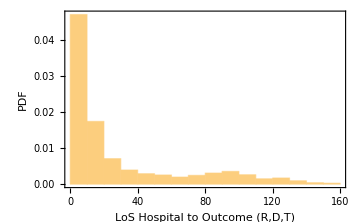

```mathematica
Histogram[timeHOutcomeRDT,Automatic,"PDF",FrameLabel->{"LoS Hospital to Outcome (R,D,T)","PDF"},Frame->True,ImageSize->Medium]
```

```mathematica
outcomes=dataBaseAnlysis3[[2;;,{7,8,9}]]/.{{x_,y_,z_}/;x>0&&z>0->"T",{x_,y_,z_}/;x>0&&y>0->"D",{x_,y_,z_}/;y>0&&z>0->"NA",{"NA","NA","NA"}->"NA",{0,0,0}->"NA",{x_,"NA","NA"}->"R",{"NA",x_,"NA"}->"D",{"NA","NA",x_}->"T"}
```

{NA,NA,R,NA,R,NA,NA,R,R,R,R,R,R,T,NA,R,R,R,R,T,R,R,R,R,R,R,R,R,R,NA,NA,R,R,R,R,NA,R,R,NA,T,T,T,R,D,R,D,R,T,NA,R,R,R,NA,T,T,R,R,NA,R,D,T,R,NA,NA,R,D,R,T,R,R,D,D,D,NA,NA,R,NA,D,R,R,NA,R,R,R,R,NA,R,R,R,R,R,NA,NA,D,R,NA,T,R,D,R,R,R,D,R,R,75152,D,D,NA,D,T,D,NA,D,NA,D,R,R,NA,NA,NA,NA,NA,R,R,NA,R,D,NA,NA,D,D,R,D,R,D,D,D,NA,D,D,D,R,D,D,NA,D,R,D,D,D,D,D,D,NA,R,D,NA,D,NA,D,D,R,D,D,NA,D,D,D,D,D,D,D,NA,D,D,D,NA,D,R,R,D,NA,NA,NA,D,D,D,D,NA,D,D,D,D,D,NA,NA,D,D,D,NA,D,D,D,D,D,NA,D,D,D}
 |  |  |  |

```mathematica
outcomeHR=outcomes/.{"R"->1,"D"->0,"T"->0};
```

```mathematica
outcomeHD=outcomes/.{"R"->0,"D"->1,"T"->0};
```

```mathematica
outcomeHT=outcomes/.{"R"->0,"D"->0,"T"->1};
```

```mathematica
(**********************************************************************************************************)
```

```mathematica
Position[dataBaseAnlysis3[[2;;,{10,11,12}]],{x_,y_,z_}/;x>0&&z>0](* gente que tiene fecha en recuperado y transferido from ICU *)
```

{{134},{3238},{3464},{3482},{3497},{3749},{3847},{4786},{4832},{6557},{7100},{7272},{7551},{7895},{7958},{8728},{9185},{9522},{9531},{9642},{10016},{10062},{10343},{10360},{10363},{10534},{10676},{10763},{10922},{10947},{10953},{11347},{11354},{11536},{11542},{12042},{12562},{12566},{13004},{13155},{13196},{14153},{14431},{14847},{14917},{14932},{14972},{15209},{15715},{15956},{16222},{16689},{16705},{17014},{17409},{17613},{17834},{17868},{18057},{18268},{18278},{18335},{18741},{19091},{19135},{19799},{19801},{19803},{19814},{19822},{20138},{20177},{20184},{20202},{20203},{20478},{20495},{21146},{21598},{21675},{21877},{21886},{22048},{22641},{22913},{22956},{22977},{23069},{23103},{23585},{23592},{23596},{23694},{23725},{23728},{23733},{24808},{24814},{24881},{24926},{24989},{25321},{25949},{26068},{26463},{26586},{26932},{27029},{27822},{27907},{28051},{28412},{28505},{28977},{29008},{29027},{29696},{29827},{30395},{30482},{30502},{30514},{31086},{31317},{31680},{31728},{31748},{31764},{31771},{32416},{32471},{32481},{33091},{33144},{33171},{33223},{33935},{33970},{34053},{34059},{34113},{34654},{34687},{34706},{34759},{35135},{35923},{36042},{36229},{36418},{36864},{37700},{38454},{38956},{39285},{39746},{39768},{39840},{40306},{40350},{40937},{41069},{41155},{41160},{41665},{42319},{42389},{42858},{43131},{43750},{43814},{44348},{44465},{44467},{44523},{44561},{44803},{45024},{45572},{46161},{46175},{47126},{47646},{47769},{48438},{48810},{48826},{48985},{49204},{49858},{50347},{50749},{51272},{51973},{51981},{53400},{53894},{54202},{54260},{54847},{54985},{55609},{55621},{56028},{56041},{56042},{56760},{56823},{56875},{56911},{57742},{58371},{58422},{58475},{58480},{58671},{58676},{58812},{58829},{58830},{58835},{59160},{59212},{59234},{59242},{59272},{59301},{59315},{59358},{59450},{59477},{59527},{60081},{60454},{60556},{60637},{60649},{60654},{61103},{61110},{61113},{61175},{61212},{61233},{62514},{62646},{63185},{63675},{66752},{67145},{67181},{67185},{67643},{67679},{69596},{70500},{70579},{71278},{72396},{72597},{72635},{73685},{73932},{74091},{74645}}

```mathematica
dataBase12021[[{1,41160+1,54260+1}]]//Grid (* PARA ESTOS CASOS SE PONE EL TIEMPO AL EVENTO que ocurrió mas rápido*)
```

ID | Age | Gender | Ethnicity | AdHospital | RecoveryH | DeceasedH | transferredICU | AdICU | RecoveryICU | DeceasedICU | transferredH
85291 | 71 | M | 3 | Mon 24 May 2021 |  |  | Sat 29 May 2021 | Sat 8 May 2021 | Tue 20 Jul 2021 |  | Mon 24 May 2021
98391 | 40 | M | 3 | Tue 22 Jun 2021 |  |  | Fri 25 Jun 2021 | Fri 4 Jun 2021 | Mon 28 Jun 2021 |  | Tue 22 Jun 2021

```mathematica
Position[dataBaseAnlysis3[[2;;,{10,11,12}]],{x_,y_,z_}/;x>0&&y>0](* gente que tiene fecha en recuperado y muerto from ICU *)
```

{{7818},{8120},{36392},{44558},{73263}}

```mathematica
dataBase12021[[{1,8120+1}]]//Grid  (* PARA ESTOS CASOS SE PONE EL TIEMPO AL EVENTO D *)
```

ID | Age | Gender | Ethnicity | AdHospital | RecoveryH | DeceasedH | transferredICU | AdICU | RecoveryICU | DeceasedICU | transferredH
52251 | 68 | M | 3 |  |  |  |  | Mon 8 Feb 2021 | Mon 15 Feb 2021 | Fri 19 Feb 2021 |

```mathematica
Position[dataBaseAnlysis3[[2;;,{10,11,12}]],{x_,y_,z_}/;y>0&&z>0](* gente que tiene fecha en  muerto y transferido from H *)
```

{{4473},{5465},{7837},{9823},{10544},{10818},{12240},{14946},{15137},{15139},{15578},{15754},{15781},{17006},{17387},{17437},{17830},{17872},{18272},{20194},{20518},{20590},{20648},{21257},{21543},{22947},{23583},{23671},{23676},{24187},{24300},{24863},{25923},{25936},{26067},{26597},{26606},{26960},{27006},{27164},{27797},{27890},{28683},{29044},{29102},{30485},{30720},{31092},{31829},{32399},{32462},{32472},{32567},{33351},{33458},{34054},{35445},{35632},{35641},{35759},{35889},{39201},{43444},{44320},{44870},{47665},{47966},{48330},{49238},{49619},{50627},{50734},{51871},{52298},{52362},{52492},{52814},{52836},{52920},{52939},{53918},{59314},{59716},{61152},{62507},{64602},{68225},{69240},{69794},{71866},{72524},{72777},{73047},{73450},{73701},{74849}}

```mathematica
dataBase12021[[{1,10818+1,30720+1}]]//Grid (* ESTOS CASOS PUEDEN SER CONFUSOS Y SE ELIMINARAN COMO NAs EN LAS COLUMNAS DE INGRESO Y OUTCOME H*)
```

ID | Age | Gender | Ethnicity | AdHospital | RecoveryH | DeceasedH | transferredICU | AdICU | RecoveryICU | DeceasedICU | transferredH
54949 | 79 | M | 3 | Tue 23 Feb 2021 |  |  | Thu 25 Feb 2021 | Thu 25 Feb 2021 |  | Wed 17 Mar 2021 | Fri 26 Feb 2021
74851 | 69 | M | 3 | Mon 26 Apr 2021 |  |  | Wed 28 Apr 2021 | Sun 25 Apr 2021 |  | Sun 9 May 2021 | Mon 26 Apr 2021

```mathematica
Count[dataBaseAnlysis3[[2;;,{10,11,12}]],{"NA","NA","NA"}](* los que no ingresaron al H también SE ELIMINARAN COMO NAs EN LAS COLUMNAS DE INGRESO Y OUTCOME H *)
```

1

```mathematica
Position[dataBaseAnlysis3[[2;;,{10,11,12}]],{0,0,0}][[;;20]](* los que no ingresaron al H también SE ELIMINARAN COMO NAs EN LAS COLUMNAS DE INGRESO Y OUTCOME H *)
```

{{3},{5},{8},{9},{10},{11},{12},{13},{16},{17},{18},{19},{21},{22},{23},{24},{25},{26},{27},{28}}

```mathematica
dataBase12021[[{1,2,3,5,35}]]//Grid
```

ID | Age | Gender | Ethnicity | AdHospital | RecoveryH | DeceasedH | transferredICU | AdICU | RecoveryICU | DeceasedICU | transferredH
44132 | 29 | M | 3 |  |  |  |  | Sun 14 Feb 2021 | Fri 14 May 2021 |  | 
44133 | 30 | M | 3 |  |  |  |  | Sun 24 Jan 2021 | Sun 31 Jan 2021 |  | 
44135 | 37 | F | 3 |  |  |  |  | Sat 30 Jan 2021 | Tue 2 Feb 2021 |  | 
44165 | 64 | F | 3 | Wed 27 Jan 2021 | Fri 29 Jan 2021 |  |  |  |  |  |

```mathematica
timeICUOutcomeRDT=dataBaseAnlysis3[[2;;,{10,11,12}]]/.{{x_,y_,z_}/;x>0&&z>0->Min[z,x],{x_,y_,z_}/;x>0&&y>0->y,{x_,y_,z_}/;y>0&&z>0->"NA",{"NA","NA","NA"}->"NA",{0,0,0}->"NA",{x_,"NA","NA"}->x,{"NA",x_,"NA"}->x,{"NA","NA",x_}->x}
```

{89,7,NA,3,NA,9,2,NA,NA,NA,NA,NA,NA,25,15,NA,NA,NA,NA,4,NA,NA,NA,NA,NA,NA,NA,NA,NA,42,22,NA,NA,NA,NA,12,NA,NA,10,41,23,15,NA,NA,NA,NA,NA,3,3,NA,NA,NA,2,13,21,NA,NA,4,NA,NA,24,NA,23,5,NA,NA,NA,3,NA,NA,NA,NA,NA,23,7,NA,2,NA,NA,NA,61,NA,NA,NA,NA,56,NA,NA,NA,NA,NA,12,11,NA,NA,1,24,NA,NA,NA,NA,NA,NA,NA,NA,75151,NA,NA,NA,3,NA,2,NA,1,NA,1,NA,NA,NA,1,6,5,5,4,NA,NA,5,NA,NA,1,4,NA,NA,NA,NA,NA,NA,NA,NA,4,NA,NA,NA,NA,NA,NA,1,NA,NA,NA,NA,NA,NA,NA,NA,3,NA,NA,1,NA,1,NA,NA,NA,NA,NA,1,NA,NA,NA,NA,NA,NA,NA,1,NA,NA,NA,1,NA,NA,NA,NA,1,2,1,NA,NA,NA,NA,1,NA,NA,NA,NA,NA,1,1,NA,NA,NA,1,NA,NA,NA,NA,NA,1,NA,NA,NA}
 |  |  |  |

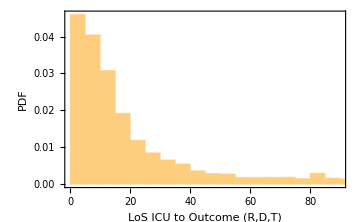

```mathematica
Histogram[timeICUOutcomeRDT,Automatic,"PDF",FrameLabel->{"LoS ICU to Outcome (R,D,T)","PDF"},Frame->True,ImageSize->Medium]
```

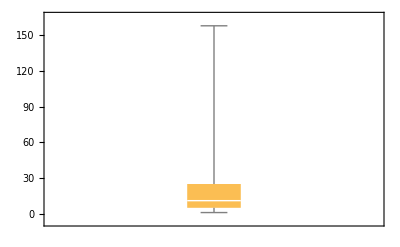

```mathematica
BoxWhiskerChart[timeICUOutcomeRDT]
```

```mathematica
outcomes2=dataBaseAnlysis3[[2;;,{10,11,12}]]/.{{x_,y_,z_}/;x>0&&z>0->"T",{x_,y_,z_}/;x>0&&y>0->"D",{x_,y_,z_}/;y>0&&z>0->"NA",{"NA","NA","NA"}->"NA",{0,0,0}->"NA",{x_,"NA","NA"}->"R",{"NA",x_,"NA"}->"D",{"NA","NA",x_}->"T"};
```

```mathematica
outcomeICUR=outcomes2/.{"R"->1,"D"->0,"T"->0};
```

```mathematica
outcomeICUD=outcomes2/.{"R"->0,"D"->1,"T"->0};
```

```mathematica
outcomeICUT=outcomes2/.{"R"->0,"D"->0,"T"->1};
```

```mathematica
(*******************************************************)
```

```mathematica
dataBaseAnlysis3[[1]]
```

{ID,AgeYears,AgeGroupOMS,AgeGroupVerka,Gender,monthAdmission,timeHR,timeHD,timeHT,timeUCIR,timeUCID,timeUCIT,OutcomeD,OutcomeR}

```mathematica
dataBaseAnlysis3nueva={{"ID","AgeYears","AgeGroupOMS","AgeGroupVerka","Gender","monthAdmission","timeHOutcomeRDT","outcomeHR","outcomeHD","outcomeHT","timeICUOutcomeRDT","outcomeICUR","outcomeICUD","outcomeICUT"},Sequence@@Transpose[{dataBaseAnlysis3[[2;;,1]],dataBaseAnlysis3[[2;;,2]],dataBaseAnlysis3[[2;;,3]],dataBaseAnlysis3[[2;;,4]],dataBaseAnlysis3[[2;;,5]],dataBaseAnlysis3[[2;;,6]],timeHOutcomeRDT,outcomeHR,outcomeHD,outcomeHT,timeICUOutcomeRDT,outcomeICUR,outcomeICUD,outcomeICUT}]};
```

```mathematica
Export["/home/lina/Documents/datos_INS/dataBaseAnlysis3.csv",dataBaseAnlysis3nueva]
```

/home/lina/Documents/datos_INS/dataBaseAnlysis3.csv

```mathematica
dataBaseAnlysis3=Import["/home/lina/Documents/datos_INS/dataBaseAnlysis3.csv"];
```

```mathematica
dataBaseAnlysis3[[1;;7]]//Grid
```

ID | AgeYears | AgeGroupOMS | AgeGroupVerka | Gender | monthAdmission | timeHOutcomeRDT | outcomeHR | outcomeHD | outcomeHT | timeICUOutcomeRDT | outcomeICUR | outcomeICUD | outcomeICUT
44132 | 29 | 5 | 1 | M | 12 | NA | NA | NA | NA | 89 | 1 | 0 | 0
44133 | 30 | 5 | 1 | M | 11 | NA | NA | NA | NA | 7 | 1 | 0 | 0
44134 | 32 | 5 | 1 | M | 11 | 5 | 1 | 0 | 0 | NA | NA | NA | NA
44135 | 37 | 5 | 1 | F | 11 | NA | NA | NA | NA | 3 | 1 | 0 | 0
44136 | 39 | 5 | 1 | F | 11 | 41 | 1 | 0 | 0 | NA | NA | NA | NA
44137 | 40 | 5 | 1 | F | 12 | NA | NA | NA | NA | 9 | 1 | 0 | 0

```mathematica
(*****************)
```

```mathematica
dataBase[[1]]
```

{ID,Age,Gender,Ethnicity,AdHospital,RecoveryH,DeceasedH,transferredICU,AdICU,RecoveryICU,DeceasedICU,transferredH}

```mathematica
newOldID[[10000]]
```

{54131,2180827}

```mathematica
Select[dataBase,#[[1]]==54131&]
```

{{54131,27,F,3,Fri 12 Feb 2021,Sat 29 May 2021,,,,,,}}

```mathematica
case6=Import["/home/lina/Documents/datos_INS/2021-02-12.csv"];
case6[[{1,2180827+1}]]//Grid
```

fecha_hoy_casos | Caso | Fecha Not | Departamento | Departamento_nom | Ciudad_municipio | Ciudad_municipio_nom | Edad | unidad_medida | Sexo | Fuente_tipo_contagio | Ubicacion | Estado | Pais_viajo_1_cod | Pais_viajo_1_nom | Recuperado | Fecha_inicio_sintomas | Fecha_muerte | Fecha_diagnostico | Fecha_recuperado | Tipo_recuperacion | per_etn_ | nom_grupo_
12/2/2021 0:00:00 | 2180867 | 28/12/2020 0:00:00 | 15 | BOYACA | 15755 | SOCOTA | 27 | 1 | F | En estudio | Hospital | Moderado |  |  | Activo | 28/12/2020 0:00:00 |  | 8/1/2021 0:00:00 |  |  |  |

```mathematica
newOldID[[50000]]
```

{94131,3152684}

```mathematica
Select[dataBase,#[[1]]==94131&]
```

{{94131,91,F,3,Mon 31 May 2021,Tue 1 Jun 2021,,,,,,}}

```mathematica
case6=Import["/home/lina/Documents/datos_INS/2021-05-31.csv"];
case6[[{1,3152684+1}]]//Grid
```

fecha_hoy_casos | Caso | Fecha Not | Departamento | Departamento_nom | Ciudad_municipio | Ciudad_municipio_nom | Edad | unidad_medida | Sexo | Fuente_tipo_contagio | Ubicacion | Estado | Pais_viajo_1_cod | Pais_viajo_1_nom | Recuperado | Fecha_inicio_sintomas | Fecha_muerte | Fecha_diagnostico | Fecha_recuperado | Tipo_recuperacion | per_etn_ | nom_grupo_
19/5/2021 0:00:00 | 3152724 | 14/5/2021 0:00:00 | 11 | BOGOTA | 11001 | BOGOTA | 91 | 1 | F | En estudio | Hospital | Moderado |  |  | Recuperado | 12/5/2021 0:00:00 |  | 18/5/2021 0:00:00 | 26/5/2021 0:00:00 | Tiempo | 6 |

```mathematica
case6=Import["/home/lina/Documents/datos_INS/2021-06-01.csv"];
case6[[{1,3152684+1}]]//Grid
```

fecha_hoy_casos | Caso | Fecha Not | Departamento | Departamento_nom | Ciudad_municipio | Ciudad_municipio_nom | Edad | unidad_medida | Sexo | Fuente_tipo_contagio | Ubicacion | Estado | Pais_viajo_1_cod | Pais_viajo_1_nom | Recuperado | Fecha_inicio_sintomas | Fecha_muerte | Fecha_diagnostico | Fecha_recuperado | Tipo_recuperacion | per_etn_ | nom_grupo_
19/5/2021 0:00:00 | 3152724 | 14/5/2021 0:00:00 | 11 | BOGOTA | 11001 | BOGOTA | 91 | 1 | F | En estudio | Casa | Leve |  |  | Recuperado | 12/5/2021 0:00:00 |  | 18/5/2021 0:00:00 | 26/5/2021 0:00:00 | Tiempo | 6 |

### DataBase 4

Here it is built a data base for all the INS variables of selected cases

```mathematica
masterMfechas2020=Import["/home/lina/Documents/datos_INS/masterM15-2020HUCIDefOutComplete2.m"];
```

```mathematica
masterMfechas0=Import["/home/lina/Documents/datos_INS/casesOutcomefechas_G3.m"];
```

```mathematica
masterMfechas1=Import["/home/lina/Documents/datos_INS/casesOutcomefechas_G4.m"];
```

```mathematica
masterMfechas2=Import["/home/lina/Documents/datos_INS/casesOutcomefechas_G5.m"];
```

```mathematica
masterMfechas2021=Join[masterMfechas0,masterMfechas1,Map[PadRight[#,Length[masterMfechas1[[1]]],x]&,masterMfechas2]/.x->{"",""}];
```

```mathematica
casesHICUDefOut2020=StringDrop[#,4]&/@masterMfechas2020[[All,1,2]](*Esto es para Eliminar la palabra caso de casoX*);
```

```mathematica
casesHICUDefOut2021=masterMfechas2021[[All,1,2]](*cuando no se nombre como casoX*);
```

```mathematica
Total[Length/@{casesHICUDefOut2020,casesHICUDefOut2021}]
```

119492

```mathematica
casesHICUDefOut2020
```

{2,7,12,13,14,16,19,33,57,64,68,69,81,86,95,108,133,152,153,157,163,168,176,184,185,187,188,200,202,207,208,216,227,232,233,234,235,236,240,246,250,257,260,261,266,269,273,278,282,286,290,303,309,332,335,341,351,361,371,372,44011,827422,827439,827550,828448,828618,828662,829344,829879,830772,830969,831049,831275,831589,831685,831775,831776,831991,832083,832224,832258,832301,832310,832472,832732,832760,832770,832842,832875,833001,833016,833041,833064,833147,833251,833315,833364,833478,833561,833670,833744,836173,836217,836454,836751,837044,837055,837060,837408,837431,837565,837749,837798,837934,837952,838090,838442,838443,838512,840131,841235}
 |  |  |  |

```mathematica
casesHICUDefOut2021
```

{1949724,1949769,1949828,1949936,1949994,1950025,1950063,1950140,1950169,1950217,1950239,1950282,1950285,1950289,1950290,1950291,1950294,1950329,1950337,1950366,1950397,1950403,1950412,1950413,1950415,1950422,1950428,1950430,1950432,1950436,1950453,1950467,1950482,1950505,1950508,1950514,1950526,1950527,1950534,1950537,1950538,1950539,1950549,1950550,75273,4854112,4854172,4854203,4854276,4854283,4854287,4854435,4854436,4856125,4856367,4857554,4857567,4857712,4858045,4858061,4858893,4859474,4859529,4860165,4860527,4860534,4860540,4860836,4860951,4860986,4861269,4861497,4861588,4863046,4864779,4864799,4864890,4864993,4865137,4865286,4865330,4865377,4865472,4866625,4867893,4867901,4867998,4868224,4870035}
 |  |  |  |

```mathematica
(************************************************************)
```

```mathematica
armoDemograficasTodos=Import["/home/lina/Documents/datos_INS/armoDemograficasTodos.csv"];(* Estos son los demograficos armonizados y extraidos  from INS of 11/09/2021*)
```

```mathematica
armoDemograficasTodos[[1;;3]]//Grid
```

ID | DMRAGEYR | DMRGENDR | DMRRETH1 | DATSO
1 | 19 | F | 3 | 27/2/2020 
2 | 34 | M | 2 | 4/3/2020

```mathematica
armoDemograficasTodos[[2;;,1]]==Range[1,Length[armoDemograficasTodos]-1](*El ID de esta base es un consecutivo de numeros *)
```

True

```mathematica
dataRaw=Import["/home/lina/Documents/datos_INS/data_INSraw.csv"];(*Data from INS of 11/09/2021*)
```

```mathematica
dataRaw[[1]]//PositionIndex
```

<|fecha reporte web→{1},ID de caso→{2},Fecha de notificación→{3},Código DIVIPOLA departamento→{4},Nombre departamento→{5},Código DIVIPOLA municipio→{6},Nombre municipio→{7},Edad→{8},Unidad de medida de edad→{9},Sexo→{10},Tipo de contagio→{11},Ubicación del caso→{12},Estado→{13},Código ISO del país→{14},Nombre del país→{15},Recuperado→{16},Fecha de inicio de síntomas→{17},Fecha de muerte→{18},Fecha de diagnóstico→{19},Fecha de recuperación→{20},Tipo de recuperación→{21},Pertenencia étnica→{22},Nombre del grupo étnico→{23}|>

```mathematica
department={"Department",Sequence@@dataRaw[[2;;,5]]};
municipality={"Municipality",Sequence@@dataRaw[[2;;,7]]};
contagion={"Municipality",Sequence@@dataRaw[[2;;,11]]};
countryContagion={"Municipality",Sequence@@dataRaw[[2;;,15]]};
diagnosis={"DiagnosisDate",Sequence@@dataRaw[[2;;,19]]};
etnicity={"EtniaINS",Sequence@@dataRaw[[2;;,22]]};
```

```mathematica
etnicity//DeleteDuplicates
```

{EtniaINS,6,5,1,3,2,}

```mathematica
Map[Length,{armoDemograficasTodos,department,municipality,contagion,countryContagion,diagnosis}]
```

{4945204,4945204,4945204,4945204,4945204,4945204}

```mathematica
armoDemograficasTodos2=Map[Flatten,Transpose[{armoDemograficasTodos,department,municipality,contagion,countryContagion,diagnosis,etnicity}]];
```

```mathematica
armoDemograficasTodos2[[1;;3]]//Grid
```

ID | DMRAGEYR | DMRGENDR | DMRRETH1 | DATSO | Department | Municipality | Municipality | Municipality | DiagnosisDate | EtniaINS
1 | 19 | F | 3 | 27/2/2020  | BOGOTA | BOGOTA | Importado | ITALIA | 6/3/2020 0:00:00 | 6
2 | 34 | M | 2 | 4/3/2020  | VALLE | BUGA | Importado | ESPAÑA | 9/3/2020 0:00:00 | 5

```mathematica
Export["/home/lina/Documents/datos_INS/armoDemograficasTodos2.csv",armoDemograficasTodos2];
```

```mathematica
asso=AssociationThread[armoDemograficasTodos2[[2;;,1]],armoDemograficasTodos2[[2;;,1;;]]];
```

```mathematica
asso[[1;;2]]
```

<|1→{1,19,F,3,27/2/2020 ,BOGOTA,BOGOTA,Importado,ITALIA,6/3/2020 0:00:00,6},2→{2,34,M,2,4/3/2020 ,VALLE,BUGA,Importado,ESPAÑA,9/3/2020 0:00:00,5}|>

```mathematica
(**********************************)
```

```mathematica
casesHICUDefOut2021[[1;;10]]
```

```mathematica
{"1949724","1949769","1949828","1949936","1949994","1950025","1950063","1950140","1950169","1950217"}
```

```mathematica
{"2","7","12","13","14","16","19","33","57","64"}
```

```mathematica
keysCases=ToExpression/@Join[casesHICUDefOut2020,casesHICUDefOut2021];
```

```mathematica
Length[keysCases]
```

119492

```mathematica
casosSeleccion=asso[#]&/@keysCases;
```

```mathematica
casosSeleccion//Length
```

119492

```mathematica
casosSeleccion[[1;;10]]//Grid
```

2 | 34 | M | 2 | 4/3/2020  | VALLE | BUGA | Importado | ESPAÑA | 9/3/2020 0:00:00 | 5
7 | 85 | F | 3 | 2/3/2020  | CARTAGENA | CARTAGENA | Importado | ESTADOS UNIDOS DE AMÉRICA | 11/3/2020 0:00:00 | 6
12 | 74 | F | 3 | 6/3/2020  | HUILA | NEIVA | Importado | ITALIA | 12/3/2020 0:00:00 | 6
13 | 68 | F | 3 | 6/3/2020  | HUILA | NEIVA | Relacionado |  | 12/3/2020 0:00:00 | 6
14 | 48 | M | 2 | 7/3/2020  | VALLE | PALMIRA | Importado | ESPAÑA | 13/3/2020 0:00:00 | 5
16 | 61 | F | 2 | 8/3/2020  | BOGOTA | BOGOTA | Importado | ITALIA | 13/3/2020 0:00:00 | 5
19 | 54 | F | 3 | 9/3/2020  | BOGOTA | BOGOTA | Relacionado |  | 14/3/2020 0:00:00 | 6
33 | 59 | M | 3 | 12/3/2020  | BOGOTA | BOGOTA | Importado | ESPAÑA | 15/3/2020 0:00:00 | 6
57 | 37 | M | 3 | 9/3/2020  | BOGOTA | BOGOTA | Relacionado |  | 16/3/2020 0:00:00 | 6
64 | 31 | M | 3 | 15/3/2020  | BOGOTA | BOGOTA | Importado | ESPAÑA | 16/3/2020 0:00:00 | 6

```mathematica
insVariablesOutcome={{"ID","IDins","Edad","Sexo","EtniaOPAL","FIS","Departamento","Municipio","ContagioTipo","ContagioOrigen","F.Diagnostico","EtniaINS"},Sequence@@Map[Flatten,Transpose[{Range[1,Length[casosSeleccion]],casosSeleccion}]]};
```

```mathematica
(*****************************************************
IDins es realmente la posicion del caso+1 en una base de datos del INS
******************************************************************)
```

```mathematica
insVariablesOutcome[[1;;3]]//Grid
```

ID | IDins | Edad | Sexo | EtniaOPAL | FIS | Departamento | Municipio | ContagioTipo | ContagioOrigen | F.Diagnostico | EtniaINS
1 | 2 | 34 | M | 2 | 4/3/2020  | VALLE | BUGA | Importado | ESPAÑA | 9/3/2020 0:00:00 | 5
2 | 7 | 85 | F | 3 | 2/3/2020  | CARTAGENA | CARTAGENA | Importado | ESTADOS UNIDOS DE AMÉRICA | 11/3/2020 0:00:00 | 6

```mathematica
Export["/home/lina/Documents/datos_INS/dataBaseAnalysis4.csv",insVariablesOutcome]
```

/home/lina/Documents/datos_INS/dataBaseAnalysis4.csv

```mathematica
dataBase4=Import["/home/lina/Documents/datos_INS/INSVariableOcutocomeDefined.csv"];
```

```mathematica
dataBase4[[1;;3]]//Grid
```

ID | IDins | Edad | Sexo | EtniaOPAL | FIS | Departamento | Municipio | ContagioTipo | ContagioOrigen | F.Diagnostico
1 | 2 | 34 | M | 2 | 4/3/2020  | VALLE | BUGA | Importado | ESPAÑA | 9/3/2020 0:00:00
2 | 7 | 85 | F | 3 | 2/3/2020  | CARTAGENA | CARTAGENA | Importado | ESTADOS UNIDOS DE AMÉRICA | 11/3/2020 0:00:00

```mathematica
Length@dataBase5
```

88263

### DataBase 5

Here it is merged the two databases 2020 and 2021, it is added a variable year: 2020-2021, vaccinatedTime: no (march2020-february2021) yes (march2021-august2021), department, and  the dummy for the outcome

```mathematica
data2021=Import["/home/lina/Documents/datos_INS/dataBaseAnlysis3.csv"];
data2020=Import["/home/lina/Documents/datos_INS/dataBaseAnlysis2.csv"];
```

```mathematica
{data2020[[1]],data2021[[1]]}//Grid
```

ID | AgeYears | AgeGroupOMS | AgeGroupVerka | Gender | weekAdmission | monthAdmission | timeHOutcomeRDT | outcomeHR | outcomeHD | outcomeHT | timeICUOutcomeRDT | outcomeICUR | outcomeICUD | outcomeICUT
ID | AgeYears | AgeGroupOMS | AgeGroupVerka | Gender | monthAdmission | timeHOutcomeRDT | outcomeHR | outcomeHD | outcomeHT | timeICUOutcomeRDT | outcomeICUR | outcomeICUD | outcomeICUT |

```mathematica
(************************************************************)
```

```mathematica
data2020new=Map[Flatten,Transpose[{data2020[[All,{1,2,5}]],{"YearAdmission",Sequence@@Table["2020",Length[data2020]-1]},{"Vaccination",Sequence@@Table["No",Length[data2020]-1]},data2020[[All,7;;]]}]];
```

```mathematica
data2020new[[1;;3]]//Grid
```

ID | AgeYears | Gender | YearAdmission | Vaccination | monthAdmission | timeHOutcomeRDT | outcomeHR | outcomeHD | outcomeHT | timeICUOutcomeRDT | outcomeICUR | outcomeICUD | outcomeICUT
1 | 34 | M | 2020 | No | 1 | 8 | 1 | 0 | 0 | NA | NA | NA | NA
2 | 85 | F | 2020 | No | 1 | 8 | 1 | 0 | 0 | NA | NA | NA | NA

```mathematica
(*************************************************************)
```

```mathematica
vaccination2021={"Vaccination",Sequence@@Map[If[#==11||#==12,"No","Yes"]&,data2021[[2;;,6]]]};
```

```mathematica
data2021new=Map[Flatten,Transpose[{data2021[[All,{1,2,5}]],{"YearAdmission",Sequence@@Table["2021",Length[data2021]-1]},vaccination2021,data2021[[All,6;;]]}]];
```

```mathematica
data2021new[[1;;3]]//Grid
```

ID | AgeYears | Gender | YearAdmission | Vaccination | monthAdmission | timeHOutcomeRDT | outcomeHR | outcomeHD | outcomeHT | timeICUOutcomeRDT | outcomeICUR | outcomeICUD | outcomeICUT
44132 | 29 | M | 2021 | No | 12 | NA | NA | NA | NA | 89 | 1 | 0 | 0
44133 | 30 | M | 2021 | No | 11 | NA | NA | NA | NA | 7 | 1 | 0 | 0

```mathematica
(**************************************************************)
```

```mathematica
dataAllYears=Join[data2020new,data2021new[[2;;]]];
```

```mathematica
dataAllYears[[{1,2,-1}]]//Grid
```

ID | AgeYears | Gender | YearAdmission | Vaccination | monthAdmission | timeHOutcomeRDT | outcomeHR | outcomeHD | outcomeHT | timeICUOutcomeRDT | outcomeICUR | outcomeICUD | outcomeICUT
1 | 34 | M | 2020 | No | 1 | 8 | 1 | 0 | 0 | NA | NA | NA | NA
119492 | 85 | M | 2021 | Yes | 14 | 1 | 0 | 1 | 0 | NA | NA | NA | NA

```mathematica
insVariablesOutcome[[{1,2,-1}]]//Grid
```

ID | IDins | Edad | Sexo | EtniaOPAL | FIS | Departamento | Municipio | ContagioTipo | ContagioOrigen | F.Diagnostico | EtniaINS
1 | 2 | 34 | M | 2 | 4/3/2020  | VALLE | BUGA | Importado | ESPAÑA | 9/3/2020 0:00:00 | 5
119492 | 4870035 | 85 | M | 3 | 9/8/2021  | VALLE | CALI | En estudio |  | 15/8/2021 0:00:00 | 6

```mathematica
Length/@{dataAllYears,insVariablesOutcome}
```

{119493,119493}

```mathematica
(*****************************************************************)
```

```mathematica
outcomeFromH=dataAllYears[[2;;,{8,9,10}]]/.{{x_,y_,z_}/;x==1->"HR",{x_,y_,z_}/;y==1->"HD",{x_,y_,z_}/;z==1->"HT",{"NA","NA","NA"}->"NA"};
outcomeFromICU=dataAllYears[[2;;,{12,13,14}]]/.{{x_,y_,z_}/;x==1->"ICUR",{x_,y_,z_}/;y==1->"ICUD",{x_,y_,z_}/;z==1->"ICUT",{"NA","NA","NA"}->"NA"};
outcomeFromAll=Transpose[{outcomeFromH,outcomeFromICU}]/.{"NA"->Nothing};
```

```mathematica
dataAllYearsNew=Map[Flatten,Transpose[{dataAllYears,{"outComeFromH",Sequence@@outcomeFromH},{"outComeFromICU",Sequence@@outcomeFromICU},{"outComeFromAll",Sequence@@outcomeFromAll}}]];
```

```mathematica
dataAllYearsNew[[{1,2,-1}]]//Grid
```

ID | AgeYears | Gender | YearAdmission | Vaccination | monthAdmission | timeHOutcomeRDT | outcomeHR | outcomeHD | outcomeHT | timeICUOutcomeRDT | outcomeICUR | outcomeICUD | outcomeICUT | outComeFromH | outComeFromICU | outComeFromAll
1 | 34 | M | 2020 | No | 1 | 8 | 1 | 0 | 0 | NA | NA | NA | NA | HR | NA | HR
119492 | 85 | M | 2021 | Yes | 14 | 1 | 0 | 1 | 0 | NA | NA | NA | NA | HD | NA | HD

```mathematica
Export["/home/lina/Documents/datos_INS/dataBaseAnalysis5.csv",dataAllYearsNew]
```

/home/lina/Documents/datos_INS/dataBaseAnalysis5.csv

```mathematica
Export["/home/lina/Documents/unCover/uncoverP1LoS/dataBaseAnalysis5.csv",dataAllYearsNew]
```

/home/lina/Documents/unCover/uncoverP1LoS/dataBaseAnalysis5.csv

### DataBase 5 small

```mathematica
dataBase5small=Import["/home/lina/Documents/unCover/uncoverP1LoS/dataBaseAnalysis5small.csv"];
```

```mathematica
outcomeRDT=dataBase5small
```